```mathematica
(*Needs["Constants`"]
Needs["Capture`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
Needs["Dielectrics`"]*)
```

```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

## Δr

#### Read EL dicts

Nuclear

```mathematica
FeNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/FeNuc0ELOutputDict"];
MgNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/MgNuc0ELOutputDict"];
SiNuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/SiNuc0ELOutputDict"];
ONuc0ELDict=ReadIt[NotebookDirectory[]<>"../nuclear/ONuc0ELOutputDict"];
```

Electronic

```mathematica
(*FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIwiderm"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIwiderm"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIwiderm"];*)
FeeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/FeELOutputDictSIEnhanced"];
SiO2eELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOeELDict=ReadIt[NotebookDirectory[]<>"../ELandKappamin/compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Interpolation test

```mathematica
SiO2eELDict[["f"]]=TestInterpolation[SiO2eELDict]
MgOeELDict[["f"]]=TestInterpolation[MgOeELDict]
```

Set::noval: Symbol SiO2eELDict in part assignment does not have an immediate value.

TestInterpolation[SiO2eELDict]

Set::noval: Symbol MgOeELDict in part assignment does not have an immediate value.

TestInterpolation[MgOeELDict]

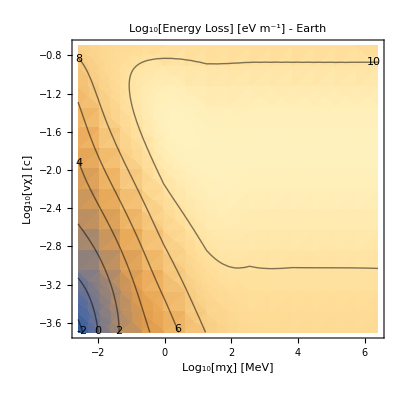

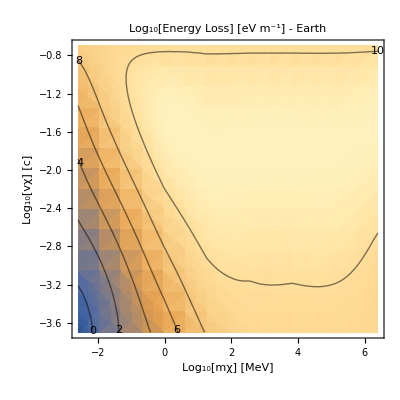

```mathematica
PlotEL[SiO2eELDict]
PlotEL[MgOeELDict]
```

#### EL functions

Organize into an EL function

Mantle

```mathematica
fTot0ELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(10^SiO2eELDict[["f"]][mχ,vχ]+10^SiNuc0ELDict[["f"]][mχ,vχ]+2 10^ONuc0ELDict[["f"]][mχ,vχ])+"MgOFrac"(10^MgOeELDict[["f"]] [mχ,vχ]+10^MgNuc0ELDict[["f"]][mχ,vχ]+ 10^ONuc0ELDict[["f"]][mχ,vχ])]/.EarthRepl
feELMantle[mχ_,vχ_]:= Log10["SiO2Frac"(("ρM")/("ρSiO2")/.MassDensities)(10^SiO2eELDict[["f"]][mχ,vχ])+"MgOFrac"(("ρM")/("ρMgO")/.MassDensities)(10^MgOeELDict[["f"]] [mχ,vχ])]/.EarthRepl (*ignores slight change in densities from surface to mantle in densities (we showed it's irrelevant for iron in the core, so it will be even less significant here)*)
```

Core

```mathematica
fTot0ELCore[mχ_,vχ_]:=Log10[10^FeeELDict[["f"]][mχ,vχ] + 10^FeNuc0ELDict[["f"]][mχ,vχ]]
feELCore[mχ_,vχ_]:=FeeELDict[["f"]][mχ,vχ]
```

```mathematica
FeeELDict[["f"]]
```

InterpolatingFunction[…]

```mathematica
FeNuc0ELDict[["f"]][-32.3,4.8]
FeNuc0ELDict[["f"]][-32.3,4.8]
```

-3.42349

```mathematica
10^-32("c")^2/("JpereV")/.SIConstRepl
10^-23("c")^2/("JpereV")/.SIConstRepl
```

5617.98

5.61798×10^12

### Test initialization functions

#### Propagating to the Earth

```mathematica
EK∞[mχ_,v∞_]:= 1/2 mχ (v∞)^2
```

```mathematica
E∞[mχ_,v∞_,r∞_,V_]:=EK∞[mχ,v∞]+V[r∞]
```

```mathematica
E∞[mχ,v∞,r∞,V[x,y,#]&]
```

EK∞[mχ,v∞]+V[x,y,r∞]

```mathematica
Vtest[r_]:=Gα/r
E∞[mχ,v∞,r∞,Vtest]
```

Gα/(r∞)+(mχ (v∞)^2)/2

```mathematica
vperp[v∞_,b∞_,r_]:=(b∞ v∞)/r
```

```mathematica
vr[mχ_,v∞_,b∞_,r∞_,V_,r_]:=√(2/mχ(E∞[mχ,v∞,r∞,V]-V[r])-vperp[v∞,b∞,r]^2)
```

```mathematica
vr[mχ,v∞,b∞,r∞,V,r]
```

√(-((b∞)^2 (v∞)^2)/r^2+(2 ((mχ (v∞)^2)/2-V[r]+V[r∞]))/mχ)

```mathematica
br[mχ_,v∞_,b∞_,r∞_,V_,r_]:=(b∞)/(√(1+(V[r∞]-V[r])/(EK∞[mχ,v∞])))
```

```mathematica
br[mχ,v∞,b∞,r∞,V,r]
```

(b∞)/(√(1+(2 (-V[r]+V[r∞]))/(mχ (v∞)^2)))

```mathematica
"G"/.SIConstRepl
```

6.67×10^-11

```mathematica
Vgrav[r_,mχ_] :=- (mχ("G"/.SIConstRepl)("ME"/.EarthRepl))/r
```

```mathematica
Vgrav[#,mχ]&
%[r]
```

Vgrav[#1,mχ]&

-(3.98199×10^14 mχ)/r

#### Example of Initial conditions

```mathematica
1/("rE"/.EarthRepl)br["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

0.499653

so barely changed, electrons are fast, but did decrease (which is the right direction)

```mathematica
vr["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,10^4 "rE"/.EarthRepl,Vgrav[#,"m"/.SIConstRepl]&,"rE"/.EarthRepl]
```

260048.

```mathematica
vperp["c"10^-3/.SIConstRepl,0.5 "rE"/.EarthRepl,"rE"/.EarthRepl]
```

150000.

#### Δr

```mathematica
Clear[Δrtest]
Δrtest[mχ_,vχ_,κ_,y_,consts_] :=(y 1/2 mχ vχ^2)/(κ^2 "JpereV"10^fELMantle[Log10[mχ], Log10[vχ]]) /.consts
```

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-9,10^-2,SIConstRepl]
%/("rE"/.EarthRepl)
```

1734.54

0.000272255

```mathematica
dE[rE_,bE_]:=2 √(rE^2-bE^2)
```

```mathematica
dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

1.10349×10^7

```mathematica
N[1/500]
```

0.002

```mathematica
Δrtest["m"/.SIConstRepl,"c"10^-3/.SIConstRepl,10^-10,10^-2,SIConstRepl]/dE["rE"/.EarthRepl,0.5"rE"/.EarthRepl]
```

0.0157187

So at 10^-10mixing at electron mass and halo speeds, with b∞ = 1/2 rE, we are in intermediate scattering regime

#### Δr generalised (e only)

```mathematica
dc[bE_] := 2 √(rcore^2-bE^2)
dE[bE_] := 2 √(REarth^2-bE^2)
dM[bE_]:= If[rcore^2>bE^2,dE[bE] - dc[bE],Re[dE[bE]]]
```

```mathematica
dM[0]+dc[0]
REarth 2
```

1.2742×10^7

1.2742×10^7

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
ΔrAveraged[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔEe[mχ,vχ,κ,bE,consts]
fΔrAveraged[mχ_,vχ_]:=Log10[ΔrAveraged[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

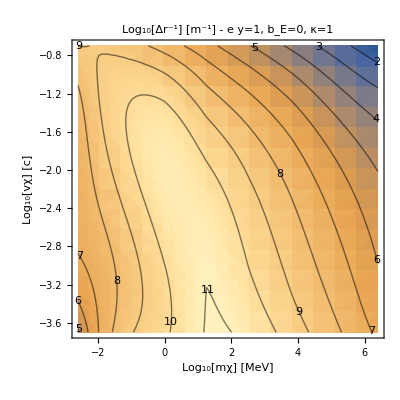

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveraged;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - e y=1, b_E=0, κ=1"]
]
```

#### Δr total

```mathematica
ΔETot0[mχ_,vχ_,κ_,bE_,consts_] :=(κ^2 "JpereV"(dM[bE] 10^fTot0ELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^fTot0ELCore[Log10[mχ], Log10[vχ]])) /.consts
(*EKbyΔEe[mχ_,vχ_,κ_,bE_,consts_] :=(  1/2 mχ vχ^2)/(κ^2 "JpereV"(dM[bE] 10^feELMantle[Log10[mχ], Log10[vχ]]+dc[bE] 10^feELCore[Log10[mχ], Log10[vχ]])) /.consts (* energy lost after travelling through the Earth over kinetic enrgy *)*)
EKbyΔETot0[mχ_,vχ_,κ_,bE_,consts_] := EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
ΔrAveragedTot0[mχ_,vχ_,κ_,y_,bE_,consts_]:= dE[bE] y EK[mχ,vχ]/ΔETot0[mχ,vχ,κ,bE,consts]
(*fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]*)
fΔrAveragedTot0[mχ_,vχ_]:=Log10[ΔrAveragedTot0[10^mχ,10^vχ,1,10^-2,0,SIConstRepl]^-1]
```

```mathematica
FeeELDict[["kinlist"]][["mχ"]]("c")^2/("JpereV")/.SIConstRepl
```

{2500.,48267.4,931898.,1.79921×10^7,3.47374×10^8,6.70674×10^9,1.29487×10^11,2.5×10^12}

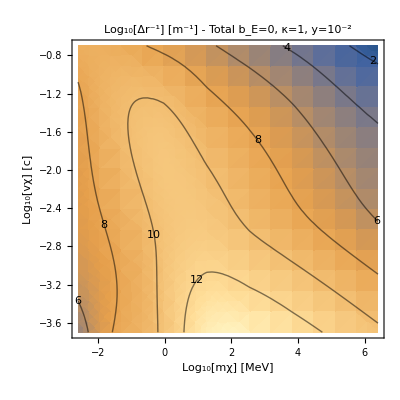

```mathematica
Block[{tempDict},
tempDict=FeeELDict;
tempDict[["f"]]=fΔrAveragedTot0;
PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]
]
```

4.81365+6.04929×10^-19 ⅈ

-3.69897

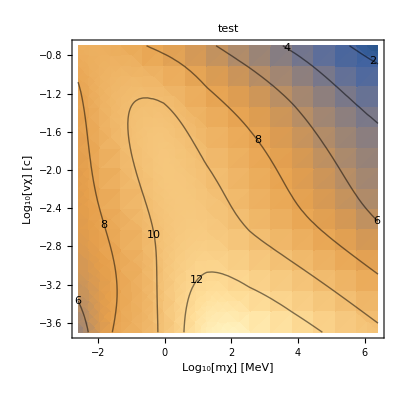

```mathematica
Block[{ELdict},
ELdict=FeeELDict;
ELdict[["f"]]=fΔrAveragedTot0;
(*PlotEL[tempDict,"",True,"Log_10[Δr^-1] [m^-1] - Total b_E=0, κ=1, y=10^-2"]*)
Print[ELdict[["f"]][Log[10,First[ELdict[["kinlist"]][["mχ"]]]],Log[10,First[ELdict[["kinlist"]][["vχ"]]]]]];
Print[N[Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]]];
Print[Show[{DensityPlot[Re[ELdict[["f"]][m+6 - Log10[("c"^2)/("JpereV")/.Constants`SIConstRepl],v +Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[mχ] [MeV]","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[vχ] [c]"},PlotLabel->"test"],
  ContourPlot[Re[ELdict[["f"]][m+6- Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],v+Log10["c"/.Constants`SIConstRepl]]],
  		{m,Log[10,First[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["mχ"]]]]-6 + Log10[("c")^2/("JpereV")/.Constants`SIConstRepl]},
  		{v,Log[10,First[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl],Log[10,Last[ELdict[["kinlist"]][["vχ"]]]]-Log10["c"/.Constants`SIConstRepl]},
  		ContourLabels->True,ContourShading->False]}]]
]
```

#### Explain boundary and peak (lowest kinetic energy above the fermi energy)

```mathematica
("EF")/("JpereV") /.FeeELDict[["fitparams"]]
("EF")/("JpereV") /.SiO2eELDict[["fitparams"]]
("EF")/("JpereV") /.MgOeELDict[["fitparams"]]
```

{8.0607,12.1265,20.9318,78.9,2030.5,42688.4}

{20.0443,58.1666}

{10.3207,18.4045,21.0279,50.3071}

```mathematica
((10^-2.5 "c")^2"m")/("JpereV") /.FeeELDict[["fitparams"]]
((10^-1.5 "c")^2 10^-2"m")/("JpereV") /.FeeELDict[["fitparams"]]
```

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

{5.11798,5.11798,5.11798,5.11798,5.11798,5.11798}

#### Interaction Length

```mathematica
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,
vχtemp,FeeELDict[["fitparams"]],βcore]& [1/2]];
(*NIntegrate[dσdEReNum[ω,mχtemp,vχtemp,FeTotalparams,βcore],{ω,0,ωmaxtemp}]*)
]
```

0.0262616

tesing cell input

```mathematica
σFe = 1.085089955014962*^13
```

1.08509×10^13

```mathematica
σtemp = 0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[dσdERe[# ωmaxtemp,mχtemp,vχtemp,FeTotalparams,βcore]& []];
(*σtemp = NIntegrate[dPdωeNum[ω,mχtemp,vχtemp,SiO2Totalparams],{ω,0,ωmaxtemp}]*)
]
```

0

```mathematica
lFe = κ^2("nI"/.SIcoreparams)σFe /.κ->10^-10(*approx, should really do density of each shell*)
```

1.52116×10^22

1.51848×10^15

0.

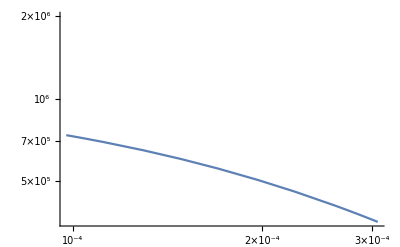

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
```

```mathematica
nIFromDensity[3580, "mN" /. SiNucCoeffs]
```

7.70224×10^28

```mathematica
1/(2 "ℏ")(2.5 10^7 ("JpereV")/("c")^2) (2.5 10^-5 "c")^2/.SIConstRepl
```

1.18632×10^13

```mathematica
SIcoreparams
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.1215×10^30,qF→3.2142×10^10,vF→3.72227×10^6,μ→6.31108×10^-18,ωp→5.97822×10^16,α→1/137,χ→0.432735,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→83.5454,nI→1.40188×10^29,Z→8,M→9.27329×10^-26,EF→6.31108×10^-18}

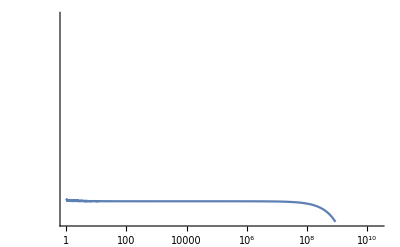

```mathematica
LogLogPlot[dPdωNuc0[ω,2.5 10^7 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-5 "c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,<|"nI"->("nI"/.SIcoreparams)|>],{ω,10^0,10^15},PlotRange->{0,2.5 10^8}]
```

```mathematica
σtemp=0;
Block[{mχtemp,vχtemp,ωmaxtemp},
mχtemp = 2 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;
ωmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ωmaxtemp];
Print[dPdωNuc0Num[1/10 ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]];
(*Print[LogLogPlot[dPdωNuc0Num[ω ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,10^-1},PlotRange->{0,2 10^6}]];*)
(*σtemp = NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>],{ω,0,ωmaxtemp}]*)
]
σtemp = 0;
Clear[SiNuc0σ]
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
```

1.51848×10^15

0.

2.90748×10^10

3.15401×10^16

```mathematica
((κ^2/.κ->10^-10)SiNuc0PTot)/((nIFromDensity[3580,"mN"/.SiNucCoeffs])("ℏ"/.SIConstRepl)(10^-3 "c"/.SIConstRepl))
```

0.000129382

9.5117×10^8

```mathematica
SiNuc0P[mχtemp_,vχtemp_]:=Module[{ωRmaxtemp,EKtemp,mNtemp},
(*{mχtemp,vχtemp,ωRmaxtemp,EKtemp,mNtemp},*)
(*mχtemp = 5 10^5 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 10^-3 "c"/.SIConstRepl;*)
EKtemp = 1/2 mχtemp vχtemp^2;
mNtemp = "mN"/.SiNucCoeffs;
ωRmaxtemp=EKtemp/("ℏ") (4 mNtemp mχtemp)/(mNtemp + mχtemp)^2/.SIConstRepl;
Print[ωRmaxtemp];
NIntegrate[dPdωNuc0Num[ω,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,mNtemp]|>],{ω,0,ωRmaxtemp}]
]
SiNuc0PTot=SiNuc0P[5 10^5 ("JpereV")/("c")^2/.SIConstRepl,10^-3 "c"/.SIConstRepl]
SiNuc0Pλ=(((κ^2/.κ->10^-10)SiNuc0PTot)/(10^-3 "c"/.SIConstRepl))^-1
```

2.90748×10^10

3.15401×10^16

9.5117×10^8

So from Nuclear Si at 0 temperature, the scattering length is large compared to the Earth

```mathematica
dPdωNuc0Num[# ωmaxtemp,mχtemp,vχtemp,SiNucCoeffs,SIConstRepl,<|"nI"->nIFromDensity[3580,"mN"/.SiNucCoeffs]|>]& [1/2]
```

```mathematica
SiNucCoeffs
```

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26|>

```mathematica
FrontEndTokenExecute@"Save"
```

### Unit testing for MC capture code

Psuedo code

We need to store the following to describe the state of the particle

globally we need 
(r,v_r,v_(⊥1),v_(⊥1)) with b the impact parameter and r the radial position in the earth

at each time step we need
l interaction length
i_int which process to interact with (electrical or nuclear)
velocity of target
	speed of target (sampled from distribution function)
	point on sphere - for velocity of target
E_R recoil energy 
	q momentum transfer
	scattering angle of DM particle
New velocity
	azimuthal angle 
	polar calculated from scattering angle

#### Update v

```mathematica
vr[r_,E_,V_,m_,vp_]:=√(Simplify[2/m E]-2/m V[r]-vp)
V[r_]:=-("α")/r
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

#### compute l - interaction length

#### σ

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
dσdERNuc0[]
```

```mathematica
?dσdERNuc0
```

## new

#### Load parameters

```mathematica
Clear[FeTotalparams,SiO2Totalparams,MgOTotalparams]
```

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

#### Load cross-sections

```mathematica
FeσDicteme=ReadIt[NotebookDirectory[]<>"../dsigmadER/FeσDictme"];
FeσDictNucme =ReadIt[NotebookDirectory[]<>"../dsigmadER/FeσDictNucme"];
SiO2σDicteme=ReadIt[NotebookDirectory[]<>"../dsigmadER/SiO2σDictme"];
SiσDictNucme =ReadIt[NotebookDirectory[]<>"../dsigmadER/SiσDictNucme"];
MgOσDicteme=ReadIt[NotebookDirectory[]<>"../dsigmadER/MgOσDictme"];
MgσDictNucme =ReadIt[NotebookDirectory[]<>"../dsigmadER/MgσDictNucme"];
OσDictNucme =ReadIt[NotebookDirectory[]<>"../dsigmadER/OσDictNucme"];
```

#### Load Interaction Length

```mathematica
Clear[FeλeDictSI,SiO2λeDictSI,MgOλeDictSI]
```

```mathematica
(*FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI"];*)
FeλeDictSI = ReadIt[NotebookDirectory[]<>"FeλeDictSI_total"];
SiO2λeDictSI = ReadIt[NotebookDirectory[]<>"SiO2λeDictSI_total"];
MgOλeDictSI = ReadIt[NotebookDirectory[]<>"MgOλeDictSI_total"];
```

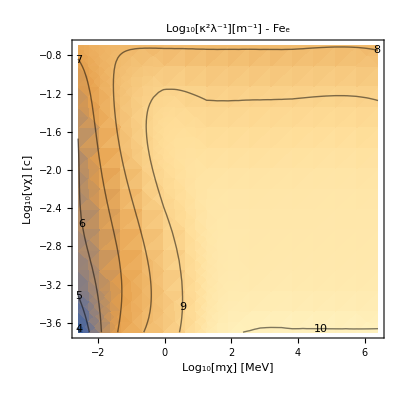

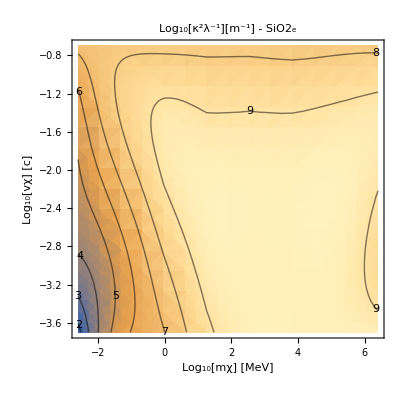

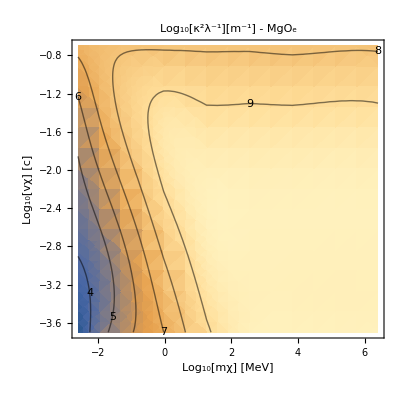

```mathematica
EnergyLoss`PlotEL[FeλeDictSI,"Fe_e",True,"Log_10[κ^2λ^-1][m^-1] - Fe_e"]
EnergyLoss`PlotEL[SiO2λeDictSI,"SiO2_e",True,"Log_10[κ^2λ^-1][m^-1] - SiO2_e"]
EnergyLoss`PlotEL[MgOλeDictSI,"MgO_e",True,"Log_10[κ^2λ^-1][m^-1] - MgO_e"]
```

```mathematica
FeλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["FeλeDictSIOscillator_``",i]]],{i,6}];
```

### Unit Test

#### Sampled Interaction length

```mathematica
FeλeDictSI[["f"]]
FeλeDictSI[["f"]][-25,6]
```

InterpolatingFunction[…]

9.69693

```mathematica
(*testl[mχ_,vχ_,κ_,f_,Natural_:False] := Module[{λ,mχnatconv,vχnatconv},
(*f is a log log function from kinematic variables to the inverse interaction length
κ is kinetic mixing
Natural == True is for natural units for kinematic variables ([eV] for mass and [c] for speed])*)
mχnatconv=("JpereV")/("c")^2/.Constants`SIConstRepl;
vχnatconv="c"/.Constants`SIConstRepl;
λ=If[Natural,10^(-f[Log10[mχ mχnatconv],Log10[vχ vχnatconv]]),10^(-f[Log10[mχ],Log10[vχ]])];
-λ/κ^2Log[1-Random[]]
]*)
Clear[testl]
```

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
```

3.10584×10^7

```mathematica
Capture`Getl[10^6,10^-2,10^-9,FeλeDictSI[["f"]],True]
```

9.15873×10^8

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

5.61798×10^12

```mathematica
("c")^2/("JpereV")10^-23/.SIConstRepl
```

5.61798×10^12

```mathematica
10^5/("c")/.SIConstRepl
```

1/3000

#### Update v

```mathematica
V[r_]:=-(("e")^2/("ϵ0"))/r-("G""ME")/r/.EarthRepl/.SIConstRepl
```

```mathematica
(*Clear[modv,Δt,vr]*)
Block[{m,r,v={vr,vp1,vp2},l,speed,Δt,Δr,L,vp,E},
speed = √(v.v);
Δt = l/speed;
Δr = Δt v[[1]];

E=m/2 speed^2;
vp = v.DiagonalMatrix[{0,1,1}].v;
(*L = m r vp;*)
v[[1]]=vr[r+Δr,E,V,m,vp];
v

]
```

{√(vr^2+(2 α)/(m (r+(l vr)/(√(vp1^2+vp2^2+vr^2))))),vp1,vp2}

```mathematica
√(-vp1^2-vp2^2+(2 (1/2 m (vp1^2+vp2^2+vr^2)-("α")/(r+(l vr)/(√(vp1^2+vp2^2+vr^2)))))/m)
```

```mathematica
(*vr[r_,E_,V_,m_,vp_]:=√(Simplify[(2/m)E]-(2/m)V[r]-vp^2)*)
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[r+Δr]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[r+Δr];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr[Abs[r+Δr],E,V,mχ,vp],vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)
Clear[Updatev,vr]
(*Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached},
speed = √(vχ.vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+V[r];
vp = √(vχ.DiagonalMatrix[{0,1,1}].vχ); (*(v_⊥)^2*)
vr=√(Simplify[(2/mχ)E]-(2/mχ)V[Abs[r+Δr]]-vp^2);(*updated radial velocity*)
(*L = m r vp;*)
(*Print[speed];
Print[Δt];
Print[Δr];
Print[vp];*)
(*vχ[[1]]=vr[Abs[r+Δr],E,V,mχ,vp];*)
(*Print[vr[r+Δr,E,V,mχ,vp]];*)
(*Print[(mχ/2)speed^2+V[r] >V[r+Δr]+(mχ/2)vp^2];*)
reached=(mχ/2)speed^2-(mχ/2)vp^2+V[r] >V[Abs[r+Δr]];(*check that Energy is high enough to reach r+Δr*)
<|"vχ"->If[reached,{vr,vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"reached?"->reached,"E"->E,"vp"->vp,"Δr"->Δr,"V[r]"->V[r],"V[|r+Δr|]"->V[Abs[r+Δr]],"l"->l,"vχ"->vχ,"mχ"->N[mχ]|>
(*{vr[r+Δr,E,V,mχ,vp],vχ[[2]],vχ[[3]]}*)

]*)(*******USE THIS VERSION IF THE PACKAGE VERSION STOPS WORKING*)
```

```mathematica
(10^-25 Vgrav[#])&
%[1]
```

Vgrav[#1]/10^25&

-9.37527×10^-18

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

3.54856×10^8

<|vχ→{1000,0,0},r→4.54856×10^8,reached?→False,E→-3.48199×10^-19,vp→0,Δr→3.54856×10^8,V[r]→-3.98199×10^-19,V[|r+Δr|]→-8.75439×10^-20,l→3.54856×10^8,mχ→1.×10^-25|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.3445×10^7

<|vχ→{2667.93,0,0},r→5.6555×10^7,reached?→True,E→-3.48199×10^-19,vp→0,Δr→-4.3445×10^7|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

4.23098×10^8

<|vχ→{1000,0,0},r→3.23098×10^8,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
Updatev[{-10^3,0,0},10^-25,10^8,%,(10^-25 Vgrav[#])&]
```

1.40354×10^8

<|vχ→{1000,0,0},r→4.03544×10^7,reached?→False|>

```mathematica
Capture`Getl[10^-25,10^5,10^-9,FeλeDictSI[["f"]]]
N[Updatev[{- 10^6,0,0},10^-25,10^6,1,V]]
```

5.19371×10^7

1000000

1/1000000

-1

0

(1000000 √(156999863/15222207))/3

```mathematica
{1.070507144976343*^6×100.,0.}
```

**** can’t use alpha, I need SI units.
✓ **** also don’t think this is correct, need the difference between current and next potential
**** also need to sort out sign for velocity

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
LogLogPlot[Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r],{r,0,10^7}]
```

Piecewise::pairs: The first argument {0.000102386 G ME,False} of Piecewise is not a list of pairs.

-Graphics-

```mathematica
Piecewise[{("G""ME")/r,r>"rE"/.EarthRepl},{("ME")/("rE")^3"G" r,r>"rE"/.EarthRepl}][r]
```

Piecewise::pairs: The first argument {(G ME)/r,r>6.371×10^6} of Piecewise is not a list of pairs.

```mathematica
Clear[Vgrav]
Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( 3("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl
(*Vgrav[r_]:=Piecewise[{{-("G" "ME")/r,r>"rE"/.EarthRepl},{-("ME" "G")/(2("rE")^3)( ("rE")^2-r^2),r<"rE"/.EarthRepl}}]/.SIConstRepl/.EarthRepl*)
```

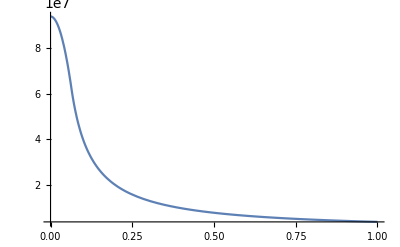

```mathematica
Plot[-Vgrav[r],{r,0,10^8},PlotRange->All]
```

```mathematica
-Vgrav[10^8]
```

3.98199×10^6

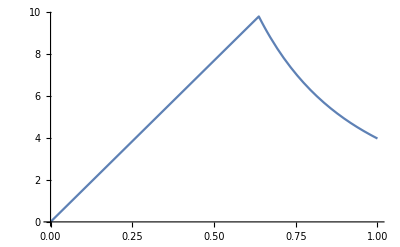

```mathematica
Plot[D[Vgrav[r],r]/.r->rt/.SIConstRepl/.EarthRepl,{rt,0,10^7}]
```

```mathematica
-D[Vgrav[r],r]
```

-(Piecewise[{{1.53985×10^-6 r, r<6371000}, {(3.98199×10^14)/r^2, r>6371000}, {Indeterminate, True}}])

#### Rejection Method

```mathematica
dσdERdΩe[ω_,cosθ_,mχ_,vχ_,κ_]:=1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")1/(1-E^(-"β" "ℏ" ω))Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))
```

```mathematica
Clear[GetElectroniccosθandωbyRejection]
GetElectroniccosθandωbyRejection[mχ_,vχ_,κ_,params_]:=Module[{ERmax,ERmin,ξ,cosθ,ω},

ξ=Table[Random[],{i,3}];

cosθ = 1 - 2 ξ[[1]];

ERmax = mχ/2 vχ^2 cosθ^2;
ERmin= "ℏ""ωedgei"/.params;
ω = 1/("ℏ")(ERmin + ξ[[2]] (ERmax - ERmin))/.params;

(*P=(2 π)/σ dσdERdΩe[ω,cosθ,mχ,vχ,κ];(*2 π from integral over ϕ*)*)
(*M=1;*)
Do[dσdERdΩe[1/("ℏ")(ERmin + ξ[[2]] (ERmax - ERmin))/.params,cosθ,mχ,vχ,κ],{i,100}]
(*{ξ,cosθ,ω,dσdERdΩe[ω,cosθ,mχ,vχ,κ]/.params}*)
]
```

```mathematica
GetElectroniccosθandωbyRejection["m"/.FeTotalparams[[2]],"c"10^-3/.FeTotalparams[[2]],1,FeTotalparams[[2]]]
```

{{0.138553,0.761561,0.129917},0.722893,1.56214×10^14,0.0000347588}

```mathematica
10^FeσDicteme[[2]]["σf"][Log10["c"10^-3/.FeTotalparams[[2]]]]
```

4.76188×10^-23

```mathematica
GetElectroniccosθandωbyRejection["m"/.FeTotalparams[[2]],"c"10^-3/.FeTotalparams[[2]],1,FeTotalparams[[2]]]
```

## dσ/(dE_R dΩ)

#### Kinematics - Sanity checks on them - Electronic

```mathematica
Print["Double check that we have evaluated the q δ function correctly"]
Integrate[f[q]DiracDelta[ω-q v cosθ +(ℏ q^2)/(2 mχ)],{q,0,∞}]
Print["We find that in our expression in the notes we need to take ωqp to:"]
√Abs[mχ/(cosθ^2 mχ v^2-2 ω ℏ)]
```

Double check that we have evaluated the q δ function correctly

ConditionalExpression[√Abs[mχ/(cosθ^2 mχ v^2-2 ω ℏ)] Boole[ℏ (cosθ mχ v+ℏ √((mχ (cosθ^2 mχ v^2-2 ω ℏ))/ℏ^2))>0] f[(cosθ mχ v)/ℏ+√((mχ (cosθ^2 mχ v^2-2 ω ℏ))/ℏ^2)], ]

We find that in our expression in the notes we need to take ωqp to:

√Abs[mχ/(cosθ^2 mχ v^2-2 ω ℏ)]

```mathematica
δqsolns =Solve[ω-q v cosθ +(ℏ q^2)/(2 mχ)==0,q]
Solve[(q/.%[[1]])==0,ω]
Print["So mathematica has missed on of the solutions.  Notice also that both solutions are non-zero and real for ω > cos^2θ ((E^χ)_i)/ℏ and cosθ>0. Notice this excludes back scattering (cosθ<0) which is a result of us imposing ω>0: ω= qvcosθ-(ℏ SuperscriptBox[q, 2])/(2 mχ) means cosθ<0 => ω<0"]
```

{{q→(mχ (cosθ v-(√(cosθ^2 mχ v^2-2 ω ℏ))/(√mχ)))/ℏ},{q→(mχ (cosθ v+(√(cosθ^2 mχ v^2-2 ω ℏ))/(√mχ)))/ℏ}}

{{ω→0}}

So mathematica has missed on of the solutions.  Notice also that both solutions are non-zero and real for ω > cos^2θ ((E^χ)_i)/ℏ and cosθ>0. Notice this excludes back scattering (cosθ<0) which is a result of us imposing ω>0: ω= qvcosθ-(ℏ SuperscriptBox[q, 2])/(2 mχ) means cosθ<0 => ω<0

```mathematica
Print["Let's integrate by hand since mathematica refuses to give us both solutions."]
D[ω-q v cosθ +(ℏ q^2)/(2 mχ),q]
%/.Table[δqsolns[[i]],{i,2}]
Print["So the integral above over the arbitrary function f and the delta function is"]
Sum[f[q]/(%%[[i]])/.δqsolns[[i]],{i,2}]//Simplify
```

Let's integrate by hand since mathematica refuses to give us both solutions.

-cosθ v+(q ℏ)/mχ

{-(√(cosθ^2 mχ v^2-2 ω ℏ))/(√mχ),(√(cosθ^2 mχ v^2-2 ω ℏ))/(√mχ)}

So the integral above over the arbitrary function f and the delta function is

(√mχ (-f[(cosθ mχ v-√mχ √(cosθ^2 mχ v^2-2 ω ℏ))/ℏ]+f[(cosθ mχ v+√mχ √(cosθ^2 mχ v^2-2 ω ℏ))/ℏ]))/(√(cosθ^2 mχ v^2-2 ω ℏ))

```mathematica
Print["q_0 is given by:"]
(mχ v)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))
Print["The radical argument of q_0 is given by:"]
cosθ^2-(2ω "ℏ")/(mχ v^2)
Print["Substituting ω->ω_q we have"]
cosθ^2-(2ω "ℏ")/(mχ v^2)/.ω-> (q v cosθ - ("ℏ" q^2)/(2 mχ))//Simplify
Print["This is strictly positive, and since the radical is strictly decreasing in ω, this means q_0 is always real for ω∈(0,ω_q). We can also put q_0 on ω_q and we find"]
(mχ v)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))/.ω-> (q v cosθ - ("ℏ" q^2)/(2 mχ))//Simplify//PowerExpand//Simplify
Print["So, duh, on shell these are all degenerate. Similarily, putting ω_q on q_0 we have"]
 (q v cosθ - ("ℏ" q^2)/(2 mχ))/.q->(mχ v)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))//Simplify
Print["so ω_q evaluated on q_0 gives ω. This means we are only limited by ℏω-E_(χ, i)<0"]
```

q_0 is given by:

(mχ v (cosθ+√(cosθ^2-(2 ℏ ω)/(mχ v^2))))/ℏ

The radical argument of q_0 is given by:

cosθ^2-(2 ℏ ω)/(mχ v^2)

Substituting ω->ω_q we have

(ℏ q-cosθ mχ v)^2/(mχ^2 v^2)

This is strictly positive, and since the radical is strictly decreasing in ω, this means q_0 is always real for ω∈(0,ω_q). We can also put q_0 on ω_q and we find

q

So, duh, on shell these are all degenerate. Similarily, putting ω_q on q_0 we have

ω

so ω_q evaluated on q_0 gives ω. This means we are only limited by ℏω-E_(χ, i)<0

```mathematica
Print["Now check units. "]
q^2/(ℏ v)V/.q->1/L/.V->J L^3/.ℏ -> J s/.v->L/s
```

Now check units.

1

```mathematica
(mχ v)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))/.ω-> (q v cosθ - ("ℏ" q^2)/(2 mχ))ξ//Simplify//PowerExpand//Simplify
Solve[0==%,cosθ]
```

(mχ v (cosθ+√(cosθ^2+(ℏ q (ℏ q-2 cosθ mχ v) ξ)/(mχ^2 v^2))))/ℏ

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{cosθ→(ℏ q)/(2 mχ v)}}

```mathematica
Solve[(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))==0,cosθ]
Solve[(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ v^2)))==0,ω]
Print["From this we see that q->0 iff ω->0 as expected"]
```

{}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→0}}

From this we see that q->0 iff ω->0 as expected

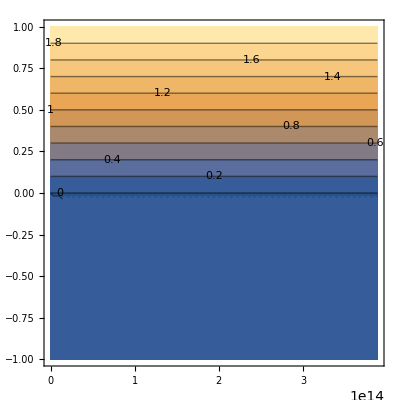

```mathematica
ContourPlot[(cosθ+√(cosθ^2-(ω "ℏ")/Eχ))/.Eχ->("m" ("c"10^-3 )^2)/(2 "ℏ")/.SIConstRepl,{ω,0,("m" ("c"10^-3 )^2)/(2 "ℏ")/.SIConstRepl},{cosθ,-1,1},ContourLabels->True]
```

#### Nuclear - Finite Temp Sanity Checks

```mathematica
n(√(mχ β))/(q ℏ)/.mχ->(s^2 J)/L^2/.β->1/J/.q->1/L/.ℏ->s J/.n->1/L^3//PowerExpand
```

1/(J L^3)

```mathematica
n δ /. n->1/L^3/.δ->1/J
```

1/(J L^3)

#### Pipeline for double function interpolation, integration, and maximum finding - For

```mathematica
Clear[gtest,gtest2]
interptest2D=FunctionInterpolation[x^2+y^2,{x,0,1},{y,0,1},InterpolationOrder->4]
(*gtest[xp_,yp_]:=(Integrate[(FunctionInterpolation[x^2+y^2,{x,0,1},{y,0,1}]),{x,0,#1},{y,0,#2}])&[xp,yp]*)
(*gtest[xp_Real,yp_Real]:=NIntegrate[interptest2D[x,y],{x,0,xp},{y,0,yp}]*)
gtest=Integrate[interptest2D[x,y],{x,0,#1},{y,0,#2}]&
gtest2=Interpolation[Flatten[Table[{{ToExpression@i,ToExpression@j},ToExpression@Integrate[interptest2D[x,y],{x,0.0,i},{y,0,j}]},{i,0,1,0.05},{j,0,1,0.05}],1]]
NMaximize[gtest2[x,y],{x,y}∈Rectangle[{0,0},{1,1}]]
(*InverseFunction[gtest][1,0.5]*)
```

InterpolatingFunction[…]

∫_0^#1 ∫_0^#2 interptest2D[x,y]ⅆyⅆx&

InterpolatingFunction[…]

{0.666667,{x→1.,y→1.}}

#### Setup dσdERdΩ - plots and sanity checks

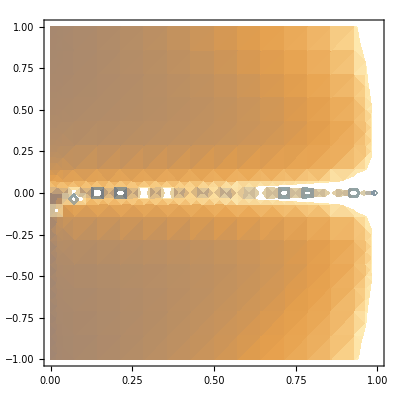

```mathematica
DensityPlot[dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]],{ξω,0,1},{cosθ,-1,1}]
```

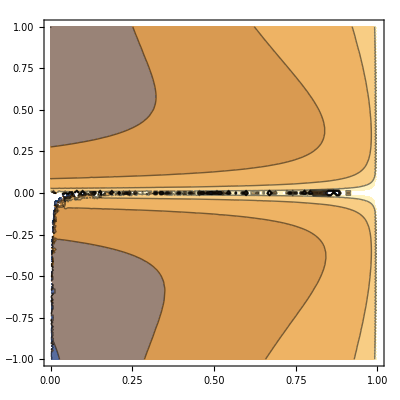

```mathematica
ContourPlot[Log10[dσdERdΩe[ω,cosθ,mχ,vχ,1]]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]],{ξω,0,1},{cosθ,-1,1}]
```

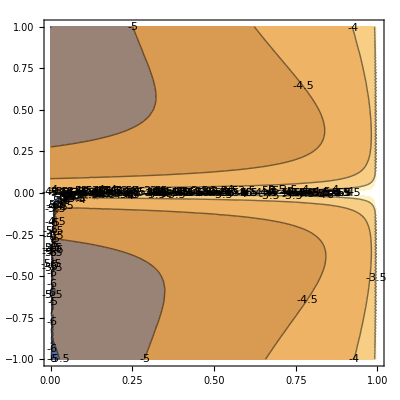

```mathematica
ContourPlot[Log10[dσdERdΩe[ω,cosθ,mχ,vχ,1]]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]],{ξω,0,1},{cosθ,-1,1},ContourLabels->True]
```

```mathematica
dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]]/.{ξω->0.5,cosθ->0.001}
dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]]/.{ξω->0.000000000001,cosθ->0.99}
dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]]/.{ξω->0.00000000000,cosθ->0.99}
Print["So we have a removable singularity at ω=0, this is probably from the thermal factor which evaluates to 1/0 there."]
```

0.0034565

3.16788×10^-6

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

So we have a removable singularity at ω=0, this is probably from the thermal factor which evaluates to 1/0 there.

```mathematica
dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]]/.{ξω->0.5,cosθ->0.00001}
dσdERdΩe[ω,cosθ,mχ,vχ,1]/.ω->cosθ^2 (mχ vχ^2)/(2 "ℏ")ξω/.{mχ->"m",vχ->"c"10^-3}/.FeTotalparams[[2]]/.{ξω->0.5,cosθ->0.0000001}
Print["We also seem to have a numerical instability at cosθ=0. This corresponds to the q->0 limit. Recalling our previous look at ϵM this is not suprising. From the below plot, it looks like the same numerical instability arises as q->0 there."]
```

7.35241×10^-11

-3.95703×10^-13

We also seem to have a numerical instability at cosθ=0. This corresponds to the q->0 limit. Recalling our previous look at ϵM this is not suprising. From the below plot, it looks like the same numerical instability arises as q->0 there.

#### Test the 2D interpolation of ϵ(q,ω)

```mathematica
Clear[Seofωandq]
(*Seofωandq[q_,ω_,params_]:=(("e")^2/(4 π "ϵ0" q^2))^-1 2/(1-E^(-"β" "ℏ" ω))Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.params*)
Seofωandq[q_,ω_,params_]:=Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.params
dσdERdΩe[ω_,cosθ_,mχ_,vχ_,κ_]:=1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))Im[-1/(Dielectrics`ϵMωq[ω,q,"νi","qF","vF"])]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))
```

```mathematica
NMaximize[dσdERdΩe[ξω cosθ^2,cosθ,mχ,vχ,κ],{ξω,}∈Rectangle[{0,0},{1,1}]]
```

```mathematica
Clear[InterpolateSetest]
InterpolateSetest[mχ_,params_,m_:20,n_:20,ϵ_:10^-2,uselog_:False]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,InterPω,InterPq,InterSTable,InterSf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

vχmax=2 10^-2"c"/.params;
ωmin= "ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=ϵ qmax;
     InterPω= 10^Subdivide[Log10[ωmin],Log10[ωmax],m];
InterPq = 10^Subdivide[Log10[qmin],Log10[qmax],n];

InterSTable=Table[{{InterPω[[i]],InterPq[[j]]},Seofωandq[InterPω[[i]],InterPq[[j]],params]},{i,m+1},{j,n+1}];
InterSf=Interpolation[Flatten[Log10[InterSTable],1],InterpolationOrder->4];

<|"Sf"->InterSf,"STable"->InterSTable,"ωs"->InterPω,"qs"->InterPq,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax}|>
]
```

```mathematica
Setest=InterpolateSetest["m"/.SIConstRepl,FeTotalparams[[2]]]
```

<|Sf→InterpolatingFunction[…],STable→{{{{6.5887×10^12,5.18104×10^8},-2.56915×10^-27},{{6.5887×10^12,6.52255×10^8},-2.84839×10^-27},{{6.5887×10^12,8.2114×10^8},-2.96117×10^-27},{{6.5887×10^12,1.03375×10^9},-4.16484×10^-27},{{6.5887×10^12,1.30142×10^9},-1.50264×10^-27},{{6.5887×10^12,1.63839×10^9},-8.95539×10^-27},{{6.5887×10^12,2.06261×10^9},-3.77646×10^-27},{{6.5887×10^12,2.59667×10^9},-5.63233×10^-27},{{6.5887×10^12,3.26902×10^9},-1.04069×10^-26},{{6.5887×10^12,4.11545×10^9},-2.56261×10^-26},{{6.5887×10^12,5.18104×10^9},-2.08737×10^-26},{{6.5887×10^12,6.52255×10^9},-3.06895×10^-26},{{6.5887×10^12,8.2114×10^9},-3.1×10^-26},{{6.5887×10^12,1.03375×10^10},-3.7279×10^-26},{{6.5887×10^12,1.30142×10^10},-8.32371×10^-26},{{6.5887×10^12,1.63839×10^10},-1.20025×10^-25},{{6.5887×10^12,2.06261×10^10},-1.16229×10^-25},{{6.5887×10^12,2.59667×10^10},-1.83641×10^-25},{{6.5887×10^12,3.26902×10^10},-1.12359×10^-25},{{6.5887×10^12,4.11545×10^10},-2.84092×10^-25},{{6.5887×10^12,5.18104×10^10},-2.35014×10^-25}},{{{1.09003×10^13,5.18104×10^8},9.96082×10^-28},{{1.09003×10^13,6.52255×10^8},1.27835×10^-27},{{1.09003×10^13,8.2114×10^8},9.65472×10^-28},{{1.09003×10^13,1.03375×10^9},1.29266×10^-27},{{1.09003×10^13,1.30142×10^9},2.89079×10^-27},{{1.09003×10^13,1.63839×10^9},3.76165×10^-27},{{1.09003×10^13,2.06261×10^9},3.34935×10^-27},{{1.09003×10^13,2.59667×10^9},2.66526×10^-27},{{1.09003×10^13,3.26902×10^9},-4.21246×10^-27},{{1.09003×10^13,4.11545×10^9},1.00635×10^-26},{{1.09003×10^13,5.18104×10^9},1.03477×10^-26},{{1.09003×10^13,6.52255×10^9},5.23357×10^-27},{{1.09003×10^13,8.2114×10^9},1.21076×10^-26},{{1.09003×10^13,1.03375×10^10},2.37344×10^-26},{{1.09003×10^13,1.30142×10^10},9.47046×10^-27},{{1.09003×10^13,1.63839×10^10},4.67928×10^-26},{{1.09003×10^13,2.06261×10^10},3.96547×10^-26},{{1.09003×10^13,2.59667×10^10},3.73179×10^-26},{{1.09003×10^13,3.26902×10^10},7.26135×10^-26},{{1.09003×10^13,4.11545×10^10},8.52682×10^-26},{{1.09003×10^13,5.18104×10^10},5.70481×10^-26}},{{{1.80332×10^13,5.18104×10^8},-9.01031×10^-28},{{1.80332×10^13,6.52255×10^8},-1.47856×10^-27},{{1.80332×10^13,8.2114×10^8},-1.84786×10^-27},{{1.80332×10^13,1.03375×10^9},-1.78074×10^-27},{{1.80332×10^13,1.30142×10^9},-4.25939×10^-27},{{1.80332×10^13,1.63839×10^9},-2.79527×10^-27},{{1.80332×10^13,2.06261×10^9},-4.57357×10^-27},{{1.80332×10^13,2.59667×10^9},-5.71496×10^-27},{{1.80332×10^13,3.26902×10^9},-5.44251×10^-27},{{1.80332×10^13,4.11545×10^9},-8.85398×10^-27},{{1.80332×10^13,5.18104×10^9},-1.09756×10^-26},{{1.80332×10^13,6.52255×10^9},-1.36023×10^-26},{{1.80332×10^13,8.2114×10^9},-1.6718×10^-26},{{1.80332×10^13,1.03375×10^10},-2.55647×10^-26},{{1.80332×10^13,1.30142×10^10},-2.44573×10^-26},{{1.80332×10^13,1.63839×10^10},-2.90335×10^-26},{{1.80332×10^13,2.06261×10^10},-4.45451×10^-26},{{1.80332×10^13,2.59667×10^10},-5.17964×10^-26},{{1.80332×10^13,3.26902×10^10},-7.51819×10^-26},{{1.80332×10^13,4.11545×10^10},-8.44674×10^-26},{{1.80332×10^13,5.18104×10^10},-1.41799×10^-25}},{{{2.98339×10^13,5.18104×10^8},1.1491×10^-28},{{2.98339×10^13,6.52255×10^8},1.44663×10^-28},{{2.98339×10^13,8.2114×10^8},1.8212×10^-28},{{2.98339×10^13,1.03375×10^9},2.29275×10^-28},{{2.98339×10^13,1.30142×10^9},-1.33248×10^-27},{{2.98339×10^13,1.63839×10^9},-6.51088×10^-28},{{2.98339×10^13,2.06261×10^9},1.74963×10^-27},{{2.98339×10^13,2.59667×10^9},1.37982×10^-27},{{2.98339×10^13,3.26902×10^9},1.73709×10^-27},{{2.98339×10^13,4.11545×10^9},-1.60548×10^-27},{{2.98339×10^13,5.18104×10^9},-5.26694×10^-27},{{2.98339×10^13,6.52255×10^9},1.49414×10^-27},{{2.98339×10^13,8.2114×10^9},1.97074×10^-27},{{2.98339×10^13,1.03375×10^10},-7.12025×10^-27},{{2.98339×10^13,1.30142×10^10},3.26562×10^-27},{{2.98339×10^13,1.63839×10^10},1.44348×10^-26},{{2.98339×10^13,2.06261×10^10},5.62641×10^-27},{{2.98339×10^13,2.59667×10^10},1.54061×10^-26},{{2.98339×10^13,3.26902×10^10},1.99904×10^-26},{{2.98339×10^13,4.11545×10^10},3.88069×10^-26},{{2.98339×10^13,5.18104×10^10},-3.0402×10^-26}},{{{4.93569×10^13,5.18104×10^8},3.98237×10^-28},{{4.93569×10^13,6.52255×10^8},1.34089×10^-28},{{4.93569×10^13,8.2114×10^8},6.31163×10^-28},{{4.93569×10^13,1.03375×10^9},4.08757×10^-28},{{4.93569×10^13,1.30142×10^9},5.14595×10^-28},{{4.93569×10^13,1.63839×10^9},6.47837×10^-28},{{4.93569×10^13,2.06261×10^9},4.24026×10^-28},{{4.93569×10^13,2.59667×10^9},1.50715×10^-27},{{4.93569×10^13,3.26902×10^9},6.19865×10^-29},{{4.93569×10^13,4.11545×10^9},1.62729×10^-27},{{4.93569×10^13,5.18104×10^9},-8.85292×10^-28},{{4.93569×10^13,6.52255×10^9},2.57908×10^-27},{{4.93569×10^13,8.2114×10^9},1.55703×10^-28},{{4.93569×10^13,1.03375×10^10},4.08757×10^-27},{{4.93569×10^13,1.30142×10^10},2.88646×10^-28},{{4.93569×10^13,1.63839×10^10},3.63384×10^-28},{{4.93569×10^13,2.06261×10^10},8.22215×10^-27},{{4.93569×10^13,2.59667×10^10},5.50527×10^-27},{{4.93569×10^13,3.26902×10^10},1.92369×10^-26},{{4.93569×10^13,4.11545×10^10},2.42178×10^-26},{{4.93569×10^13,5.18104×10^10},4.04905×10^-26}},{{{8.16553×10^13,5.18104×10^8},-2.71664×10^-28},{{8.16553×10^13,6.52255×10^8},-1.93693×10^-28},{{8.16553×10^13,8.2114×10^8},-3.37201×10^-28},{{8.16553×10^13,1.03375×10^9},-5.42041×10^-28},{{8.16553×10^13,1.30142×10^9},-6.82389×10^-28},{{8.16553×10^13,1.63839×10^9},-8.59077×10^-28},{{8.16553×10^13,2.06261×10^9},-8.47012×10^-28},{{8.16553×10^13,2.59667×10^9},-1.95198×10^-27},{{8.16553×10^13,3.26902×10^9},-1.34242×10^-27},{{8.16553×10^13,4.11545×10^9},-1.69001×10^-27},{{8.16553×10^13,5.18104×10^9},-2.71664×10^-27},{{8.16553×10^13,6.52255×10^9},-4.15697×10^-27},{{8.16553×10^13,8.2114×10^9},-5.23331×10^-27},{{8.16553×10^13,1.03375×10^10},-5.42041×10^-27},{{8.16553×10^13,1.30142×10^10},-1.12627×10^-26},{{8.16553×10^13,1.63839×10^10},-1.04418×10^-26},{{8.16553×10^13,2.06261×10^10},-1.08005×10^-26},{{8.16553×10^13,2.59667×10^10},-1.36154×10^-26},{{8.16553×10^13,3.26902×10^10},-2.08342×10^-26},{{8.16553×10^13,4.11545×10^10},-2.15498×10^-26},{{8.16553×10^13,5.18104×10^10},-2.12392×10^-26}},{{{1.35089×10^14,5.18104×10^8},-1.15789×10^-28},{{1.35089×10^14,6.52255×10^8},-1.12741×10^-29},{{1.35089×10^14,8.2114×10^8},-7.06335×10^-29},{{1.35089×10^14,1.03375×10^9},-1.78682×10^-29},{{1.35089×10^14,1.30142×10^9},-2.24947×10^-29},{{1.35089×10^14,1.63839×10^9},-3.65901×10^-28},{{1.35089×10^14,2.06261×10^9},-1.77747×10^-28},{{1.35089×10^14,2.59667×10^9},-4.01027×10^-28},{{1.35089×10^14,3.26902×10^9},-2.81197×10^-28},{{1.35089×10^14,4.11545×10^9},-9.19747×10^-28},{{1.35089×10^14,5.18104×10^9},-8.95531×10^-29},{{1.35089×10^14,6.52255×10^9},-1.00938×10^-27},{{1.35089×10^14,8.2114×10^9},-1.41932×10^-28},{{1.35089×10^14,1.03375×10^10},-8.92467×10^-28},{{1.35089×10^14,1.30142×10^10},-2.24947×10^-28},{{1.35089×10^14,1.63839×10^10},-3.66158×10^-27},{{1.35089×10^14,2.06261×10^10},-4.60965×10^-27},{{1.35089×10^14,2.59667×10^10},-4.01027×10^-27},{{1.35089×10^14,3.26902×10^10},-5.05376×10^-27},{{1.35089×10^14,4.11545×10^10},2.11738×10^-27},{{1.35089×10^14,5.18104×10^10},-1.15789×10^-26}},{{{2.2349×10^14,5.18104×10^8},6.13447×10^-29},{{2.2349×10^14,6.52255×10^8},-3.10957×10^-29},{{2.2349×10^14,8.2114×10^8},-3.91472×10^-29},{{2.2349×10^14,1.03375×10^9},-4.92834×10^-29},{{2.2349×10^14,1.30142×10^9},1.00147×10^-28},{{2.2349×10^14,1.63839×10^9},-9.97195×10^-30},{{2.2349×10^14,2.06261×10^9},2.44218×10^-28},{{2.2349×10^14,2.59667×10^9},9.20066×10^-29},{{2.2349×10^14,3.26902×10^9},-1.98966×10^-29},{{2.2349×10^14,4.11545×10^9},4.87279×10^-28},{{2.2349×10^14,5.18104×10^9},6.13447×10^-28},{{2.2349×10^14,6.52255×10^9},7.72285×10^-28},{{2.2349×10^14,8.2114×10^9},6.31882×10^-28},{{2.2349×10^14,1.03375×10^10},3.66285×10^-28},{{2.2349×10^14,1.30142×10^10},1.00056×10^-27},{{2.2349×10^14,1.63839×10^10},1.93989×10^-27},{{2.2349×10^14,2.06261×10^10},-1.25539×10^-28},{{2.2349×10^14,2.59667×10^10},9.18266×10^-28},{{2.2349×10^14,3.26902×10^10},2.51557×10^-27},{{2.2349×10^14,4.11545×10^10},-1.96201×10^-27},{{2.2349×10^14,5.18104×10^10},1.83577×10^-27}},{{{3.69739×10^14,5.18104×10^8},-4.29205×10^-29},{{3.69739×10^14,6.52255×10^8},-5.40338×10^-29},{{3.69739×10^14,8.2114×10^8},1.44276×10^-29},{{3.69739×10^14,1.03375×10^9},1.81633×10^-29},{{3.69739×10^14,1.30142×10^9},2.28662×10^-29},{{3.69739×10^14,1.63839×10^9},2.87869×10^-29},{{3.69739×10^14,2.06261×10^9},3.62406×10^-29},{{3.69739×10^14,2.59667×10^9},-2.80289×10^-28},{{3.69739×10^14,3.26902×10^9},-3.52863×10^-28},{{3.69739×10^14,4.11545×10^9},-1.3432×10^-28},{{3.69739×10^14,5.18104×10^9},-5.5925×10^-28},{{3.69739×10^14,6.52255×10^9},-2.12883×10^-28},{{3.69739×10^14,8.2114×10^9},-8.86351×10^-28},{{3.69739×10^14,1.03375×10^10},-3.37396×10^-28},{{3.69739×10^14,1.30142×10^10},-7.51444×10^-28},{{3.69739×10^14,1.63839×10^10},-5.34737×10^-28},{{3.69739×10^14,2.06261×10^10},-2.22641×10^-27},{{3.69739×10^14,2.59667×10^10},-1.49933×10^-27},{{3.69739×10^14,3.26902×10^10},-1.06694×10^-27},{{3.69739×10^14,4.11545×10^10},-3.4093×10^-27},{{3.69739×10^14,5.18104×10^10},-1.69099×10^-27}},{{{6.11691×10^14,5.18104×10^8},-2.12135×10^-29},{{6.11691×10^14,6.52255×10^8},-2.67062×10^-29},{{6.11691×10^14,8.2114×10^8},-3.36211×10^-29},{{6.11691×10^14,1.03375×10^9},-4.23265×10^-29},{{6.11691×10^14,1.30142×10^9},-5.32859×10^-29},{{6.11691×10^14,1.63839×10^9},-6.7083×10^-29},{{6.11691×10^14,2.06261×10^9},-8.44525×10^-29},{{6.11691×10^14,2.59667×10^9},-1.85053×10^-28},{{6.11691×10^14,3.26902×10^9},-2.32968×10^-28},{{6.11691×10^14,4.11545×10^9},-2.93289×10^-28},{{6.11691×10^14,5.18104×10^9},-3.69229×10^-28},{{6.11691×10^14,6.52255×10^9},-4.64831×10^-28},{{6.11691×10^14,8.2114×10^9},-4.60713×10^-28},{{6.11691×10^14,1.03375×10^10},-5.80003×10^-28},{{6.11691×10^14,1.30142×10^10},-5.32859×10^-28},{{6.11691×10^14,1.63839×10^10},-1.1676×10^-27},{{6.11691×10^14,2.06261×10^10},-1.46993×10^-27},{{6.11691×10^14,2.59667×10^10},-2.24407×10^-27},{{6.11691×10^14,3.26902×10^10},-2.33056×10^-27},{{6.11691×10^14,4.11545×10^10},-2.30903×10^-27},{{6.11691×10^14,5.18104×10^10},-3.69229×10^-27}},{{{1.01197×10^15,5.18104×10^8},1.04804×10^-29},{{1.01197×10^15,6.52255×10^8},1.3194×10^-29},{{1.01197×10^15,8.2114×10^8},1.66103×10^-29},{{1.01197×10^15,1.03375×10^9},2.09112×10^-29},{{1.01197×10^15,1.30142×10^9},2.63256×10^-29},{{1.01197×10^15,1.63839×10^9},3.3142×10^-29},{{1.01197×10^15,2.06261×10^9},4.17232×10^-29},{{1.01197×10^15,2.59667×10^9},5.25265×10^-29},{{1.01197×10^15,3.26902×10^9},6.61269×10^-29},{{1.01197×10^15,4.11545×10^9},8.32488×10^-29},{{1.01197×10^15,5.18104×10^9},1.04804×10^-28},{{1.01197×10^15,6.52255×10^9},1.3194×10^-28},{{1.01197×10^15,8.2114×10^9},1.66103×10^-28},{{1.01197×10^15,1.03375×10^10},2.09112×10^-28},{{1.01197×10^15,1.30142×10^10},3.82918×10^-28},{{1.01197×10^15,1.63839×10^10},4.82066×10^-28},{{1.01197×10^15,2.06261×10^10},2.27822×10^-28},{{1.01197×10^15,2.59667×10^10},2.86811×10^-28},{{1.01197×10^15,3.26902×10^10},-2.38755×10^-28},{{1.01197×10^15,4.11545×10^10},1.21089×10^-27},{{1.01197×10^15,5.18104×10^10},5.72263×10^-28}},{{{1.67419×10^15,5.18104×10^8},-4.33944×10^-30},{{1.67419×10^15,6.52255×10^8},-5.46303×10^-30},{{1.67419×10^15,8.2114×10^8},-6.87755×10^-30},{{1.67419×10^15,1.03375×10^9},-8.65832×10^-30},{{1.67419×10^15,1.30142×10^9},-1.09002×10^-29},{{1.67419×10^15,1.63839×10^9},-1.37225×10^-29},{{1.67419×10^15,2.06261×10^9},-1.72756×10^-29},{{1.67419×10^15,2.59667×10^9},-2.17487×10^-29},{{1.67419×10^15,3.26902×10^9},-2.738×10^-29},{{1.67419×10^15,4.11545×10^9},-3.44694×10^-29},{{1.67419×10^15,5.18104×10^9},-4.33944×10^-29},{{1.67419×10^15,6.52255×10^9},-5.46303×10^-29},{{1.67419×10^15,8.2114×10^9},-6.87755×10^-29},{{1.67419×10^15,1.03375×10^10},-8.65832×10^-29},{{1.67419×10^15,1.30142×10^10},-3.9324×10^-28},{{1.67419×10^15,1.63839×10^10},-4.95059×10^-28},{{1.67419×10^15,2.06261×10^10},-6.23243×10^-28},{{1.67419×10^15,2.59667×10^10},-7.84616×10^-28},{{1.67419×10^15,3.26902×10^10},-9.87773×10^-28},{{1.67419×10^15,4.11545×10^10},-7.96022×10^-28},{{1.67419×10^15,5.18104×10^10},-1.00213×10^-27}},{{{2.76977×10^15,5.18104×10^8},4.1659×10^-30},{{2.76977×10^15,6.52255×10^8},5.24455×10^-30},{{2.76977×10^15,8.2114×10^8},6.6025×10^-30},{{2.76977×10^15,1.03375×10^9},8.31206×10^-30},{{2.76977×10^15,1.30142×10^9},1.04643×10^-29},{{2.76977×10^15,1.63839×10^9},1.31737×10^-29},{{2.76977×10^15,2.06261×10^9},1.65847×10^-29},{{2.76977×10^15,2.59667×10^9},2.08789×10^-29},{{2.76977×10^15,3.26902×10^9},2.6285×10^-29},{{2.76977×10^15,4.11545×10^9},3.30909×10^-29},{{2.76977×10^15,5.18104×10^9},4.1659×10^-29},{{2.76977×10^15,6.52255×10^9},5.24455×10^-29},{{2.76977×10^15,8.2114×10^9},6.6025×10^-29},{{2.76977×10^15,1.03375×10^10},8.31206×10^-29},{{2.76977×10^15,1.30142×10^10},1.04643×10^-28},{{2.76977×10^15,1.63839×10^10},1.31737×10^-28},{{2.76977×10^15,2.06261×10^10},1.65847×10^-28},{{2.76977×10^15,2.59667×10^10},2.08789×10^-28},{{2.76977×10^15,3.26902×10^10},2.6285×10^-28},{{2.76977×10^15,4.11545×10^10},3.30909×10^-28},{{2.76977×10^15,5.18104×10^10},6.01013×10^-29}},{{{4.58226×10^15,5.18104×10^8},-2.71786×10^-30},{{4.58226×10^15,6.52255×10^8},-3.42159×10^-30},{{4.58226×10^15,8.2114×10^8},-4.30752×10^-30},{{4.58226×10^15,1.03375×10^9},-5.42285×10^-30},{{4.58226×10^15,1.30142×10^9},-6.82696×10^-30},{{4.58226×10^15,1.63839×10^9},-8.59464×10^-30},{{4.58226×10^15,2.06261×10^9},-1.082×10^-29},{{4.58226×10^15,2.59667×10^9},-1.36216×10^-29},{{4.58226×10^15,3.26902×10^9},-1.71486×10^-29},{{4.58226×10^15,4.11545×10^9},-2.15888×10^-29},{{4.58226×10^15,5.18104×10^9},-2.71786×10^-29},{{4.58226×10^15,6.52255×10^9},-3.42159×10^-29},{{4.58226×10^15,8.2114×10^9},-4.30752×10^-29},{{4.58226×10^15,1.03375×10^10},-5.42285×10^-29},{{4.58226×10^15,1.30142×10^10},-6.82696×10^-29},{{4.58226×10^15,1.63839×10^10},-8.59464×10^-29},{{4.58226×10^15,2.06261×10^10},-1.082×10^-28},{{4.58226×10^15,2.59667×10^10},-1.36216×10^-28},{{4.58226×10^15,3.26902×10^10},-1.71486×10^-28},{{4.58226×10^15,4.11545×10^10},-2.15888×10^-28},{{4.58226×10^15,5.18104×10^10},-2.71786×10^-28}},{{{7.58083×10^15,5.18104×10^8},-1.75747×10^-31},{{7.58083×10^15,6.52255×10^8},-2.21253×10^-31},{{7.58083×10^15,8.2114×10^8},-2.78541×10^-31},{{7.58083×10^15,1.03375×10^9},-3.50662×10^-31},{{7.58083×10^15,1.30142×10^9},-4.41458×10^-31},{{7.58083×10^15,1.63839×10^9},-5.55762×10^-31},{{7.58083×10^15,2.06261×10^9},-6.99663×10^-31},{{7.58083×10^15,2.59667×10^9},-8.80824×10^-31},{{7.58083×10^15,3.26902×10^9},-1.10889×10^-30},{{7.58083×10^15,4.11545×10^9},-1.39601×10^-30},{{7.58083×10^15,5.18104×10^9},-1.75747×10^-30},{{7.58083×10^15,6.52255×10^9},-2.21253×10^-30},{{7.58083×10^15,8.2114×10^9},-2.78541×10^-30},{{7.58083×10^15,1.03375×10^10},-3.50662×10^-30},{{7.58083×10^15,1.30142×10^10},-4.41458×10^-30},{{7.58083×10^15,1.63839×10^10},-5.55762×10^-30},{{7.58083×10^15,2.06261×10^10},-6.99663×10^-30},{{7.58083×10^15,2.59667×10^10},-8.80824×10^-30},{{7.58083×10^15,3.26902×10^10},-1.10889×10^-29},{{7.58083×10^15,4.11545×10^10},-1.39601×10^-29},{{7.58083×10^15,5.18104×10^10},-1.75747×10^-29}},{{{1.25416×10^16,5.18104×10^8},9.84017×10^-31},{{1.25416×10^16,6.52255×10^8},1.2388×10^-30},{{1.25416×10^16,8.2114×10^8},1.55956×10^-30},{{1.25416×10^16,1.03375×10^9},1.96337×10^-30},{{1.25416×10^16,1.30142×10^9},2.47174×10^-30},{{1.25416×10^16,1.63839×10^9},3.11173×10^-30},{{1.25416×10^16,2.06261×10^9},3.91744×10^-30},{{1.25416×10^16,2.59667×10^9},4.93177×10^-30},{{1.25416×10^16,3.26902×10^9},6.20873×10^-30},{{1.25416×10^16,4.11545×10^9},7.81632×10^-30},{{1.25416×10^16,5.18104×10^9},9.84017×10^-30},{{1.25416×10^16,6.52255×10^9},1.2388×10^-29},{{1.25416×10^16,8.2114×10^9},1.55956×10^-29},{{1.25416×10^16,1.03375×10^10},1.96337×10^-29},{{1.25416×10^16,1.30142×10^10},2.47174×10^-29},{{1.25416×10^16,1.63839×10^10},3.11173×10^-29},{{1.25416×10^16,2.06261×10^10},3.91744×10^-29},{{1.25416×10^16,2.59667×10^10},4.93177×10^-29},{{1.25416×10^16,3.26902×10^10},6.20873×10^-29},{{1.25416×10^16,4.11545×10^10},7.81632×10^-29},{{1.25416×10^16,5.18104×10^10},9.84017×10^-29}},{{{2.07487×10^16,5.18104×10^8},-7.83186×10^-30},{{2.07487×10^16,6.52255×10^8},-9.85973×10^-30},{{2.07487×10^16,8.2114×10^8},-1.24127×10^-29},{{2.07487×10^16,1.03375×10^9},-1.56266×10^-29},{{2.07487×10^16,1.30142×10^9},-1.96727×10^-29},{{2.07487×10^16,1.63839×10^9},-2.47665×10^-29},{{2.07487×10^16,2.06261×10^9},-3.11792×10^-29},{{2.07487×10^16,2.59667×10^9},-3.92523×10^-29},{{2.07487×10^16,3.26902×10^9},-4.94157×10^-29},{{2.07487×10^16,4.11545×10^9},-6.22107×10^-29},{{2.07487×10^16,5.18104×10^9},-7.83186×10^-29},{{2.07487×10^16,6.52255×10^9},-9.85973×10^-29},{{2.07487×10^16,8.2114×10^9},-1.24127×10^-28},{{2.07487×10^16,1.03375×10^10},-1.56266×10^-28},{{2.07487×10^16,1.30142×10^10},-1.96727×10^-28},{{2.07487×10^16,1.63839×10^10},-2.47665×10^-28},{{2.07487×10^16,2.06261×10^10},-3.11792×10^-28},{{2.07487×10^16,2.59667×10^10},-3.92523×10^-28},{{2.07487×10^16,3.26902×10^10},-4.94157×10^-28},{{2.07487×10^16,4.11545×10^10},-6.22107×10^-28},{{2.07487×10^16,5.18104×10^10},-7.83186×10^-28}},{{{3.43263×10^16,5.18104×10^8},-3.0715×10^-30},{{3.43263×10^16,6.52255×10^8},-3.86679×10^-30},{{3.43263×10^16,8.2114×10^8},-4.868×10^-30},{{3.43263×10^16,1.03375×10^9},-6.12844×10^-30},{{3.43263×10^16,1.30142×10^9},-7.71525×10^-30},{{3.43263×10^16,1.63839×10^9},-9.71293×10^-30},{{3.43263×10^16,2.06261×10^9},-1.22279×10^-29},{{3.43263×10^16,2.59667×10^9},-1.5394×10^-29},{{3.43263×10^16,3.26902×10^9},-1.93798×10^-29},{{3.43263×10^16,4.11545×10^9},-2.43978×10^-29},{{3.43263×10^16,5.18104×10^9},-3.0715×10^-29},{{3.43263×10^16,6.52255×10^9},-3.86679×10^-29},{{3.43263×10^16,8.2114×10^9},-4.868×10^-29},{{3.43263×10^16,1.03375×10^10},-6.12844×10^-29},{{3.43263×10^16,1.30142×10^10},-7.71525×10^-29},{{3.43263×10^16,1.63839×10^10},-9.71293×10^-29},{{3.43263×10^16,2.06261×10^10},-1.22279×10^-28},{{3.43263×10^16,2.59667×10^10},-1.5394×10^-28},{{3.43263×10^16,3.26902×10^10},-1.93798×10^-28},{{3.43263×10^16,4.11545×10^10},-2.43978×10^-28},{{3.43263×10^16,5.18104×10^10},-3.0715×10^-28}},{{{5.6789×10^16,5.18104×10^8},7.10447×10^-32},{{5.6789×10^16,6.52255×10^8},8.944×10^-32},{{5.6789×10^16,8.2114×10^8},1.12598×10^-31},{{5.6789×10^16,1.03375×10^9},1.41753×10^-31},{{5.6789×10^16,1.30142×10^9},1.78456×10^-31},{{5.6789×10^16,1.63839×10^9},2.24663×10^-31},{{5.6789×10^16,2.06261×10^9},2.82834×10^-31},{{5.6789×10^16,2.59667×10^9},3.56067×10^-31},{{5.6789×10^16,3.26902×10^9},4.48262×10^-31},{{5.6789×10^16,4.11545×10^9},5.64328×10^-31},{{5.6789×10^16,5.18104×10^9},7.10447×10^-31},{{5.6789×10^16,6.52255×10^9},8.944×10^-31},{{5.6789×10^16,8.2114×10^9},1.12598×10^-30},{{5.6789×10^16,1.03375×10^10},1.41753×10^-30},{{5.6789×10^16,1.30142×10^10},1.78456×10^-30},{{5.6789×10^16,1.63839×10^10},2.24663×10^-30},{{5.6789×10^16,2.06261×10^10},2.82834×10^-30},{{5.6789×10^16,2.59667×10^10},3.56067×10^-30},{{5.6789×10^16,3.26902×10^10},4.48262×10^-30},{{5.6789×10^16,4.11545×10^10},5.64328×10^-30},{{5.6789×10^16,5.18104×10^10},7.10447×10^-30}},{{{9.3951×10^16,5.18104×10^8},-1.01329×10^-30},{{9.3951×10^16,6.52255×10^8},-1.27566×10^-30},{{9.3951×10^16,8.2114×10^8},-1.60596×10^-30},{{9.3951×10^16,1.03375×10^9},-2.02179×10^-30},{{9.3951×10^16,1.30142×10^9},-2.54528×10^-30},{{9.3951×10^16,1.63839×10^9},-3.20432×10^-30},{{9.3951×10^16,2.06261×10^9},-4.034×10^-30},{{9.3951×10^16,2.59667×10^9},-5.0785×10^-30},{{9.3951×10^16,3.26902×10^9},-6.39345×10^-30},{{9.3951×10^16,4.11545×10^9},-8.04888×10^-30},{{9.3951×10^16,5.18104×10^9},-1.01329×10^-29},{{9.3951×10^16,6.52255×10^9},-1.27566×10^-29},{{9.3951×10^16,8.2114×10^9},-1.60596×10^-29},{{9.3951×10^16,1.03375×10^10},-2.02179×10^-29},{{9.3951×10^16,1.30142×10^10},-2.54528×10^-29},{{9.3951×10^16,1.63839×10^10},-3.20432×10^-29},{{9.3951×10^16,2.06261×10^10},-4.034×10^-29},{{9.3951×10^16,2.59667×10^10},-5.0785×10^-29},{{9.3951×10^16,3.26902×10^10},-6.39345×10^-29},{{9.3951×10^16,4.11545×10^10},-8.04888×10^-29},{{9.3951×10^16,5.18104×10^10},-1.01329×10^-28}},{{{1.55431×10^17,5.18104×10^8},5.96691×10^-33},{{1.55431×10^17,6.52255×10^8},7.51189×10^-33},{{1.55431×10^17,8.2114×10^8},9.45691×10^-33},{{1.55431×10^17,1.03375×10^9},1.19055×10^-32},{{1.55431×10^17,1.30142×10^9},1.49882×10^-32},{{1.55431×10^17,1.63839×10^9},1.8869×10^-32},{{1.55431×10^17,2.06261×10^9},2.37547×10^-32},{{1.55431×10^17,2.59667×10^9},2.99054×10^-32},{{1.55431×10^17,3.26902×10^9},3.76486×10^-32},{{1.55431×10^17,4.11545×10^9},4.73968×10^-32},{{1.55431×10^17,5.18104×10^9},5.96691×10^-32},{{1.55431×10^17,6.52255×10^9},7.51189×10^-32},{{1.55431×10^17,8.2114×10^9},9.45691×10^-32},{{1.55431×10^17,1.03375×10^10},1.19055×10^-31},{{1.55431×10^17,1.30142×10^10},1.49882×10^-31},{{1.55431×10^17,1.63839×10^10},1.8869×10^-31},{{1.55431×10^17,2.06261×10^10},2.37547×10^-31},{{1.55431×10^17,2.59667×10^10},2.99054×10^-31},{{1.55431×10^17,3.26902×10^10},3.76486×10^-31},{{1.55431×10^17,4.11545×10^10},4.73968×10^-31},{{1.55431×10^17,5.18104×10^10},5.96691×10^-31}}},ωs→{6.5887×10^12,1.09003×10^13,1.80332×10^13,2.98339×10^13,4.93569×10^13,8.16553×10^13,1.35089×10^14,2.2349×10^14,3.69739×10^14,6.11691×10^14,1.01197×10^15,1.67419×10^15,2.76977×10^15,4.58226×10^15,7.58083×10^15,1.25416×10^16,2.07487×10^16,3.43263×10^16,5.6789×10^16,9.3951×10^16,1.55431×10^17},qs→{5.18104×10^8,6.52255×10^8,8.2114×10^8,1.03375×10^9,1.30142×10^9,1.63839×10^9,2.06261×10^9,2.59667×10^9,3.26902×10^9,4.11545×10^9,5.18104×10^9,6.52255×10^9,8.2114×10^9,1.03375×10^10,1.30142×10^10,1.63839×10^10,2.06261×10^10,2.59667×10^10,3.26902×10^10,4.11545×10^10,5.18104×10^10},ωrange→{6.5887×10^12,1.55431×10^17},qrange→{5.18104×10^8,5.18104×10^10}|>

```mathematica
Setest
```

<|Sf→InterpolatingFunction[…],STable→{{{{6.5887×10^12,5.18104×10^8},-2.56915×10^-27},{{6.5887×10^12,6.52255×10^8},-2.84839×10^-27},{{6.5887×10^12,8.2114×10^8},-2.96117×10^-27},{{6.5887×10^12,1.03375×10^9},-4.16484×10^-27},{{6.5887×10^12,1.30142×10^9},-1.50264×10^-27},{{6.5887×10^12,1.63839×10^9},-8.95539×10^-27},{{6.5887×10^12,2.06261×10^9},-3.77646×10^-27},{{6.5887×10^12,2.59667×10^9},-5.63233×10^-27},{{6.5887×10^12,3.26902×10^9},-1.04069×10^-26},{{6.5887×10^12,4.11545×10^9},-2.56261×10^-26},{{6.5887×10^12,5.18104×10^9},-2.08737×10^-26},{{6.5887×10^12,6.52255×10^9},-3.06895×10^-26},{{6.5887×10^12,8.2114×10^9},-3.1×10^-26},{{6.5887×10^12,1.03375×10^10},-3.7279×10^-26},{{6.5887×10^12,1.30142×10^10},-8.32371×10^-26},{{6.5887×10^12,1.63839×10^10},-1.20025×10^-25},{{6.5887×10^12,2.06261×10^10},-1.16229×10^-25},{{6.5887×10^12,2.59667×10^10},-1.83641×10^-25},{{6.5887×10^12,3.26902×10^10},-1.12359×10^-25},{{6.5887×10^12,4.11545×10^10},-2.84092×10^-25},{{6.5887×10^12,5.18104×10^10},-2.35014×10^-25}},{{{1.09003×10^13,5.18104×10^8},9.96082×10^-28},{{1.09003×10^13,6.52255×10^8},1.27835×10^-27},{{1.09003×10^13,8.2114×10^8},9.65472×10^-28},{{1.09003×10^13,1.03375×10^9},1.29266×10^-27},{{1.09003×10^13,1.30142×10^9},2.89079×10^-27},{{1.09003×10^13,1.63839×10^9},3.76165×10^-27},{{1.09003×10^13,2.06261×10^9},3.34935×10^-27},{{1.09003×10^13,2.59667×10^9},2.66526×10^-27},{{1.09003×10^13,3.26902×10^9},-4.21246×10^-27},{{1.09003×10^13,4.11545×10^9},1.00635×10^-26},{{1.09003×10^13,5.18104×10^9},1.03477×10^-26},{{1.09003×10^13,6.52255×10^9},5.23357×10^-27},{{1.09003×10^13,8.2114×10^9},1.21076×10^-26},{{1.09003×10^13,1.03375×10^10},2.37344×10^-26},{{1.09003×10^13,1.30142×10^10},9.47046×10^-27},{{1.09003×10^13,1.63839×10^10},4.67928×10^-26},{{1.09003×10^13,2.06261×10^10},3.96547×10^-26},{{1.09003×10^13,2.59667×10^10},3.73179×10^-26},{{1.09003×10^13,3.26902×10^10},7.26135×10^-26},{{1.09003×10^13,4.11545×10^10},8.52682×10^-26},{{1.09003×10^13,5.18104×10^10},5.70481×10^-26}},{{{1.80332×10^13,5.18104×10^8},-9.01031×10^-28},{{1.80332×10^13,6.52255×10^8},-1.47856×10^-27},{{1.80332×10^13,8.2114×10^8},-1.84786×10^-27},{{1.80332×10^13,1.03375×10^9},-1.78074×10^-27},{{1.80332×10^13,1.30142×10^9},-4.25939×10^-27},{{1.80332×10^13,1.63839×10^9},-2.79527×10^-27},{{1.80332×10^13,2.06261×10^9},-4.57357×10^-27},{{1.80332×10^13,2.59667×10^9},-5.71496×10^-27},{{1.80332×10^13,3.26902×10^9},-5.44251×10^-27},{{1.80332×10^13,4.11545×10^9},-8.85398×10^-27},{{1.80332×10^13,5.18104×10^9},-1.09756×10^-26},{{1.80332×10^13,6.52255×10^9},-1.36023×10^-26},{{1.80332×10^13,8.2114×10^9},-1.6718×10^-26},{{1.80332×10^13,1.03375×10^10},-2.55647×10^-26},{{1.80332×10^13,1.30142×10^10},-2.44573×10^-26},{{1.80332×10^13,1.63839×10^10},-2.90335×10^-26},{{1.80332×10^13,2.06261×10^10},-4.45451×10^-26},{{1.80332×10^13,2.59667×10^10},-5.17964×10^-26},{{1.80332×10^13,3.26902×10^10},-7.51819×10^-26},{{1.80332×10^13,4.11545×10^10},-8.44674×10^-26},{{1.80332×10^13,5.18104×10^10},-1.41799×10^-25}},{{{2.98339×10^13,5.18104×10^8},1.1491×10^-28},{{2.98339×10^13,6.52255×10^8},1.44663×10^-28},{{2.98339×10^13,8.2114×10^8},1.8212×10^-28},{{2.98339×10^13,1.03375×10^9},2.29275×10^-28},{{2.98339×10^13,1.30142×10^9},-1.33248×10^-27},{{2.98339×10^13,1.63839×10^9},-6.51088×10^-28},{{2.98339×10^13,2.06261×10^9},1.74963×10^-27},{{2.98339×10^13,2.59667×10^9},1.37982×10^-27},{{2.98339×10^13,3.26902×10^9},1.73709×10^-27},{{2.98339×10^13,4.11545×10^9},-1.60548×10^-27},{{2.98339×10^13,5.18104×10^9},-5.26694×10^-27},{{2.98339×10^13,6.52255×10^9},1.49414×10^-27},{{2.98339×10^13,8.2114×10^9},1.97074×10^-27},{{2.98339×10^13,1.03375×10^10},-7.12025×10^-27},{{2.98339×10^13,1.30142×10^10},3.26562×10^-27},{{2.98339×10^13,1.63839×10^10},1.44348×10^-26},{{2.98339×10^13,2.06261×10^10},5.62641×10^-27},{{2.98339×10^13,2.59667×10^10},1.54061×10^-26},{{2.98339×10^13,3.26902×10^10},1.99904×10^-26},{{2.98339×10^13,4.11545×10^10},3.88069×10^-26},{{2.98339×10^13,5.18104×10^10},-3.0402×10^-26}},{{{4.93569×10^13,5.18104×10^8},3.98237×10^-28},{{4.93569×10^13,6.52255×10^8},1.34089×10^-28},{{4.93569×10^13,8.2114×10^8},6.31163×10^-28},{{4.93569×10^13,1.03375×10^9},4.08757×10^-28},{{4.93569×10^13,1.30142×10^9},5.14595×10^-28},{{4.93569×10^13,1.63839×10^9},6.47837×10^-28},{{4.93569×10^13,2.06261×10^9},4.24026×10^-28},{{4.93569×10^13,2.59667×10^9},1.50715×10^-27},{{4.93569×10^13,3.26902×10^9},6.19865×10^-29},{{4.93569×10^13,4.11545×10^9},1.62729×10^-27},{{4.93569×10^13,5.18104×10^9},-8.85292×10^-28},{{4.93569×10^13,6.52255×10^9},2.57908×10^-27},{{4.93569×10^13,8.2114×10^9},1.55703×10^-28},{{4.93569×10^13,1.03375×10^10},4.08757×10^-27},{{4.93569×10^13,1.30142×10^10},2.88646×10^-28},{{4.93569×10^13,1.63839×10^10},3.63384×10^-28},{{4.93569×10^13,2.06261×10^10},8.22215×10^-27},{{4.93569×10^13,2.59667×10^10},5.50527×10^-27},{{4.93569×10^13,3.26902×10^10},1.92369×10^-26},{{4.93569×10^13,4.11545×10^10},2.42178×10^-26},{{4.93569×10^13,5.18104×10^10},4.04905×10^-26}},{{{8.16553×10^13,5.18104×10^8},-2.71664×10^-28},{{8.16553×10^13,6.52255×10^8},-1.93693×10^-28},{{8.16553×10^13,8.2114×10^8},-3.37201×10^-28},{{8.16553×10^13,1.03375×10^9},-5.42041×10^-28},{{8.16553×10^13,1.30142×10^9},-6.82389×10^-28},{{8.16553×10^13,1.63839×10^9},-8.59077×10^-28},{{8.16553×10^13,2.06261×10^9},-8.47012×10^-28},{{8.16553×10^13,2.59667×10^9},-1.95198×10^-27},{{8.16553×10^13,3.26902×10^9},-1.34242×10^-27},{{8.16553×10^13,4.11545×10^9},-1.69001×10^-27},{{8.16553×10^13,5.18104×10^9},-2.71664×10^-27},{{8.16553×10^13,6.52255×10^9},-4.15697×10^-27},{{8.16553×10^13,8.2114×10^9},-5.23331×10^-27},{{8.16553×10^13,1.03375×10^10},-5.42041×10^-27},{{8.16553×10^13,1.30142×10^10},-1.12627×10^-26},{{8.16553×10^13,1.63839×10^10},-1.04418×10^-26},{{8.16553×10^13,2.06261×10^10},-1.08005×10^-26},{{8.16553×10^13,2.59667×10^10},-1.36154×10^-26},{{8.16553×10^13,3.26902×10^10},-2.08342×10^-26},{{8.16553×10^13,4.11545×10^10},-2.15498×10^-26},{{8.16553×10^13,5.18104×10^10},-2.12392×10^-26}},{{{1.35089×10^14,5.18104×10^8},-1.15789×10^-28},{{1.35089×10^14,6.52255×10^8},-1.12741×10^-29},{{1.35089×10^14,8.2114×10^8},-7.06335×10^-29},{{1.35089×10^14,1.03375×10^9},-1.78682×10^-29},{{1.35089×10^14,1.30142×10^9},-2.24947×10^-29},{{1.35089×10^14,1.63839×10^9},-3.65901×10^-28},{{1.35089×10^14,2.06261×10^9},-1.77747×10^-28},{{1.35089×10^14,2.59667×10^9},-4.01027×10^-28},{{1.35089×10^14,3.26902×10^9},-2.81197×10^-28},{{1.35089×10^14,4.11545×10^9},-9.19747×10^-28},{{1.35089×10^14,5.18104×10^9},-8.95531×10^-29},{{1.35089×10^14,6.52255×10^9},-1.00938×10^-27},{{1.35089×10^14,8.2114×10^9},-1.41932×10^-28},{{1.35089×10^14,1.03375×10^10},-8.92467×10^-28},{{1.35089×10^14,1.30142×10^10},-2.24947×10^-28},{{1.35089×10^14,1.63839×10^10},-3.66158×10^-27},{{1.35089×10^14,2.06261×10^10},-4.60965×10^-27},{{1.35089×10^14,2.59667×10^10},-4.01027×10^-27},{{1.35089×10^14,3.26902×10^10},-5.05376×10^-27},{{1.35089×10^14,4.11545×10^10},2.11738×10^-27},{{1.35089×10^14,5.18104×10^10},-1.15789×10^-26}},{{{2.2349×10^14,5.18104×10^8},6.13447×10^-29},{{2.2349×10^14,6.52255×10^8},-3.10957×10^-29},{{2.2349×10^14,8.2114×10^8},-3.91472×10^-29},{{2.2349×10^14,1.03375×10^9},-4.92834×10^-29},{{2.2349×10^14,1.30142×10^9},1.00147×10^-28},{{2.2349×10^14,1.63839×10^9},-9.97195×10^-30},{{2.2349×10^14,2.06261×10^9},2.44218×10^-28},{{2.2349×10^14,2.59667×10^9},9.20066×10^-29},{{2.2349×10^14,3.26902×10^9},-1.98966×10^-29},{{2.2349×10^14,4.11545×10^9},4.87279×10^-28},{{2.2349×10^14,5.18104×10^9},6.13447×10^-28},{{2.2349×10^14,6.52255×10^9},7.72285×10^-28},{{2.2349×10^14,8.2114×10^9},6.31882×10^-28},{{2.2349×10^14,1.03375×10^10},3.66285×10^-28},{{2.2349×10^14,1.30142×10^10},1.00056×10^-27},{{2.2349×10^14,1.63839×10^10},1.93989×10^-27},{{2.2349×10^14,2.06261×10^10},-1.25539×10^-28},{{2.2349×10^14,2.59667×10^10},9.18266×10^-28},{{2.2349×10^14,3.26902×10^10},2.51557×10^-27},{{2.2349×10^14,4.11545×10^10},-1.96201×10^-27},{{2.2349×10^14,5.18104×10^10},1.83577×10^-27}},{{{3.69739×10^14,5.18104×10^8},-4.29205×10^-29},{{3.69739×10^14,6.52255×10^8},-5.40338×10^-29},{{3.69739×10^14,8.2114×10^8},1.44276×10^-29},{{3.69739×10^14,1.03375×10^9},1.81633×10^-29},{{3.69739×10^14,1.30142×10^9},2.28662×10^-29},{{3.69739×10^14,1.63839×10^9},2.87869×10^-29},{{3.69739×10^14,2.06261×10^9},3.62406×10^-29},{{3.69739×10^14,2.59667×10^9},-2.80289×10^-28},{{3.69739×10^14,3.26902×10^9},-3.52863×10^-28},{{3.69739×10^14,4.11545×10^9},-1.3432×10^-28},{{3.69739×10^14,5.18104×10^9},-5.5925×10^-28},{{3.69739×10^14,6.52255×10^9},-2.12883×10^-28},{{3.69739×10^14,8.2114×10^9},-8.86351×10^-28},{{3.69739×10^14,1.03375×10^10},-3.37396×10^-28},{{3.69739×10^14,1.30142×10^10},-7.51444×10^-28},{{3.69739×10^14,1.63839×10^10},-5.34737×10^-28},{{3.69739×10^14,2.06261×10^10},-2.22641×10^-27},{{3.69739×10^14,2.59667×10^10},-1.49933×10^-27},{{3.69739×10^14,3.26902×10^10},-1.06694×10^-27},{{3.69739×10^14,4.11545×10^10},-3.4093×10^-27},{{3.69739×10^14,5.18104×10^10},-1.69099×10^-27}},{{{6.11691×10^14,5.18104×10^8},-2.12135×10^-29},{{6.11691×10^14,6.52255×10^8},-2.67062×10^-29},{{6.11691×10^14,8.2114×10^8},-3.36211×10^-29},{{6.11691×10^14,1.03375×10^9},-4.23265×10^-29},{{6.11691×10^14,1.30142×10^9},-5.32859×10^-29},{{6.11691×10^14,1.63839×10^9},-6.7083×10^-29},{{6.11691×10^14,2.06261×10^9},-8.44525×10^-29},{{6.11691×10^14,2.59667×10^9},-1.85053×10^-28},{{6.11691×10^14,3.26902×10^9},-2.32968×10^-28},{{6.11691×10^14,4.11545×10^9},-2.93289×10^-28},{{6.11691×10^14,5.18104×10^9},-3.69229×10^-28},{{6.11691×10^14,6.52255×10^9},-4.64831×10^-28},{{6.11691×10^14,8.2114×10^9},-4.60713×10^-28},{{6.11691×10^14,1.03375×10^10},-5.80003×10^-28},{{6.11691×10^14,1.30142×10^10},-5.32859×10^-28},{{6.11691×10^14,1.63839×10^10},-1.1676×10^-27},{{6.11691×10^14,2.06261×10^10},-1.46993×10^-27},{{6.11691×10^14,2.59667×10^10},-2.24407×10^-27},{{6.11691×10^14,3.26902×10^10},-2.33056×10^-27},{{6.11691×10^14,4.11545×10^10},-2.30903×10^-27},{{6.11691×10^14,5.18104×10^10},-3.69229×10^-27}},{{{1.01197×10^15,5.18104×10^8},1.04804×10^-29},{{1.01197×10^15,6.52255×10^8},1.3194×10^-29},{{1.01197×10^15,8.2114×10^8},1.66103×10^-29},{{1.01197×10^15,1.03375×10^9},2.09112×10^-29},{{1.01197×10^15,1.30142×10^9},2.63256×10^-29},{{1.01197×10^15,1.63839×10^9},3.3142×10^-29},{{1.01197×10^15,2.06261×10^9},4.17232×10^-29},{{1.01197×10^15,2.59667×10^9},5.25265×10^-29},{{1.01197×10^15,3.26902×10^9},6.61269×10^-29},{{1.01197×10^15,4.11545×10^9},8.32488×10^-29},{{1.01197×10^15,5.18104×10^9},1.04804×10^-28},{{1.01197×10^15,6.52255×10^9},1.3194×10^-28},{{1.01197×10^15,8.2114×10^9},1.66103×10^-28},{{1.01197×10^15,1.03375×10^10},2.09112×10^-28},{{1.01197×10^15,1.30142×10^10},3.82918×10^-28},{{1.01197×10^15,1.63839×10^10},4.82066×10^-28},{{1.01197×10^15,2.06261×10^10},2.27822×10^-28},{{1.01197×10^15,2.59667×10^10},2.86811×10^-28},{{1.01197×10^15,3.26902×10^10},-2.38755×10^-28},{{1.01197×10^15,4.11545×10^10},1.21089×10^-27},{{1.01197×10^15,5.18104×10^10},5.72263×10^-28}},{{{1.67419×10^15,5.18104×10^8},-4.33944×10^-30},{{1.67419×10^15,6.52255×10^8},-5.46303×10^-30},{{1.67419×10^15,8.2114×10^8},-6.87755×10^-30},{{1.67419×10^15,1.03375×10^9},-8.65832×10^-30},{{1.67419×10^15,1.30142×10^9},-1.09002×10^-29},{{1.67419×10^15,1.63839×10^9},-1.37225×10^-29},{{1.67419×10^15,2.06261×10^9},-1.72756×10^-29},{{1.67419×10^15,2.59667×10^9},-2.17487×10^-29},{{1.67419×10^15,3.26902×10^9},-2.738×10^-29},{{1.67419×10^15,4.11545×10^9},-3.44694×10^-29},{{1.67419×10^15,5.18104×10^9},-4.33944×10^-29},{{1.67419×10^15,6.52255×10^9},-5.46303×10^-29},{{1.67419×10^15,8.2114×10^9},-6.87755×10^-29},{{1.67419×10^15,1.03375×10^10},-8.65832×10^-29},{{1.67419×10^15,1.30142×10^10},-3.9324×10^-28},{{1.67419×10^15,1.63839×10^10},-4.95059×10^-28},{{1.67419×10^15,2.06261×10^10},-6.23243×10^-28},{{1.67419×10^15,2.59667×10^10},-7.84616×10^-28},{{1.67419×10^15,3.26902×10^10},-9.87773×10^-28},{{1.67419×10^15,4.11545×10^10},-7.96022×10^-28},{{1.67419×10^15,5.18104×10^10},-1.00213×10^-27}},{{{2.76977×10^15,5.18104×10^8},4.1659×10^-30},{{2.76977×10^15,6.52255×10^8},5.24455×10^-30},{{2.76977×10^15,8.2114×10^8},6.6025×10^-30},{{2.76977×10^15,1.03375×10^9},8.31206×10^-30},{{2.76977×10^15,1.30142×10^9},1.04643×10^-29},{{2.76977×10^15,1.63839×10^9},1.31737×10^-29},{{2.76977×10^15,2.06261×10^9},1.65847×10^-29},{{2.76977×10^15,2.59667×10^9},2.08789×10^-29},{{2.76977×10^15,3.26902×10^9},2.6285×10^-29},{{2.76977×10^15,4.11545×10^9},3.30909×10^-29},{{2.76977×10^15,5.18104×10^9},4.1659×10^-29},{{2.76977×10^15,6.52255×10^9},5.24455×10^-29},{{2.76977×10^15,8.2114×10^9},6.6025×10^-29},{{2.76977×10^15,1.03375×10^10},8.31206×10^-29},{{2.76977×10^15,1.30142×10^10},1.04643×10^-28},{{2.76977×10^15,1.63839×10^10},1.31737×10^-28},{{2.76977×10^15,2.06261×10^10},1.65847×10^-28},{{2.76977×10^15,2.59667×10^10},2.08789×10^-28},{{2.76977×10^15,3.26902×10^10},2.6285×10^-28},{{2.76977×10^15,4.11545×10^10},3.30909×10^-28},{{2.76977×10^15,5.18104×10^10},6.01013×10^-29}},{{{4.58226×10^15,5.18104×10^8},-2.71786×10^-30},{{4.58226×10^15,6.52255×10^8},-3.42159×10^-30},{{4.58226×10^15,8.2114×10^8},-4.30752×10^-30},{{4.58226×10^15,1.03375×10^9},-5.42285×10^-30},{{4.58226×10^15,1.30142×10^9},-6.82696×10^-30},{{4.58226×10^15,1.63839×10^9},-8.59464×10^-30},{{4.58226×10^15,2.06261×10^9},-1.082×10^-29},{{4.58226×10^15,2.59667×10^9},-1.36216×10^-29},{{4.58226×10^15,3.26902×10^9},-1.71486×10^-29},{{4.58226×10^15,4.11545×10^9},-2.15888×10^-29},{{4.58226×10^15,5.18104×10^9},-2.71786×10^-29},{{4.58226×10^15,6.52255×10^9},-3.42159×10^-29},{{4.58226×10^15,8.2114×10^9},-4.30752×10^-29},{{4.58226×10^15,1.03375×10^10},-5.42285×10^-29},{{4.58226×10^15,1.30142×10^10},-6.82696×10^-29},{{4.58226×10^15,1.63839×10^10},-8.59464×10^-29},{{4.58226×10^15,2.06261×10^10},-1.082×10^-28},{{4.58226×10^15,2.59667×10^10},-1.36216×10^-28},{{4.58226×10^15,3.26902×10^10},-1.71486×10^-28},{{4.58226×10^15,4.11545×10^10},-2.15888×10^-28},{{4.58226×10^15,5.18104×10^10},-2.71786×10^-28}},{{{7.58083×10^15,5.18104×10^8},-1.75747×10^-31},{{7.58083×10^15,6.52255×10^8},-2.21253×10^-31},{{7.58083×10^15,8.2114×10^8},-2.78541×10^-31},{{7.58083×10^15,1.03375×10^9},-3.50662×10^-31},{{7.58083×10^15,1.30142×10^9},-4.41458×10^-31},{{7.58083×10^15,1.63839×10^9},-5.55762×10^-31},{{7.58083×10^15,2.06261×10^9},-6.99663×10^-31},{{7.58083×10^15,2.59667×10^9},-8.80824×10^-31},{{7.58083×10^15,3.26902×10^9},-1.10889×10^-30},{{7.58083×10^15,4.11545×10^9},-1.39601×10^-30},{{7.58083×10^15,5.18104×10^9},-1.75747×10^-30},{{7.58083×10^15,6.52255×10^9},-2.21253×10^-30},{{7.58083×10^15,8.2114×10^9},-2.78541×10^-30},{{7.58083×10^15,1.03375×10^10},-3.50662×10^-30},{{7.58083×10^15,1.30142×10^10},-4.41458×10^-30},{{7.58083×10^15,1.63839×10^10},-5.55762×10^-30},{{7.58083×10^15,2.06261×10^10},-6.99663×10^-30},{{7.58083×10^15,2.59667×10^10},-8.80824×10^-30},{{7.58083×10^15,3.26902×10^10},-1.10889×10^-29},{{7.58083×10^15,4.11545×10^10},-1.39601×10^-29},{{7.58083×10^15,5.18104×10^10},-1.75747×10^-29}},{{{1.25416×10^16,5.18104×10^8},9.84017×10^-31},{{1.25416×10^16,6.52255×10^8},1.2388×10^-30},{{1.25416×10^16,8.2114×10^8},1.55956×10^-30},{{1.25416×10^16,1.03375×10^9},1.96337×10^-30},{{1.25416×10^16,1.30142×10^9},2.47174×10^-30},{{1.25416×10^16,1.63839×10^9},3.11173×10^-30},{{1.25416×10^16,2.06261×10^9},3.91744×10^-30},{{1.25416×10^16,2.59667×10^9},4.93177×10^-30},{{1.25416×10^16,3.26902×10^9},6.20873×10^-30},{{1.25416×10^16,4.11545×10^9},7.81632×10^-30},{{1.25416×10^16,5.18104×10^9},9.84017×10^-30},{{1.25416×10^16,6.52255×10^9},1.2388×10^-29},{{1.25416×10^16,8.2114×10^9},1.55956×10^-29},{{1.25416×10^16,1.03375×10^10},1.96337×10^-29},{{1.25416×10^16,1.30142×10^10},2.47174×10^-29},{{1.25416×10^16,1.63839×10^10},3.11173×10^-29},{{1.25416×10^16,2.06261×10^10},3.91744×10^-29},{{1.25416×10^16,2.59667×10^10},4.93177×10^-29},{{1.25416×10^16,3.26902×10^10},6.20873×10^-29},{{1.25416×10^16,4.11545×10^10},7.81632×10^-29},{{1.25416×10^16,5.18104×10^10},9.84017×10^-29}},{{{2.07487×10^16,5.18104×10^8},-7.83186×10^-30},{{2.07487×10^16,6.52255×10^8},-9.85973×10^-30},{{2.07487×10^16,8.2114×10^8},-1.24127×10^-29},{{2.07487×10^16,1.03375×10^9},-1.56266×10^-29},{{2.07487×10^16,1.30142×10^9},-1.96727×10^-29},{{2.07487×10^16,1.63839×10^9},-2.47665×10^-29},{{2.07487×10^16,2.06261×10^9},-3.11792×10^-29},{{2.07487×10^16,2.59667×10^9},-3.92523×10^-29},{{2.07487×10^16,3.26902×10^9},-4.94157×10^-29},{{2.07487×10^16,4.11545×10^9},-6.22107×10^-29},{{2.07487×10^16,5.18104×10^9},-7.83186×10^-29},{{2.07487×10^16,6.52255×10^9},-9.85973×10^-29},{{2.07487×10^16,8.2114×10^9},-1.24127×10^-28},{{2.07487×10^16,1.03375×10^10},-1.56266×10^-28},{{2.07487×10^16,1.30142×10^10},-1.96727×10^-28},{{2.07487×10^16,1.63839×10^10},-2.47665×10^-28},{{2.07487×10^16,2.06261×10^10},-3.11792×10^-28},{{2.07487×10^16,2.59667×10^10},-3.92523×10^-28},{{2.07487×10^16,3.26902×10^10},-4.94157×10^-28},{{2.07487×10^16,4.11545×10^10},-6.22107×10^-28},{{2.07487×10^16,5.18104×10^10},-7.83186×10^-28}},{{{3.43263×10^16,5.18104×10^8},-3.0715×10^-30},{{3.43263×10^16,6.52255×10^8},-3.86679×10^-30},{{3.43263×10^16,8.2114×10^8},-4.868×10^-30},{{3.43263×10^16,1.03375×10^9},-6.12844×10^-30},{{3.43263×10^16,1.30142×10^9},-7.71525×10^-30},{{3.43263×10^16,1.63839×10^9},-9.71293×10^-30},{{3.43263×10^16,2.06261×10^9},-1.22279×10^-29},{{3.43263×10^16,2.59667×10^9},-1.5394×10^-29},{{3.43263×10^16,3.26902×10^9},-1.93798×10^-29},{{3.43263×10^16,4.11545×10^9},-2.43978×10^-29},{{3.43263×10^16,5.18104×10^9},-3.0715×10^-29},{{3.43263×10^16,6.52255×10^9},-3.86679×10^-29},{{3.43263×10^16,8.2114×10^9},-4.868×10^-29},{{3.43263×10^16,1.03375×10^10},-6.12844×10^-29},{{3.43263×10^16,1.30142×10^10},-7.71525×10^-29},{{3.43263×10^16,1.63839×10^10},-9.71293×10^-29},{{3.43263×10^16,2.06261×10^10},-1.22279×10^-28},{{3.43263×10^16,2.59667×10^10},-1.5394×10^-28},{{3.43263×10^16,3.26902×10^10},-1.93798×10^-28},{{3.43263×10^16,4.11545×10^10},-2.43978×10^-28},{{3.43263×10^16,5.18104×10^10},-3.0715×10^-28}},{{{5.6789×10^16,5.18104×10^8},7.10447×10^-32},{{5.6789×10^16,6.52255×10^8},8.944×10^-32},{{5.6789×10^16,8.2114×10^8},1.12598×10^-31},{{5.6789×10^16,1.03375×10^9},1.41753×10^-31},{{5.6789×10^16,1.30142×10^9},1.78456×10^-31},{{5.6789×10^16,1.63839×10^9},2.24663×10^-31},{{5.6789×10^16,2.06261×10^9},2.82834×10^-31},{{5.6789×10^16,2.59667×10^9},3.56067×10^-31},{{5.6789×10^16,3.26902×10^9},4.48262×10^-31},{{5.6789×10^16,4.11545×10^9},5.64328×10^-31},{{5.6789×10^16,5.18104×10^9},7.10447×10^-31},{{5.6789×10^16,6.52255×10^9},8.944×10^-31},{{5.6789×10^16,8.2114×10^9},1.12598×10^-30},{{5.6789×10^16,1.03375×10^10},1.41753×10^-30},{{5.6789×10^16,1.30142×10^10},1.78456×10^-30},{{5.6789×10^16,1.63839×10^10},2.24663×10^-30},{{5.6789×10^16,2.06261×10^10},2.82834×10^-30},{{5.6789×10^16,2.59667×10^10},3.56067×10^-30},{{5.6789×10^16,3.26902×10^10},4.48262×10^-30},{{5.6789×10^16,4.11545×10^10},5.64328×10^-30},{{5.6789×10^16,5.18104×10^10},7.10447×10^-30}},{{{9.3951×10^16,5.18104×10^8},-1.01329×10^-30},{{9.3951×10^16,6.52255×10^8},-1.27566×10^-30},{{9.3951×10^16,8.2114×10^8},-1.60596×10^-30},{{9.3951×10^16,1.03375×10^9},-2.02179×10^-30},{{9.3951×10^16,1.30142×10^9},-2.54528×10^-30},{{9.3951×10^16,1.63839×10^9},-3.20432×10^-30},{{9.3951×10^16,2.06261×10^9},-4.034×10^-30},{{9.3951×10^16,2.59667×10^9},-5.0785×10^-30},{{9.3951×10^16,3.26902×10^9},-6.39345×10^-30},{{9.3951×10^16,4.11545×10^9},-8.04888×10^-30},{{9.3951×10^16,5.18104×10^9},-1.01329×10^-29},{{9.3951×10^16,6.52255×10^9},-1.27566×10^-29},{{9.3951×10^16,8.2114×10^9},-1.60596×10^-29},{{9.3951×10^16,1.03375×10^10},-2.02179×10^-29},{{9.3951×10^16,1.30142×10^10},-2.54528×10^-29},{{9.3951×10^16,1.63839×10^10},-3.20432×10^-29},{{9.3951×10^16,2.06261×10^10},-4.034×10^-29},{{9.3951×10^16,2.59667×10^10},-5.0785×10^-29},{{9.3951×10^16,3.26902×10^10},-6.39345×10^-29},{{9.3951×10^16,4.11545×10^10},-8.04888×10^-29},{{9.3951×10^16,5.18104×10^10},-1.01329×10^-28}},{{{1.55431×10^17,5.18104×10^8},5.96691×10^-33},{{1.55431×10^17,6.52255×10^8},7.51189×10^-33},{{1.55431×10^17,8.2114×10^8},9.45691×10^-33},{{1.55431×10^17,1.03375×10^9},1.19055×10^-32},{{1.55431×10^17,1.30142×10^9},1.49882×10^-32},{{1.55431×10^17,1.63839×10^9},1.8869×10^-32},{{1.55431×10^17,2.06261×10^9},2.37547×10^-32},{{1.55431×10^17,2.59667×10^9},2.99054×10^-32},{{1.55431×10^17,3.26902×10^9},3.76486×10^-32},{{1.55431×10^17,4.11545×10^9},4.73968×10^-32},{{1.55431×10^17,5.18104×10^9},5.96691×10^-32},{{1.55431×10^17,6.52255×10^9},7.51189×10^-32},{{1.55431×10^17,8.2114×10^9},9.45691×10^-32},{{1.55431×10^17,1.03375×10^10},1.19055×10^-31},{{1.55431×10^17,1.30142×10^10},1.49882×10^-31},{{1.55431×10^17,1.63839×10^10},1.8869×10^-31},{{1.55431×10^17,2.06261×10^10},2.37547×10^-31},{{1.55431×10^17,2.59667×10^10},2.99054×10^-31},{{1.55431×10^17,3.26902×10^10},3.76486×10^-31},{{1.55431×10^17,4.11545×10^10},4.73968×10^-31},{{1.55431×10^17,5.18104×10^10},5.96691×10^-31}}},ωs→{6.5887×10^12,1.09003×10^13,1.80332×10^13,2.98339×10^13,4.93569×10^13,8.16553×10^13,1.35089×10^14,2.2349×10^14,3.69739×10^14,6.11691×10^14,1.01197×10^15,1.67419×10^15,2.76977×10^15,4.58226×10^15,7.58083×10^15,1.25416×10^16,2.07487×10^16,3.43263×10^16,5.6789×10^16,9.3951×10^16,1.55431×10^17},qs→{5.18104×10^8,6.52255×10^8,8.2114×10^8,1.03375×10^9,1.30142×10^9,1.63839×10^9,2.06261×10^9,2.59667×10^9,3.26902×10^9,4.11545×10^9,5.18104×10^9,6.52255×10^9,8.2114×10^9,1.03375×10^10,1.30142×10^10,1.63839×10^10,2.06261×10^10,2.59667×10^10,3.26902×10^10,4.11545×10^10,5.18104×10^10},ωrange→{6.5887×10^12,1.55431×10^17},qrange→{5.18104×10^8,5.18104×10^10}|>

```mathematica
DensityPlot[Setest["Sf"][Log10[ω],Log10[q]],{ω,Setest["ωrange"][[1]],Setest["ωrange"][[2]]},{q,Setest["qrange"][[1]],Setest["qrange"][[2]]}]
```

-Graphics-

```mathematica
{Setest["ωrange"][[1]],Setest["ωrange"][[2]]}1/("vF"Setest["qrange"][[2]])/.FeTotalparams[[2]]
{Setest["ωrange"][[1]],Setest["ωrange"][[2]]}1/("vF"Setest["qrange"][[1]])/.FeTotalparams[[2]]
{Setest["qrange"][[1]],Setest["qrange"][[2]]}1/("qF")/.FeTotalparams[[2]]
```

{0.0000615783,1.45267}

{0.00615783,145.267}

{0.0290534,2.90534}

```mathematica
DensityPlot[Log10[Seofωandq[ω,q,FeTotalparams[[2]]]],{ω,Setest["ωrange"][[1]],Setest["ωrange"][[2]]},{q,Setest["qrange"][[1]],Setest["qrange"][[2]]}]
```

-Graphics-

```mathematica
Print["So just a plot of the mermin dielectric gives this garbage. Let's check to make sure we still can get something sensible from it if we plot in u z variables."]
```

So just a plot of the mermin dielectric gives this garbage. Let's check to make sure we still can get something sensible from it if we plot in u z variables.

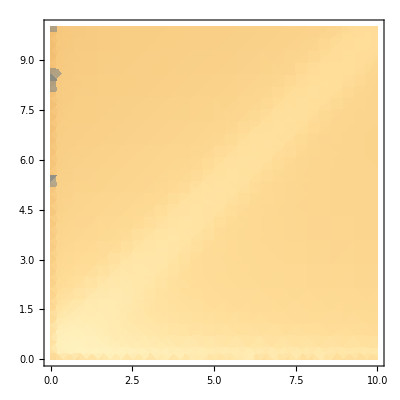

there is nothing wrong with the mermin dielectric

```mathematica
DensityPlot[Log10[Im[-1/ϵM[u,z,(2"νi")/("vF""qF" z)/.FeTotalparams[[2]]]]]/.FeTotalparams[[2]],{u,0,10},{z,0,10},PlotRange->All]
Print["there is nothing wrong with the mermin dielectric"]
```

```mathematica
Print["still good, so probably just issue with bounds. Check we have done the variable conversion right, and compare the two definitions"]
Solve[u==ω/(vF k)/.k->2 kF z,ω]
Solve[z==k/(2 kF),k]
Solve[uν==ν/(vF k)/.k->2 kF z,ν]
Im[-1/ϵMωq[2 "qF""vF"z u,2 "qF"z,"νi","qF","vF"]]/.FeTotalparams[[2]]/.u->10/.z->10
Im[-1/ϵM[u,z,("νi")/(2 "vF""qF" z)]]/.FeTotalparams[[2]]/.u->10/.z->10
```

still good, so probably just issue with bounds. Check we have done the variable conversion right, and compare the two definitions

{{ω→2 kF u vF z}}

{{k→2 kF z}}

{{ν→2 kF uν vF z}}

0.000132373

0.000132373

```mathematica
Print["So it is just a bounds issue. What is q_max in terms of z? try plugging that in and see what happens"]

(Setest[["qrange"]][[2]])/(2 "qF")/.FeTotalparams[[2]]
(Setest[["ωrange"]][[1]])/(2 "vF" Setest[["qrange"]][[1]])/.FeTotalparams[[2]]
(Setest[["ωrange"]][[1]])/(2 "vF" Setest[["qrange"]][[2]])/.FeTotalparams[[2]]
(Setest[["ωrange"]][[2]])/(2 "vF" Setest[["qrange"]])/.FeTotalparams[[2]]
Im[-1/ϵM[u,z,("νi")/(2 "vF""qF" z)]]/.FeTotalparams[[2]]/.u->10/.z->10
Im[-1/ϵM[u,z,("νi")/(2 "vF""qF" z)]]/.FeTotalparams[[2]]/.u->5 10^-5/.z->0.9
```

So it is just a bounds issue. What is q_max in terms of z? try plugging that in and see what happens

1.45267

0.00307891

0.0000307891

{72.6334,0.726334}

0.000132373

0.0000200269

```mathematica
Print["It doesn't seem like the issue is that q or ω is too large. Let's calculate u,z explicitly."]
```

```mathematica
Table[{(Setest["ωs"][[i]])/(2 "vF"Setest["qs"][[j]]),(Setest["qs"][[j]])/(2 "qF"),("νi")/(2 "vF"Setest["qs"][[j]])},{i,Length[Setest["ωs"]]},{j,Length[Setest["qs"]]}]/.FeTotalparams[[2]]
Print["Seem like reasonable values, try evaluating the dielectric on them"]
```

{{{0.00307891,0.0145267,4.20556},{0.00244567,0.018288,3.3406},{0.00194266,0.0230232,2.65353},{0.00154311,0.0289845,2.10777},{0.00122574,0.0364894,1.67426},{0.000973638,0.0459374,1.32992},{0.000773388,0.0578317,1.05639},{0.000614324,0.0728058,0.83912},{0.000487975,0.0916571,0.666537},{0.000387612,0.115389,0.529449},{0.000307891,0.145267,0.420556},{0.000244567,0.18288,0.33406},{0.000194266,0.230232,0.265353},{0.000154311,0.289845,0.210777},{0.000122574,0.364894,0.167426},{0.0000973638,0.459374,0.132992},{0.0000773388,0.578317,0.105639},{0.0000614324,0.728058,0.083912},{0.0000487975,0.916571,0.0666537},{0.0000387612,1.15389,0.0529449},{0.0000307891,1.45267,0.0420556}},{{0.00509371,0.0145267,4.20556},{0.00404608,0.018288,3.3406},{0.00321392,0.0230232,2.65353},{0.0025529,0.0289845,2.10777},{0.00202784,0.0364894,1.67426},{0.00161077,0.0459374,1.32992},{0.00127948,0.0578317,1.05639},{0.00101633,0.0728058,0.83912},{0.000807299,0.0916571,0.666537},{0.00064126,0.115389,0.529449},{0.000509371,0.145267,0.420556},{0.000404608,0.18288,0.33406},{0.000321392,0.230232,0.265353},{0.00025529,0.289845,0.210777},{0.000202784,0.364894,0.167426},{0.000161077,0.459374,0.132992},{0.000127948,0.578317,0.105639},{0.000101633,0.728058,0.083912},{0.0000807299,0.916571,0.0666537},{0.000064126,1.15389,0.0529449},{0.0000509371,1.45267,0.0420556}},{{0.00842697,0.0145267,4.20556},{0.00669378,0.018288,3.3406},{0.00531706,0.0230232,2.65353},{0.00422349,0.0289845,2.10777},{0.00335484,0.0364894,1.67426},{0.00266484,0.0459374,1.32992},{0.00211676,0.0578317,1.05639},{0.0016814,0.0728058,0.83912},{0.00133558,0.0916571,0.666537},{0.00106089,0.115389,0.529449},{0.000842697,0.145267,0.420556},{0.000669378,0.18288,0.33406},{0.000531706,0.230232,0.265353},{0.000422349,0.289845,0.210777},{0.000335484,0.364894,0.167426},{0.000266484,0.459374,0.132992},{0.000211676,0.578317,0.105639},{0.00016814,0.728058,0.083912},{0.000133558,0.916571,0.0666537},{0.000106089,1.15389,0.0529449},{0.0000842697,1.45267,0.0420556}},{{0.0139415,0.0145267,4.20556},{0.0110741,0.018288,3.3406},{0.00879647,0.0230232,2.65353},{0.00698728,0.0289845,2.10777},{0.0055502,0.0364894,1.67426},{0.00440868,0.0459374,1.32992},{0.00350194,0.0578317,1.05639},{0.00278169,0.0728058,0.83912},{0.00220957,0.0916571,0.666537},{0.00175513,0.115389,0.529449},{0.00139415,0.145267,0.420556},{0.00110741,0.18288,0.33406},{0.000879647,0.230232,0.265353},{0.000698728,0.289845,0.210777},{0.00055502,0.364894,0.167426},{0.000440868,0.459374,0.132992},{0.000350194,0.578317,0.105639},{0.000278169,0.728058,0.083912},{0.000220957,0.916571,0.0666537},{0.000175513,1.15389,0.0529449},{0.000139415,1.45267,0.0420556}},{{0.0230646,0.0145267,4.20556},{0.0183208,0.018288,3.3406},{0.0145528,0.0230232,2.65353},{0.0115597,0.0289845,2.10777},{0.00918217,0.0364894,1.67426},{0.00729366,0.0459374,1.32992},{0.00579356,0.0578317,1.05639},{0.00460199,0.0728058,0.83912},{0.00365549,0.0916571,0.666537},{0.00290366,0.115389,0.529449},{0.00230646,0.145267,0.420556},{0.00183208,0.18288,0.33406},{0.00145528,0.230232,0.265353},{0.00115597,0.289845,0.210777},{0.000918217,0.364894,0.167426},{0.000729366,0.459374,0.132992},{0.000579356,0.578317,0.105639},{0.000460199,0.728058,0.083912},{0.000365549,0.916571,0.0666537},{0.000290366,1.15389,0.0529449},{0.000230646,1.45267,0.0420556}},{{0.0381577,0.0145267,4.20556},{0.0303097,0.018288,3.3406},{0.0240759,0.0230232,2.65353},{0.0191242,0.0289845,2.10777},{0.0151909,0.0364894,1.67426},{0.0120665,0.0459374,1.32992},{0.00958478,0.0578317,1.05639},{0.00761346,0.0728058,0.83912},{0.00604759,0.0916571,0.666537},{0.00480377,0.115389,0.529449},{0.00381577,0.145267,0.420556},{0.00303097,0.18288,0.33406},{0.00240759,0.230232,0.265353},{0.00191242,0.289845,0.210777},{0.00151909,0.364894,0.167426},{0.00120665,0.459374,0.132992},{0.000958478,0.578317,0.105639},{0.000761346,0.728058,0.083912},{0.000604759,0.916571,0.0666537},{0.000480377,1.15389,0.0529449},{0.000381577,1.45267,0.0420556}},{{0.0631276,0.0145267,4.20556},{0.050144,0.018288,3.3406},{0.0398308,0.0230232,2.65353},{0.0316387,0.0289845,2.10777},{0.0251315,0.0364894,1.67426},{0.0199627,0.0459374,1.32992},{0.0158569,0.0578317,1.05639},{0.0125956,0.0728058,0.83912},{0.010005,0.0916571,0.666537},{0.00794729,0.115389,0.529449},{0.00631276,0.145267,0.420556},{0.0050144,0.18288,0.33406},{0.00398308,0.230232,0.265353},{0.00316387,0.289845,0.210777},{0.00251315,0.364894,0.167426},{0.00199627,0.459374,0.132992},{0.00158569,0.578317,0.105639},{0.00125956,0.728058,0.083912},{0.0010005,0.916571,0.0666537},{0.000794729,1.15389,0.0529449},{0.000631276,1.45267,0.0420556}},{{0.104437,0.0145267,4.20556},{0.0829576,0.018288,3.3406},{0.0658955,0.0230232,2.65353},{0.0523427,0.0289845,2.10777},{0.0415773,0.0364894,1.67426},{0.033026,0.0459374,1.32992},{0.0262335,0.0578317,1.05639},{0.020838,0.0728058,0.83912},{0.0165522,0.0916571,0.666537},{0.0131479,0.115389,0.529449},{0.0104437,0.145267,0.420556},{0.00829576,0.18288,0.33406},{0.00658955,0.230232,0.265353},{0.00523427,0.289845,0.210777},{0.00415773,0.364894,0.167426},{0.0033026,0.459374,0.132992},{0.00262335,0.578317,0.105639},{0.0020838,0.728058,0.083912},{0.00165522,0.916571,0.0666537},{0.00131479,1.15389,0.0529449},{0.00104437,1.45267,0.0420556}},{{0.17278,0.0145267,4.20556},{0.137244,0.018288,3.3406},{0.109017,0.0230232,2.65353},{0.086595,0.0289845,2.10777},{0.0687849,0.0364894,1.67426},{0.0546378,0.0459374,1.32992},{0.0434003,0.0578317,1.05639},{0.0344741,0.0728058,0.83912},{0.0273838,0.0916571,0.666537},{0.0217517,0.115389,0.529449},{0.017278,0.145267,0.420556},{0.0137244,0.18288,0.33406},{0.0109017,0.230232,0.265353},{0.0086595,0.289845,0.210777},{0.00687849,0.364894,0.167426},{0.00546378,0.459374,0.132992},{0.00434003,0.578317,0.105639},{0.00344741,0.728058,0.083912},{0.00273838,0.916571,0.0666537},{0.00217517,1.15389,0.0529449},{0.0017278,1.45267,0.0420556}},{{0.285845,0.0145267,4.20556},{0.227054,0.018288,3.3406},{0.180356,0.0230232,2.65353},{0.143262,0.0289845,2.10777},{0.113797,0.0364894,1.67426},{0.090392,0.0459374,1.32992},{0.0718009,0.0578317,1.05639},{0.0570335,0.0728058,0.83912},{0.0453033,0.0916571,0.666537},{0.0359857,0.115389,0.529449},{0.0285845,0.145267,0.420556},{0.0227054,0.18288,0.33406},{0.0180356,0.230232,0.265353},{0.0143262,0.289845,0.210777},{0.0113797,0.364894,0.167426},{0.0090392,0.459374,0.132992},{0.00718009,0.578317,0.105639},{0.00570335,0.728058,0.083912},{0.00453033,0.916571,0.0666537},{0.00359857,1.15389,0.0529449},{0.00285845,1.45267,0.0420556}},{{0.472897,0.0145267,4.20556},{0.375636,0.018288,3.3406},{0.298378,0.0230232,2.65353},{0.23701,0.0289845,2.10777},{0.188264,0.0364894,1.67426},{0.149543,0.0459374,1.32992},{0.118786,0.0578317,1.05639},{0.0943554,0.0728058,0.83912},{0.0749492,0.0916571,0.666537},{0.0595343,0.115389,0.529449},{0.0472897,0.145267,0.420556},{0.0375636,0.18288,0.33406},{0.0298378,0.230232,0.265353},{0.023701,0.289845,0.210777},{0.0188264,0.364894,0.167426},{0.0149543,0.459374,0.132992},{0.0118786,0.578317,0.105639},{0.00943554,0.728058,0.083912},{0.00749492,0.916571,0.0666537},{0.00595343,1.15389,0.0529449},{0.00472897,1.45267,0.0420556}},{{0.782355,0.0145267,4.20556},{0.621447,0.018288,3.3406},{0.493633,0.0230232,2.65353},{0.392106,0.0289845,2.10777},{0.311461,0.0364894,1.67426},{0.247402,0.0459374,1.32992},{0.196519,0.0578317,1.05639},{0.1561,0.0728058,0.83912},{0.123995,0.0916571,0.666537},{0.0984927,0.115389,0.529449},{0.0782355,0.145267,0.420556},{0.0621447,0.18288,0.33406},{0.0493633,0.230232,0.265353},{0.0392106,0.289845,0.210777},{0.0311461,0.364894,0.167426},{0.0247402,0.459374,0.132992},{0.0196519,0.578317,0.105639},{0.01561,0.728058,0.083912},{0.0123995,0.916571,0.0666537},{0.00984927,1.15389,0.0529449},{0.00782355,1.45267,0.0420556}},{{1.29432,0.0145267,4.20556},{1.02811,0.018288,3.3406},{0.816659,0.0230232,2.65353},{0.648695,0.0289845,2.10777},{0.515277,0.0364894,1.67426},{0.409299,0.0459374,1.32992},{0.325118,0.0578317,1.05639},{0.25825,0.0728058,0.83912},{0.205135,0.0916571,0.666537},{0.162945,0.115389,0.529449},{0.129432,0.145267,0.420556},{0.102811,0.18288,0.33406},{0.0816659,0.230232,0.265353},{0.0648695,0.289845,0.210777},{0.0515277,0.364894,0.167426},{0.0409299,0.459374,0.132992},{0.0325118,0.578317,0.105639},{0.025825,0.728058,0.083912},{0.0205135,0.916571,0.0666537},{0.0162945,1.15389,0.0529449},{0.0129432,1.45267,0.0420556}},{{2.1413,0.0145267,4.20556},{1.7009,0.018288,3.3406},{1.35107,0.0230232,2.65353},{1.07319,0.0289845,2.10777},{0.852467,0.0364894,1.67426},{0.677139,0.0459374,1.32992},{0.53787,0.0578317,1.05639},{0.427246,0.0728058,0.83912},{0.339373,0.0916571,0.666537},{0.269574,0.115389,0.529449},{0.21413,0.145267,0.420556},{0.17009,0.18288,0.33406},{0.135107,0.230232,0.265353},{0.107319,0.289845,0.210777},{0.0852467,0.364894,0.167426},{0.0677139,0.459374,0.132992},{0.053787,0.578317,0.105639},{0.0427246,0.728058,0.083912},{0.0339373,0.916571,0.0666537},{0.0269574,1.15389,0.0529449},{0.021413,1.45267,0.0420556}},{{3.54254,0.0145267,4.20556},{2.81394,0.018288,3.3406},{2.23519,0.0230232,2.65353},{1.77548,0.0289845,2.10777},{1.41031,0.0364894,1.67426},{1.12025,0.0459374,1.32992},{0.889846,0.0578317,1.05639},{0.706829,0.0728058,0.83912},{0.561455,0.0916571,0.666537},{0.445979,0.115389,0.529449},{0.354254,0.145267,0.420556},{0.281394,0.18288,0.33406},{0.223519,0.230232,0.265353},{0.177548,0.289845,0.210777},{0.141031,0.364894,0.167426},{0.112025,0.459374,0.132992},{0.0889846,0.578317,0.105639},{0.0706829,0.728058,0.083912},{0.0561455,0.916571,0.0666537},{0.0445979,1.15389,0.0529449},{0.0354254,1.45267,0.0420556}},{{5.86073,0.0145267,4.20556},{4.65534,0.018288,3.3406},{3.69787,0.0230232,2.65353},{2.93732,0.0289845,2.10777},{2.3332,0.0364894,1.67426},{1.85332,0.0459374,1.32992},{1.47215,0.0578317,1.05639},{1.16937,0.0728058,0.83912},{0.928863,0.0916571,0.666537},{0.737822,0.115389,0.529449},{0.586073,0.145267,0.420556},{0.465534,0.18288,0.33406},{0.369787,0.230232,0.265353},{0.293732,0.289845,0.210777},{0.23332,0.364894,0.167426},{0.185332,0.459374,0.132992},{0.147215,0.578317,0.105639},{0.116937,0.728058,0.083912},{0.0928863,0.916571,0.0666537},{0.0737822,1.15389,0.0529449},{0.0586073,1.45267,0.0420556}},{{9.69591,0.0145267,4.20556},{7.70173,0.018288,3.3406},{6.1177,0.0230232,2.65353},{4.85947,0.0289845,2.10777},{3.86001,0.0364894,1.67426},{3.06612,0.0459374,1.32992},{2.4355,0.0578317,1.05639},{1.93459,0.0728058,0.83912},{1.5367,0.0916571,0.666537},{1.22064,0.115389,0.529449},{0.969591,0.145267,0.420556},{0.770173,0.18288,0.33406},{0.61177,0.230232,0.265353},{0.485947,0.289845,0.210777},{0.386001,0.364894,0.167426},{0.306612,0.459374,0.132992},{0.24355,0.578317,0.105639},{0.193459,0.728058,0.083912},{0.15367,0.916571,0.0666537},{0.122064,1.15389,0.0529449},{0.0969591,1.45267,0.0420556}},{{16.0408,0.0145267,4.20556},{12.7416,0.018288,3.3406},{10.121,0.0230232,2.65353},{8.03943,0.0289845,2.10777},{6.38595,0.0364894,1.67426},{5.07254,0.0459374,1.32992},{4.02926,0.0578317,1.05639},{3.20056,0.0728058,0.83912},{2.54229,0.0916571,0.666537},{2.01941,0.115389,0.529449},{1.60408,0.145267,0.420556},{1.27416,0.18288,0.33406},{1.0121,0.230232,0.265353},{0.803943,0.289845,0.210777},{0.638595,0.364894,0.167426},{0.507254,0.459374,0.132992},{0.402926,0.578317,0.105639},{0.320056,0.728058,0.083912},{0.254229,0.916571,0.0666537},{0.201941,1.15389,0.0529449},{0.160408,1.45267,0.0420556}},{{26.5376,0.0145267,4.20556},{21.0796,0.018288,3.3406},{16.7441,0.0230232,2.65353},{13.3003,0.0289845,2.10777},{10.5648,0.0364894,1.67426},{8.39194,0.0459374,1.32992},{6.66596,0.0578317,1.05639},{5.29496,0.0728058,0.83912},{4.20593,0.0916571,0.666537},{3.34089,0.115389,0.529449},{2.65376,0.145267,0.420556},{2.10796,0.18288,0.33406},{1.67441,0.230232,0.265353},{1.33003,0.289845,0.210777},{1.05648,0.364894,0.167426},{0.839194,0.459374,0.132992},{0.666596,0.578317,0.105639},{0.529496,0.728058,0.083912},{0.420593,0.916571,0.0666537},{0.334089,1.15389,0.0529449},{0.265376,1.45267,0.0420556}},{{43.9035,0.0145267,4.20556},{34.8738,0.018288,3.3406},{27.7012,0.0230232,2.65353},{22.0039,0.0289845,2.10777},{17.4783,0.0364894,1.67426},{13.8835,0.0459374,1.32992},{11.0281,0.0578317,1.05639},{8.7599,0.0728058,0.83912},{6.95824,0.0916571,0.666537},{5.52713,0.115389,0.529449},{4.39035,0.145267,0.420556},{3.48738,0.18288,0.33406},{2.77012,0.230232,0.265353},{2.20039,0.289845,0.210777},{1.74783,0.364894,0.167426},{1.38835,0.459374,0.132992},{1.10281,0.578317,0.105639},{0.87599,0.728058,0.083912},{0.695824,0.916571,0.0666537},{0.552713,1.15389,0.0529449},{0.439035,1.45267,0.0420556}},{{72.6334,0.0145267,4.20556},{57.6947,0.018288,3.3406},{45.8286,0.0230232,2.65353},{36.4029,0.0289845,2.10777},{28.9159,0.0364894,1.67426},{22.9687,0.0459374,1.32992},{18.2447,0.0578317,1.05639},{14.4923,0.0728058,0.83912},{11.5116,0.0916571,0.666537},{9.144,0.115389,0.529449},{7.26334,0.145267,0.420556},{5.76947,0.18288,0.33406},{4.58286,0.230232,0.265353},{3.64029,0.289845,0.210777},{2.89159,0.364894,0.167426},{2.29687,0.459374,0.132992},{1.82447,0.578317,0.105639},{1.44923,0.728058,0.083912},{1.15116,0.916571,0.0666537},{0.9144,1.15389,0.0529449},{0.726334,1.45267,0.0420556}}}

Seem like reasonable values, try evaluating the dielectric on them

```mathematica
Table[Im[-1/ϵM[(Setest["ωs"][[i]])/(2 "vF"Setest["qs"][[j]]),(Setest["qs"][[j]])/(2 "qF"),("νi")/(2 "vF"Setest["qs"][[j]])]]/.FeTotalparams[[2]],{i,Length[Setest["ωs"]]},{j,Length[Setest["qs"]]}]
Print["These also seem reasonable. Try interpolating. "]
```

{{0.0000246178,0.0000248063,0.0000250983,0.0000255453,0.000026218,0.0000272068,0.0000286171,0.0000305542,0.0000330982,0.0000362642,0.0000399423,0.0000438131,0.0000472522,0.0000492945,0.0000487999,0.0000449475,0.0000378884,0.000028936,0.000019124,4.11225×10^-7,3.12124×10^-8},{0.0000407273,0.0000410392,0.0000415223,0.0000422618,0.0000433746,0.0000450106,0.0000473437,0.0000505484,0.0000547573,0.000059995,0.0000660801,0.0000724838,0.0000781734,0.0000815521,0.0000807339,0.0000743604,0.0000626821,0.0000478713,0.0000316384,6.80324×10^-7,5.16373×10^-8},{0.0000673787,0.0000678947,0.0000686939,0.0000699174,0.0000717584,0.0000744649,0.0000783248,0.0000836267,0.0000905896,0.000099255,0.000109322,0.000119916,0.000129329,0.000134919,0.000133565,0.000123021,0.0001037,0.0000791976,0.0000523422,1.12552×10^-6,8.54281×10^-8},{0.00011147,0.000112324,0.000113646,0.00011567,0.000118716,0.000123194,0.00012958,0.000138351,0.00014987,0.000164206,0.000180861,0.000198388,0.00021396,0.000223208,0.000220968,0.000203524,0.000171561,0.000131023,0.0000865942,1.86204×10^-6,1.41331×10^-7},{0.000184415,0.000185828,0.000188015,0.000191363,0.000196402,0.00020381,0.000214374,0.000228886,0.000247943,0.00027166,0.000299214,0.00032821,0.000353973,0.000369272,0.000365567,0.000336708,0.000283828,0.000216763,0.00014326,3.08054×10^-6,2.33816×10^-7},{0.000305095,0.000307431,0.00031105,0.000316589,0.000324925,0.00033718,0.000354658,0.000378665,0.000410193,0.000449431,0.000495015,0.000542986,0.000585608,0.000610919,0.000604789,0.000557045,0.000469561,0.00035861,0.000237007,5.09643×10^-6,3.86823×10^-7},{0.000504749,0.000508613,0.0005146,0.000523763,0.000537553,0.000557826,0.00058674,0.000626455,0.000678616,0.00074353,0.000818945,0.00089831,0.000968824,0.0010107,0.00100056,0.000921569,0.000776836,0.00059328,0.0003921,8.43154×10^-6,6.39955×10^-7},{0.000835066,0.000841457,0.000851357,0.000866513,0.000889321,0.000922856,0.000970686,0.00103639,0.00112268,0.00123008,0.00135485,0.00148615,0.00160281,0.00167209,0.00165532,0.00152464,0.00128519,0.000981516,0.000648679,0.0000139494,1.05873×10^-6},{0.0013816,0.00139216,0.00140852,0.00143358,0.00147129,0.00152675,0.00160586,0.00171455,0.00185731,0.002035,0.00224144,0.00245868,0.0026517,0.00276632,0.00273857,0.00252237,0.00212622,0.00162381,0.00107313,0.0000230792,1.75157×10^-6},{0.00228603,0.00230346,0.00233047,0.00237183,0.00243412,0.00252576,0.00265656,0.00283633,0.00307253,0.00336655,0.00370816,0.00406766,0.00438706,0.00457672,0.0045308,0.00417309,0.00351766,0.00268645,0.00177524,0.0000381891,2.89783×10^-6},{0.00378353,0.00381215,0.00385653,0.00392457,0.00402715,0.00417829,0.00439429,0.00469152,0.00508233,0.00556901,0.00613455,0.0067297,0.00725843,0.00757238,0.00749641,0.00690446,0.00581992,0.00444456,0.00293631,0.0000632121,4.79437×10^-6},{0.00626646,0.00631287,0.00638497,0.00649579,0.00666342,0.0069113,0.00726688,0.00775768,0.00840444,0.00921075,0.0101481,0.0111345,0.0120107,0.0125309,0.0124052,0.0114252,0.00962997,0.00735363,0.00485493,0.000104725,7.93284×10^-6},{0.0103997,0.0104725,0.0105861,0.0107617,0.0110297,0.0114298,0.0120097,0.0128171,0.0138876,0.0152266,0.0167851,0.0184253,0.0198816,0.0207457,0.0205376,0.0189132,0.0159388,0.0121685,0.00801886,0.000173927,0.000013129},{0.0173604,0.017465,0.01763,0.0178888,0.0182912,0.0189072,0.0198244,0.0211342,0.0229033,0.0251394,0.0277524,0.0305034,0.0329429,0.0343887,0.0340437,0.031342,0.0264014,0.020144,0.0132054,0.000290828,0.0000217433},{0.0294933,0.0296169,0.0298144,0.030131,0.03064,0.0314577,0.0327559,0.0347474,0.0376093,0.0413709,0.0458408,0.0505614,0.0547366,0.0572023,0.0566273,0.0520913,0.0438258,0.0333817,0.0215514,0.000495701,0.0000360754},{0.0528521,0.0529496,0.0531068,0.0533632,0.0537875,0.0545048,0.0557493,0.0579522,0.0617772,0.0677579,0.0756005,0.0841453,0.0916972,0.0961136,0.095127,0.0872976,0.0731851,0.0554659,0.0341808,0.000894119,0.0000601571},{0.111756,0.111746,0.111734,0.111718,0.111705,0.111717,0.111821,0.112219,0.113522,0.117483,0.127401,0.143034,0.158179,0.166866,0.164756,0.149945,0.124287,0.0925805,0.0507808,0.00194845,0.000101739},{0.44464,0.44383,0.442552,0.44054,0.437385,0.43247,0.424891,0.413396,0.396442,0.372653,0.34268,0.316712,0.322054,0.334361,0.320092,0.278987,0.219847,0.149753,0.0714343,0.00694976,0.000179279},{1.43294,1.43716,1.44389,1.45463,1.47189,1.49983,1.5456,1.62208,1.75385,1.99175,2.44885,3.33814,4.06968,1.95437,0.911554,0.581636,0.369861,0.213101,0.0992077,0.021934,0.000361883},{0.0498057,0.0498342,0.0498793,0.0499511,0.0500654,0.0502478,0.0505401,0.0510116,0.0517805,0.0530561,0.0552337,0.0591372,0.0667673,0.0844151,0.144855,0.661675,0.534424,0.279386,0.134515,0.0464079,0.00164106},{0.00721319,0.00721446,0.00721648,0.00721968,0.00722478,0.00723289,0.00724583,0.00726653,0.00729986,0.00735401,0.0074433,0.00759404,0.00785845,0.0083527,0.00938497,0.0120655,0.0247463,0.196228,0.154701,0.0742,0.0179095}}

These also seem reasonable. Try interpolating.

```mathematica
ϵinterpoints=Flatten[Table[{{(Setest["ωs"][[i]])/(2 "vF"Setest["qs"][[j]]),(Setest["qs"][[j]])/(2 "qF")},Im[-1/ϵM[(Setest["ωs"][[i]])/(2 "vF"Setest["qs"][[j]]),(Setest["qs"][[j]])/(2 "qF"),("νi")/(2 "vF"Setest["qs"][[j]])]]}/.FeTotalparams[[2]],{i,Length[Setest["ωs"]]},{j,Length[Setest["qs"]]}],1]
```

{{{0.00307891,0.0145267},0.0000246178},{{0.00244567,0.018288},0.0000248063},{{0.00194266,0.0230232},0.0000250983},{{0.00154311,0.0289845},0.0000255453},{{0.00122574,0.0364894},0.000026218},{{0.000973638,0.0459374},0.0000272068},{{0.000773388,0.0578317},0.0000286171},{{0.000614324,0.0728058},0.0000305542},{{0.000487975,0.0916571},0.0000330982},{{0.000387612,0.115389},0.0000362642},{{0.000307891,0.145267},0.0000399423},{{0.000244567,0.18288},0.0000438131},{{0.000194266,0.230232},0.0000472522},{{0.000154311,0.289845},0.0000492945},{{0.000122574,0.364894},0.0000487999},{{0.0000973638,0.459374},0.0000449475},{{0.0000773388,0.578317},0.0000378884},{{0.0000614324,0.728058},0.000028936},{{0.0000487975,0.916571},0.000019124},{{0.0000387612,1.15389},4.11225×10^-7},{{0.0000307891,1.45267},3.12124×10^-8},{{0.00509371,0.0145267},0.0000407273},{{0.00404608,0.018288},0.0000410392},{{0.00321392,0.0230232},0.0000415223},{{0.0025529,0.0289845},0.0000422618},{{0.00202784,0.0364894},0.0000433746},{{0.00161077,0.0459374},0.0000450106},{{0.00127948,0.0578317},0.0000473437},{{0.00101633,0.0728058},0.0000505484},{{0.000807299,0.0916571},0.0000547573},{{0.00064126,0.115389},0.000059995},{{0.000509371,0.145267},0.0000660801},{{0.000404608,0.18288},0.0000724838},{{0.000321392,0.230232},0.0000781734},{{0.00025529,0.289845},0.0000815521},{{0.000202784,0.364894},0.0000807339},{{0.000161077,0.459374},0.0000743604},{{0.000127948,0.578317},0.0000626821},{{0.000101633,0.728058},0.0000478713},{{0.0000807299,0.916571},0.0000316384},{{0.000064126,1.15389},6.80324×10^-7},{{0.0000509371,1.45267},5.16373×10^-8},{{0.00842697,0.0145267},0.0000673787},{{0.00669378,0.018288},0.0000678947},{{0.00531706,0.0230232},0.0000686939},{{0.00422349,0.0289845},0.0000699174},{{0.00335484,0.0364894},0.0000717584},{{0.00266484,0.0459374},0.0000744649},{{0.00211676,0.0578317},0.0000783248},{{0.0016814,0.0728058},0.0000836267},{{0.00133558,0.0916571},0.0000905896},{{0.00106089,0.115389},0.000099255},{{0.000842697,0.145267},0.000109322},{{0.000669378,0.18288},0.000119916},{{0.000531706,0.230232},0.000129329},{{0.000422349,0.289845},0.000134919},{{0.000335484,0.364894},0.000133565},{{0.000266484,0.459374},0.000123021},{{0.000211676,0.578317},0.0001037},{{0.00016814,0.728058},0.0000791976},{{0.000133558,0.916571},0.0000523422},{{0.000106089,1.15389},1.12552×10^-6},{{0.0000842697,1.45267},8.54281×10^-8},{{0.0139415,0.0145267},0.00011147},{{0.0110741,0.018288},0.000112324},{{0.00879647,0.0230232},0.000113646},{{0.00698728,0.0289845},0.00011567},{{0.0055502,0.0364894},0.000118716},{{0.00440868,0.0459374},0.000123194},{{0.00350194,0.0578317},0.00012958},{{0.00278169,0.0728058},0.000138351},{{0.00220957,0.0916571},0.00014987},{{0.00175513,0.115389},0.000164206},{{0.00139415,0.145267},0.000180861},{{0.00110741,0.18288},0.000198388},{{0.000879647,0.230232},0.00021396},{{0.000698728,0.289845},0.000223208},{{0.00055502,0.364894},0.000220968},{{0.000440868,0.459374},0.000203524},{{0.000350194,0.578317},0.000171561},{{0.000278169,0.728058},0.000131023},{{0.000220957,0.916571},0.0000865942},{{0.000175513,1.15389},1.86204×10^-6},{{0.000139415,1.45267},1.41331×10^-7},{{0.0230646,0.0145267},0.000184415},{{0.0183208,0.018288},0.000185828},{{0.0145528,0.0230232},0.000188015},{{0.0115597,0.0289845},0.000191363},{{0.00918217,0.0364894},0.000196402},{{0.00729366,0.0459374},0.00020381},{{0.00579356,0.0578317},0.000214374},{{0.00460199,0.0728058},0.000228886},{{0.00365549,0.0916571},0.000247943},{{0.00290366,0.115389},0.00027166},{{0.00230646,0.145267},0.000299214},{{0.00183208,0.18288},0.00032821},{{0.00145528,0.230232},0.000353973},{{0.00115597,0.289845},0.000369272},{{0.000918217,0.364894},0.000365567},{{0.000729366,0.459374},0.000336708},{{0.000579356,0.578317},0.000283828},{{0.000460199,0.728058},0.000216763},{{0.000365549,0.916571},0.00014326},{{0.000290366,1.15389},3.08054×10^-6},{{0.000230646,1.45267},2.33816×10^-7},{{0.0381577,0.0145267},0.000305095},{{0.0303097,0.018288},0.000307431},{{0.0240759,0.0230232},0.00031105},{{0.0191242,0.0289845},0.000316589},{{0.0151909,0.0364894},0.000324925},{{0.0120665,0.0459374},0.00033718},{{0.00958478,0.0578317},0.000354658},{{0.00761346,0.0728058},0.000378665},{{0.00604759,0.0916571},0.000410193},{{0.00480377,0.115389},0.000449431},{{0.00381577,0.145267},0.000495015},{{0.00303097,0.18288},0.000542986},{{0.00240759,0.230232},0.000585608},{{0.00191242,0.289845},0.000610919},{{0.00151909,0.364894},0.000604789},{{0.00120665,0.459374},0.000557045},{{0.000958478,0.578317},0.000469561},{{0.000761346,0.728058},0.00035861},{{0.000604759,0.916571},0.000237007},{{0.000480377,1.15389},5.09643×10^-6},{{0.000381577,1.45267},3.86823×10^-7},{{0.0631276,0.0145267},0.000504749},{{0.050144,0.018288},0.000508613},{{0.0398308,0.0230232},0.0005146},{{0.0316387,0.0289845},0.000523763},{{0.0251315,0.0364894},0.000537553},{{0.0199627,0.0459374},0.000557826},{{0.0158569,0.0578317},0.00058674},{{0.0125956,0.0728058},0.000626455},{{0.010005,0.0916571},0.000678616},{{0.00794729,0.115389},0.00074353},{{0.00631276,0.145267},0.000818945},{{0.0050144,0.18288},0.00089831},{{0.00398308,0.230232},0.000968824},{{0.00316387,0.289845},0.0010107},{{0.00251315,0.364894},0.00100056},{{0.00199627,0.459374},0.000921569},{{0.00158569,0.578317},0.000776836},{{0.00125956,0.728058},0.00059328},{{0.0010005,0.916571},0.0003921},{{0.000794729,1.15389},8.43154×10^-6},{{0.000631276,1.45267},6.39955×10^-7},{{0.104437,0.0145267},0.000835066},{{0.0829576,0.018288},0.000841457},{{0.0658955,0.0230232},0.000851357},{{0.0523427,0.0289845},0.000866513},{{0.0415773,0.0364894},0.000889321},{{0.033026,0.0459374},0.000922856},{{0.0262335,0.0578317},0.000970686},{{0.020838,0.0728058},0.00103639},{{0.0165522,0.0916571},0.00112268},{{0.0131479,0.115389},0.00123008},{{0.0104437,0.145267},0.00135485},{{0.00829576,0.18288},0.00148615},{{0.00658955,0.230232},0.00160281},{{0.00523427,0.289845},0.00167209},{{0.00415773,0.364894},0.00165532},{{0.0033026,0.459374},0.00152464},{{0.00262335,0.578317},0.00128519},{{0.0020838,0.728058},0.000981516},{{0.00165522,0.916571},0.000648679},{{0.00131479,1.15389},0.0000139494},{{0.00104437,1.45267},1.05873×10^-6},{{0.17278,0.0145267},0.0013816},{{0.137244,0.018288},0.00139216},{{0.109017,0.0230232},0.00140852},{{0.086595,0.0289845},0.00143358},{{0.0687849,0.0364894},0.00147129},{{0.0546378,0.0459374},0.00152675},{{0.0434003,0.0578317},0.00160586},{{0.0344741,0.0728058},0.00171455},{{0.0273838,0.0916571},0.00185731},{{0.0217517,0.115389},0.002035},{{0.017278,0.145267},0.00224144},{{0.0137244,0.18288},0.00245868},{{0.0109017,0.230232},0.0026517},{{0.0086595,0.289845},0.00276632},{{0.00687849,0.364894},0.00273857},{{0.00546378,0.459374},0.00252237},{{0.00434003,0.578317},0.00212622},{{0.00344741,0.728058},0.00162381},{{0.00273838,0.916571},0.00107313},{{0.00217517,1.15389},0.0000230792},{{0.0017278,1.45267},1.75157×10^-6},{{0.285845,0.0145267},0.00228603},{{0.227054,0.018288},0.00230346},{{0.180356,0.0230232},0.00233047},{{0.143262,0.0289845},0.00237183},{{0.113797,0.0364894},0.00243412},{{0.090392,0.0459374},0.00252576},{{0.0718009,0.0578317},0.00265656},{{0.0570335,0.0728058},0.00283633},{{0.0453033,0.0916571},0.00307253},{{0.0359857,0.115389},0.00336655},{{0.0285845,0.145267},0.00370816},{{0.0227054,0.18288},0.00406766},{{0.0180356,0.230232},0.00438706},{{0.0143262,0.289845},0.00457672},{{0.0113797,0.364894},0.0045308},{{0.0090392,0.459374},0.00417309},{{0.00718009,0.578317},0.00351766},{{0.00570335,0.728058},0.00268645},{{0.00453033,0.916571},0.00177524},{{0.00359857,1.15389},0.0000381891},{{0.00285845,1.45267},2.89783×10^-6},{{0.472897,0.0145267},0.00378353},{{0.375636,0.018288},0.00381215},{{0.298378,0.0230232},0.00385653},{{0.23701,0.0289845},0.00392457},{{0.188264,0.0364894},0.00402715},{{0.149543,0.0459374},0.00417829},{{0.118786,0.0578317},0.00439429},{{0.0943554,0.0728058},0.00469152},{{0.0749492,0.0916571},0.00508233},{{0.0595343,0.115389},0.00556901},{{0.0472897,0.145267},0.00613455},{{0.0375636,0.18288},0.0067297},{{0.0298378,0.230232},0.00725843},{{0.023701,0.289845},0.00757238},{{0.0188264,0.364894},0.00749641},{{0.0149543,0.459374},0.00690446},{{0.0118786,0.578317},0.00581992},{{0.00943554,0.728058},0.00444456},{{0.00749492,0.916571},0.00293631},{{0.00595343,1.15389},0.0000632121},{{0.00472897,1.45267},4.79437×10^-6},{{0.782355,0.0145267},0.00626646},{{0.621447,0.018288},0.00631287},{{0.493633,0.0230232},0.00638497},{{0.392106,0.0289845},0.00649579},{{0.311461,0.0364894},0.00666342},{{0.247402,0.0459374},0.0069113},{{0.196519,0.0578317},0.00726688},{{0.1561,0.0728058},0.00775768},{{0.123995,0.0916571},0.00840444},{{0.0984927,0.115389},0.00921075},{{0.0782355,0.145267},0.0101481},{{0.0621447,0.18288},0.0111345},{{0.0493633,0.230232},0.0120107},{{0.0392106,0.289845},0.0125309},{{0.0311461,0.364894},0.0124052},{{0.0247402,0.459374},0.0114252},{{0.0196519,0.578317},0.00962997},{{0.01561,0.728058},0.00735363},{{0.0123995,0.916571},0.00485493},{{0.00984927,1.15389},0.000104725},{{0.00782355,1.45267},7.93284×10^-6},{{1.29432,0.0145267},0.0103997},{{1.02811,0.018288},0.0104725},{{0.816659,0.0230232},0.0105861},{{0.648695,0.0289845},0.0107617},{{0.515277,0.0364894},0.0110297},{{0.409299,0.0459374},0.0114298},{{0.325118,0.0578317},0.0120097},{{0.25825,0.0728058},0.0128171},{{0.205135,0.0916571},0.0138876},{{0.162945,0.115389},0.0152266},{{0.129432,0.145267},0.0167851},{{0.102811,0.18288},0.0184253},{{0.0816659,0.230232},0.0198816},{{0.0648695,0.289845},0.0207457},{{0.0515277,0.364894},0.0205376},{{0.0409299,0.459374},0.0189132},{{0.0325118,0.578317},0.0159388},{{0.025825,0.728058},0.0121685},{{0.0205135,0.916571},0.00801886},{{0.0162945,1.15389},0.000173927},{{0.0129432,1.45267},0.000013129},{{2.1413,0.0145267},0.0173604},{{1.7009,0.018288},0.017465},{{1.35107,0.0230232},0.01763},{{1.07319,0.0289845},0.0178888},{{0.852467,0.0364894},0.0182912},{{0.677139,0.0459374},0.0189072},{{0.53787,0.0578317},0.0198244},{{0.427246,0.0728058},0.0211342},{{0.339373,0.0916571},0.0229033},{{0.269574,0.115389},0.0251394},{{0.21413,0.145267},0.0277524},{{0.17009,0.18288},0.0305034},{{0.135107,0.230232},0.0329429},{{0.107319,0.289845},0.0343887},{{0.0852467,0.364894},0.0340437},{{0.0677139,0.459374},0.031342},{{0.053787,0.578317},0.0264014},{{0.0427246,0.728058},0.020144},{{0.0339373,0.916571},0.0132054},{{0.0269574,1.15389},0.000290828},{{0.021413,1.45267},0.0000217433},{{3.54254,0.0145267},0.0294933},{{2.81394,0.018288},0.0296169},{{2.23519,0.0230232},0.0298144},{{1.77548,0.0289845},0.030131},{{1.41031,0.0364894},0.03064},{{1.12025,0.0459374},0.0314577},{{0.889846,0.0578317},0.0327559},{{0.706829,0.0728058},0.0347474},{{0.561455,0.0916571},0.0376093},{{0.445979,0.115389},0.0413709},{{0.354254,0.145267},0.0458408},{{0.281394,0.18288},0.0505614},{{0.223519,0.230232},0.0547366},{{0.177548,0.289845},0.0572023},{{0.141031,0.364894},0.0566273},{{0.112025,0.459374},0.0520913},{{0.0889846,0.578317},0.0438258},{{0.0706829,0.728058},0.0333817},{{0.0561455,0.916571},0.0215514},{{0.0445979,1.15389},0.000495701},{{0.0354254,1.45267},0.0000360754},{{5.86073,0.0145267},0.0528521},{{4.65534,0.018288},0.0529496},{{3.69787,0.0230232},0.0531068},{{2.93732,0.0289845},0.0533632},{{2.3332,0.0364894},0.0537875},{{1.85332,0.0459374},0.0545048},{{1.47215,0.0578317},0.0557493},{{1.16937,0.0728058},0.0579522},{{0.928863,0.0916571},0.0617772},{{0.737822,0.115389},0.0677579},{{0.586073,0.145267},0.0756005},{{0.465534,0.18288},0.0841453},{{0.369787,0.230232},0.0916972},{{0.293732,0.289845},0.0961136},{{0.23332,0.364894},0.095127},{{0.185332,0.459374},0.0872976},{{0.147215,0.578317},0.0731851},{{0.116937,0.728058},0.0554659},{{0.0928863,0.916571},0.0341808},{{0.0737822,1.15389},0.000894119},{{0.0586073,1.45267},0.0000601571},{{9.69591,0.0145267},0.111756},{{7.70173,0.018288},0.111746},{{6.1177,0.0230232},0.111734},{{4.85947,0.0289845},0.111718},{{3.86001,0.0364894},0.111705},{{3.06612,0.0459374},0.111717},{{2.4355,0.0578317},0.111821},{{1.93459,0.0728058},0.112219},{{1.5367,0.0916571},0.113522},{{1.22064,0.115389},0.117483},{{0.969591,0.145267},0.127401},{{0.770173,0.18288},0.143034},{{0.61177,0.230232},0.158179},{{0.485947,0.289845},0.166866},{{0.386001,0.364894},0.164756},{{0.306612,0.459374},0.149945},{{0.24355,0.578317},0.124287},{{0.193459,0.728058},0.0925805},{{0.15367,0.916571},0.0507808},{{0.122064,1.15389},0.00194845},{{0.0969591,1.45267},0.000101739},{{16.0408,0.0145267},0.44464},{{12.7416,0.018288},0.44383},{{10.121,0.0230232},0.442552},{{8.03943,0.0289845},0.44054},{{6.38595,0.0364894},0.437385},{{5.07254,0.0459374},0.43247},{{4.02926,0.0578317},0.424891},{{3.20056,0.0728058},0.413396},{{2.54229,0.0916571},0.396442},{{2.01941,0.115389},0.372653},{{1.60408,0.145267},0.34268},{{1.27416,0.18288},0.316712},{{1.0121,0.230232},0.322054},{{0.803943,0.289845},0.334361},{{0.638595,0.364894},0.320092},{{0.507254,0.459374},0.278987},{{0.402926,0.578317},0.219847},{{0.320056,0.728058},0.149753},{{0.254229,0.916571},0.0714343},{{0.201941,1.15389},0.00694976},{{0.160408,1.45267},0.000179279},{{26.5376,0.0145267},1.43294},{{21.0796,0.018288},1.43716},{{16.7441,0.0230232},1.44389},{{13.3003,0.0289845},1.45463},{{10.5648,0.0364894},1.47189},{{8.39194,0.0459374},1.49983},{{6.66596,0.0578317},1.5456},{{5.29496,0.0728058},1.62208},{{4.20593,0.0916571},1.75385},{{3.34089,0.115389},1.99175},{{2.65376,0.145267},2.44885},{{2.10796,0.18288},3.33814},{{1.67441,0.230232},4.06968},{{1.33003,0.289845},1.95437},{{1.05648,0.364894},0.911554},{{0.839194,0.459374},0.581636},{{0.666596,0.578317},0.369861},{{0.529496,0.728058},0.213101},{{0.420593,0.916571},0.0992077},{{0.334089,1.15389},0.021934},{{0.265376,1.45267},0.000361883},{{43.9035,0.0145267},0.0498057},{{34.8738,0.018288},0.0498342},{{27.7012,0.0230232},0.0498793},{{22.0039,0.0289845},0.0499511},{{17.4783,0.0364894},0.0500654},{{13.8835,0.0459374},0.0502478},{{11.0281,0.0578317},0.0505401},{{8.7599,0.0728058},0.0510116},{{6.95824,0.0916571},0.0517805},{{5.52713,0.115389},0.0530561},{{4.39035,0.145267},0.0552337},{{3.48738,0.18288},0.0591372},{{2.77012,0.230232},0.0667673},{{2.20039,0.289845},0.0844151},{{1.74783,0.364894},0.144855},{{1.38835,0.459374},0.661675},{{1.10281,0.578317},0.534424},{{0.87599,0.728058},0.279386},{{0.695824,0.916571},0.134515},{{0.552713,1.15389},0.0464079},{{0.439035,1.45267},0.00164106},{{72.6334,0.0145267},0.00721319},{{57.6947,0.018288},0.00721446},{{45.8286,0.0230232},0.00721648},{{36.4029,0.0289845},0.00721968},{{28.9159,0.0364894},0.00722478},{{22.9687,0.0459374},0.00723289},{{18.2447,0.0578317},0.00724583},{{14.4923,0.0728058},0.00726653},{{11.5116,0.0916571},0.00729986},{{9.144,0.115389},0.00735401},{{7.26334,0.145267},0.0074433},{{5.76947,0.18288},0.00759404},{{4.58286,0.230232},0.00785845},{{3.64029,0.289845},0.0083527},{{2.89159,0.364894},0.00938497},{{2.29687,0.459374},0.0120655},{{1.82447,0.578317},0.0247463},{{1.44923,0.728058},0.196228},{{1.15116,0.916571},0.154701},{{0.9144,1.15389},0.0742},{{0.726334,1.45267},0.0179095}}

```mathematica
ϵintepolation=Interpolation[ϵinterpoints]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[…]

```mathematica
DensityPlot[ϵintepolation[ω/(2 "vF"q)/.FeTotalparams[[2]],q/(2 "qF")/.FeTotalparams[[2]]],{ω,Setest["ωrange"][[1]],Setest["ωrange"][[2]]},{q,Setest["qrange"][[1]],Setest["qrange"][[2]]}]
```

-Graphics-

```mathematica
Print["The reason we are getting an unstructured grid error is because we are using u, z variables transformed form q, ω. We should find the max and min u z corresponding to our values of ω q and then interpolate that on a structured grid."]
```

The reason we are getting an unstructured grid error is because we are using u, z variables transformed form q, ω. We should find the max and min u z corresponding to our values of ω q and then interpolate that on a structured grid.

```mathematica
Table[{(Setest["ωs"][[i]])/(2 "vF"Setest["qs"][[j]]),(Setest["qs"][[j]])/(2 "qF"),("νi")/(2 "vF"Setest["qs"][[j]])},{i,Length[Setest["ωs"]]},{j,Length[Setest["qs"]]}]/.FeTotalparams[[2]]
```

{{{0.00307891,0.0145267,4.20556},{0.00244567,0.018288,3.3406},{0.00194266,0.0230232,2.65353},{0.00154311,0.0289845,2.10777},{0.00122574,0.0364894,1.67426},{0.000973638,0.0459374,1.32992},{0.000773388,0.0578317,1.05639},{0.000614324,0.0728058,0.83912},{0.000487975,0.0916571,0.666537},{0.000387612,0.115389,0.529449},{0.000307891,0.145267,0.420556},{0.000244567,0.18288,0.33406},{0.000194266,0.230232,0.265353},{0.000154311,0.289845,0.210777},{0.000122574,0.364894,0.167426},{0.0000973638,0.459374,0.132992},{0.0000773388,0.578317,0.105639},{0.0000614324,0.728058,0.083912},{0.0000487975,0.916571,0.0666537},{0.0000387612,1.15389,0.0529449},{0.0000307891,1.45267,0.0420556}},{{0.00509371,0.0145267,4.20556},{0.00404608,0.018288,3.3406},{0.00321392,0.0230232,2.65353},{0.0025529,0.0289845,2.10777},{0.00202784,0.0364894,1.67426},{0.00161077,0.0459374,1.32992},{0.00127948,0.0578317,1.05639},{0.00101633,0.0728058,0.83912},{0.000807299,0.0916571,0.666537},{0.00064126,0.115389,0.529449},{0.000509371,0.145267,0.420556},{0.000404608,0.18288,0.33406},{0.000321392,0.230232,0.265353},{0.00025529,0.289845,0.210777},{0.000202784,0.364894,0.167426},{0.000161077,0.459374,0.132992},{0.000127948,0.578317,0.105639},{0.000101633,0.728058,0.083912},{0.0000807299,0.916571,0.0666537},{0.000064126,1.15389,0.0529449},{0.0000509371,1.45267,0.0420556}},{{0.00842697,0.0145267,4.20556},{0.00669378,0.018288,3.3406},{0.00531706,0.0230232,2.65353},{0.00422349,0.0289845,2.10777},{0.00335484,0.0364894,1.67426},{0.00266484,0.0459374,1.32992},{0.00211676,0.0578317,1.05639},{0.0016814,0.0728058,0.83912},{0.00133558,0.0916571,0.666537},{0.00106089,0.115389,0.529449},{0.000842697,0.145267,0.420556},{0.000669378,0.18288,0.33406},{0.000531706,0.230232,0.265353},{0.000422349,0.289845,0.210777},{0.000335484,0.364894,0.167426},{0.000266484,0.459374,0.132992},{0.000211676,0.578317,0.105639},{0.00016814,0.728058,0.083912},{0.000133558,0.916571,0.0666537},{0.000106089,1.15389,0.0529449},{0.0000842697,1.45267,0.0420556}},{{0.0139415,0.0145267,4.20556},{0.0110741,0.018288,3.3406},{0.00879647,0.0230232,2.65353},{0.00698728,0.0289845,2.10777},{0.0055502,0.0364894,1.67426},{0.00440868,0.0459374,1.32992},{0.00350194,0.0578317,1.05639},{0.00278169,0.0728058,0.83912},{0.00220957,0.0916571,0.666537},{0.00175513,0.115389,0.529449},{0.00139415,0.145267,0.420556},{0.00110741,0.18288,0.33406},{0.000879647,0.230232,0.265353},{0.000698728,0.289845,0.210777},{0.00055502,0.364894,0.167426},{0.000440868,0.459374,0.132992},{0.000350194,0.578317,0.105639},{0.000278169,0.728058,0.083912},{0.000220957,0.916571,0.0666537},{0.000175513,1.15389,0.0529449},{0.000139415,1.45267,0.0420556}},{{0.0230646,0.0145267,4.20556},{0.0183208,0.018288,3.3406},{0.0145528,0.0230232,2.65353},{0.0115597,0.0289845,2.10777},{0.00918217,0.0364894,1.67426},{0.00729366,0.0459374,1.32992},{0.00579356,0.0578317,1.05639},{0.00460199,0.0728058,0.83912},{0.00365549,0.0916571,0.666537},{0.00290366,0.115389,0.529449},{0.00230646,0.145267,0.420556},{0.00183208,0.18288,0.33406},{0.00145528,0.230232,0.265353},{0.00115597,0.289845,0.210777},{0.000918217,0.364894,0.167426},{0.000729366,0.459374,0.132992},{0.000579356,0.578317,0.105639},{0.000460199,0.728058,0.083912},{0.000365549,0.916571,0.0666537},{0.000290366,1.15389,0.0529449},{0.000230646,1.45267,0.0420556}},{{0.0381577,0.0145267,4.20556},{0.0303097,0.018288,3.3406},{0.0240759,0.0230232,2.65353},{0.0191242,0.0289845,2.10777},{0.0151909,0.0364894,1.67426},{0.0120665,0.0459374,1.32992},{0.00958478,0.0578317,1.05639},{0.00761346,0.0728058,0.83912},{0.00604759,0.0916571,0.666537},{0.00480377,0.115389,0.529449},{0.00381577,0.145267,0.420556},{0.00303097,0.18288,0.33406},{0.00240759,0.230232,0.265353},{0.00191242,0.289845,0.210777},{0.00151909,0.364894,0.167426},{0.00120665,0.459374,0.132992},{0.000958478,0.578317,0.105639},{0.000761346,0.728058,0.083912},{0.000604759,0.916571,0.0666537},{0.000480377,1.15389,0.0529449},{0.000381577,1.45267,0.0420556}},{{0.0631276,0.0145267,4.20556},{0.050144,0.018288,3.3406},{0.0398308,0.0230232,2.65353},{0.0316387,0.0289845,2.10777},{0.0251315,0.0364894,1.67426},{0.0199627,0.0459374,1.32992},{0.0158569,0.0578317,1.05639},{0.0125956,0.0728058,0.83912},{0.010005,0.0916571,0.666537},{0.00794729,0.115389,0.529449},{0.00631276,0.145267,0.420556},{0.0050144,0.18288,0.33406},{0.00398308,0.230232,0.265353},{0.00316387,0.289845,0.210777},{0.00251315,0.364894,0.167426},{0.00199627,0.459374,0.132992},{0.00158569,0.578317,0.105639},{0.00125956,0.728058,0.083912},{0.0010005,0.916571,0.0666537},{0.000794729,1.15389,0.0529449},{0.000631276,1.45267,0.0420556}},{{0.104437,0.0145267,4.20556},{0.0829576,0.018288,3.3406},{0.0658955,0.0230232,2.65353},{0.0523427,0.0289845,2.10777},{0.0415773,0.0364894,1.67426},{0.033026,0.0459374,1.32992},{0.0262335,0.0578317,1.05639},{0.020838,0.0728058,0.83912},{0.0165522,0.0916571,0.666537},{0.0131479,0.115389,0.529449},{0.0104437,0.145267,0.420556},{0.00829576,0.18288,0.33406},{0.00658955,0.230232,0.265353},{0.00523427,0.289845,0.210777},{0.00415773,0.364894,0.167426},{0.0033026,0.459374,0.132992},{0.00262335,0.578317,0.105639},{0.0020838,0.728058,0.083912},{0.00165522,0.916571,0.0666537},{0.00131479,1.15389,0.0529449},{0.00104437,1.45267,0.0420556}},{{0.17278,0.0145267,4.20556},{0.137244,0.018288,3.3406},{0.109017,0.0230232,2.65353},{0.086595,0.0289845,2.10777},{0.0687849,0.0364894,1.67426},{0.0546378,0.0459374,1.32992},{0.0434003,0.0578317,1.05639},{0.0344741,0.0728058,0.83912},{0.0273838,0.0916571,0.666537},{0.0217517,0.115389,0.529449},{0.017278,0.145267,0.420556},{0.0137244,0.18288,0.33406},{0.0109017,0.230232,0.265353},{0.0086595,0.289845,0.210777},{0.00687849,0.364894,0.167426},{0.00546378,0.459374,0.132992},{0.00434003,0.578317,0.105639},{0.00344741,0.728058,0.083912},{0.00273838,0.916571,0.0666537},{0.00217517,1.15389,0.0529449},{0.0017278,1.45267,0.0420556}},{{0.285845,0.0145267,4.20556},{0.227054,0.018288,3.3406},{0.180356,0.0230232,2.65353},{0.143262,0.0289845,2.10777},{0.113797,0.0364894,1.67426},{0.090392,0.0459374,1.32992},{0.0718009,0.0578317,1.05639},{0.0570335,0.0728058,0.83912},{0.0453033,0.0916571,0.666537},{0.0359857,0.115389,0.529449},{0.0285845,0.145267,0.420556},{0.0227054,0.18288,0.33406},{0.0180356,0.230232,0.265353},{0.0143262,0.289845,0.210777},{0.0113797,0.364894,0.167426},{0.0090392,0.459374,0.132992},{0.00718009,0.578317,0.105639},{0.00570335,0.728058,0.083912},{0.00453033,0.916571,0.0666537},{0.00359857,1.15389,0.0529449},{0.00285845,1.45267,0.0420556}},{{0.472897,0.0145267,4.20556},{0.375636,0.018288,3.3406},{0.298378,0.0230232,2.65353},{0.23701,0.0289845,2.10777},{0.188264,0.0364894,1.67426},{0.149543,0.0459374,1.32992},{0.118786,0.0578317,1.05639},{0.0943554,0.0728058,0.83912},{0.0749492,0.0916571,0.666537},{0.0595343,0.115389,0.529449},{0.0472897,0.145267,0.420556},{0.0375636,0.18288,0.33406},{0.0298378,0.230232,0.265353},{0.023701,0.289845,0.210777},{0.0188264,0.364894,0.167426},{0.0149543,0.459374,0.132992},{0.0118786,0.578317,0.105639},{0.00943554,0.728058,0.083912},{0.00749492,0.916571,0.0666537},{0.00595343,1.15389,0.0529449},{0.00472897,1.45267,0.0420556}},{{0.782355,0.0145267,4.20556},{0.621447,0.018288,3.3406},{0.493633,0.0230232,2.65353},{0.392106,0.0289845,2.10777},{0.311461,0.0364894,1.67426},{0.247402,0.0459374,1.32992},{0.196519,0.0578317,1.05639},{0.1561,0.0728058,0.83912},{0.123995,0.0916571,0.666537},{0.0984927,0.115389,0.529449},{0.0782355,0.145267,0.420556},{0.0621447,0.18288,0.33406},{0.0493633,0.230232,0.265353},{0.0392106,0.289845,0.210777},{0.0311461,0.364894,0.167426},{0.0247402,0.459374,0.132992},{0.0196519,0.578317,0.105639},{0.01561,0.728058,0.083912},{0.0123995,0.916571,0.0666537},{0.00984927,1.15389,0.0529449},{0.00782355,1.45267,0.0420556}},{{1.29432,0.0145267,4.20556},{1.02811,0.018288,3.3406},{0.816659,0.0230232,2.65353},{0.648695,0.0289845,2.10777},{0.515277,0.0364894,1.67426},{0.409299,0.0459374,1.32992},{0.325118,0.0578317,1.05639},{0.25825,0.0728058,0.83912},{0.205135,0.0916571,0.666537},{0.162945,0.115389,0.529449},{0.129432,0.145267,0.420556},{0.102811,0.18288,0.33406},{0.0816659,0.230232,0.265353},{0.0648695,0.289845,0.210777},{0.0515277,0.364894,0.167426},{0.0409299,0.459374,0.132992},{0.0325118,0.578317,0.105639},{0.025825,0.728058,0.083912},{0.0205135,0.916571,0.0666537},{0.0162945,1.15389,0.0529449},{0.0129432,1.45267,0.0420556}},{{2.1413,0.0145267,4.20556},{1.7009,0.018288,3.3406},{1.35107,0.0230232,2.65353},{1.07319,0.0289845,2.10777},{0.852467,0.0364894,1.67426},{0.677139,0.0459374,1.32992},{0.53787,0.0578317,1.05639},{0.427246,0.0728058,0.83912},{0.339373,0.0916571,0.666537},{0.269574,0.115389,0.529449},{0.21413,0.145267,0.420556},{0.17009,0.18288,0.33406},{0.135107,0.230232,0.265353},{0.107319,0.289845,0.210777},{0.0852467,0.364894,0.167426},{0.0677139,0.459374,0.132992},{0.053787,0.578317,0.105639},{0.0427246,0.728058,0.083912},{0.0339373,0.916571,0.0666537},{0.0269574,1.15389,0.0529449},{0.021413,1.45267,0.0420556}},{{3.54254,0.0145267,4.20556},{2.81394,0.018288,3.3406},{2.23519,0.0230232,2.65353},{1.77548,0.0289845,2.10777},{1.41031,0.0364894,1.67426},{1.12025,0.0459374,1.32992},{0.889846,0.0578317,1.05639},{0.706829,0.0728058,0.83912},{0.561455,0.0916571,0.666537},{0.445979,0.115389,0.529449},{0.354254,0.145267,0.420556},{0.281394,0.18288,0.33406},{0.223519,0.230232,0.265353},{0.177548,0.289845,0.210777},{0.141031,0.364894,0.167426},{0.112025,0.459374,0.132992},{0.0889846,0.578317,0.105639},{0.0706829,0.728058,0.083912},{0.0561455,0.916571,0.0666537},{0.0445979,1.15389,0.0529449},{0.0354254,1.45267,0.0420556}},{{5.86073,0.0145267,4.20556},{4.65534,0.018288,3.3406},{3.69787,0.0230232,2.65353},{2.93732,0.0289845,2.10777},{2.3332,0.0364894,1.67426},{1.85332,0.0459374,1.32992},{1.47215,0.0578317,1.05639},{1.16937,0.0728058,0.83912},{0.928863,0.0916571,0.666537},{0.737822,0.115389,0.529449},{0.586073,0.145267,0.420556},{0.465534,0.18288,0.33406},{0.369787,0.230232,0.265353},{0.293732,0.289845,0.210777},{0.23332,0.364894,0.167426},{0.185332,0.459374,0.132992},{0.147215,0.578317,0.105639},{0.116937,0.728058,0.083912},{0.0928863,0.916571,0.0666537},{0.0737822,1.15389,0.0529449},{0.0586073,1.45267,0.0420556}},{{9.69591,0.0145267,4.20556},{7.70173,0.018288,3.3406},{6.1177,0.0230232,2.65353},{4.85947,0.0289845,2.10777},{3.86001,0.0364894,1.67426},{3.06612,0.0459374,1.32992},{2.4355,0.0578317,1.05639},{1.93459,0.0728058,0.83912},{1.5367,0.0916571,0.666537},{1.22064,0.115389,0.529449},{0.969591,0.145267,0.420556},{0.770173,0.18288,0.33406},{0.61177,0.230232,0.265353},{0.485947,0.289845,0.210777},{0.386001,0.364894,0.167426},{0.306612,0.459374,0.132992},{0.24355,0.578317,0.105639},{0.193459,0.728058,0.083912},{0.15367,0.916571,0.0666537},{0.122064,1.15389,0.0529449},{0.0969591,1.45267,0.0420556}},{{16.0408,0.0145267,4.20556},{12.7416,0.018288,3.3406},{10.121,0.0230232,2.65353},{8.03943,0.0289845,2.10777},{6.38595,0.0364894,1.67426},{5.07254,0.0459374,1.32992},{4.02926,0.0578317,1.05639},{3.20056,0.0728058,0.83912},{2.54229,0.0916571,0.666537},{2.01941,0.115389,0.529449},{1.60408,0.145267,0.420556},{1.27416,0.18288,0.33406},{1.0121,0.230232,0.265353},{0.803943,0.289845,0.210777},{0.638595,0.364894,0.167426},{0.507254,0.459374,0.132992},{0.402926,0.578317,0.105639},{0.320056,0.728058,0.083912},{0.254229,0.916571,0.0666537},{0.201941,1.15389,0.0529449},{0.160408,1.45267,0.0420556}},{{26.5376,0.0145267,4.20556},{21.0796,0.018288,3.3406},{16.7441,0.0230232,2.65353},{13.3003,0.0289845,2.10777},{10.5648,0.0364894,1.67426},{8.39194,0.0459374,1.32992},{6.66596,0.0578317,1.05639},{5.29496,0.0728058,0.83912},{4.20593,0.0916571,0.666537},{3.34089,0.115389,0.529449},{2.65376,0.145267,0.420556},{2.10796,0.18288,0.33406},{1.67441,0.230232,0.265353},{1.33003,0.289845,0.210777},{1.05648,0.364894,0.167426},{0.839194,0.459374,0.132992},{0.666596,0.578317,0.105639},{0.529496,0.728058,0.083912},{0.420593,0.916571,0.0666537},{0.334089,1.15389,0.0529449},{0.265376,1.45267,0.0420556}},{{43.9035,0.0145267,4.20556},{34.8738,0.018288,3.3406},{27.7012,0.0230232,2.65353},{22.0039,0.0289845,2.10777},{17.4783,0.0364894,1.67426},{13.8835,0.0459374,1.32992},{11.0281,0.0578317,1.05639},{8.7599,0.0728058,0.83912},{6.95824,0.0916571,0.666537},{5.52713,0.115389,0.529449},{4.39035,0.145267,0.420556},{3.48738,0.18288,0.33406},{2.77012,0.230232,0.265353},{2.20039,0.289845,0.210777},{1.74783,0.364894,0.167426},{1.38835,0.459374,0.132992},{1.10281,0.578317,0.105639},{0.87599,0.728058,0.083912},{0.695824,0.916571,0.0666537},{0.552713,1.15389,0.0529449},{0.439035,1.45267,0.0420556}},{{72.6334,0.0145267,4.20556},{57.6947,0.018288,3.3406},{45.8286,0.0230232,2.65353},{36.4029,0.0289845,2.10777},{28.9159,0.0364894,1.67426},{22.9687,0.0459374,1.32992},{18.2447,0.0578317,1.05639},{14.4923,0.0728058,0.83912},{11.5116,0.0916571,0.666537},{9.144,0.115389,0.529449},{7.26334,0.145267,0.420556},{5.76947,0.18288,0.33406},{4.58286,0.230232,0.265353},{3.64029,0.289845,0.210777},{2.89159,0.364894,0.167426},{2.29687,0.459374,0.132992},{1.82447,0.578317,0.105639},{1.44923,0.728058,0.083912},{1.15116,0.916571,0.0666537},{0.9144,1.15389,0.0529449},{0.726334,1.45267,0.0420556}}}

Seem like reasonable values, try evaluating the dielectric on them

```mathematica
Clear[Interpolateϵeuztest]
Interpolateϵeuztest[mχ_,params_,uselog_:True,m_:40,n_:40,δ_:10^-5]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,umin,umax,zmin,zmax,InterPu,InterPz,InterϵTable,Interϵf},
(*Interpolate over ϵ for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*Find the range over which we are interpolating*)
vχmax=2 10^-2"c"/.params; (*nonrelativistic limit*)
ωmin= "ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=δ qmax;(*δ = Subscript[q, max]/Subscript[q, min] - necessary since the ϵ has a removable singularity at q=0*)

(*Now convert to u and z variables*)
umin = ωmin/(qmax"vF")/.params;
umax = ωmax/(qmin "vF")/.params;
zmin = qmin/(2 "qF")/.params;
zmax = qmax/(2 "qF")/.params;

(*Log Subdivide the intervals*)
     InterPu= If[uselog,10^Subdivide[Log10[umin],Log10[umax],m],Subdivide[umin,umax,m]];
InterPz= If[uselog,10^Subdivide[Log10[zmin],Log10[zmax],n],Subdivide[zmin,zmax,n]];

InterϵTable=Table[{{InterPu[[i]],InterPz[[j]]},Abs[Im[-1/(Dielectrics`ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]])])]/.params]},{i,m+1},{j,n+1}];
Interϵf=If[uselog,Interpolation[Flatten[Log10[InterϵTable],1],InterpolationOrder->4],Interpolation[Flatten[InterϵTable,1],InterpolationOrder->4]];

<|"ϵf"->Interϵf,"ϵTable"->InterϵTable,"mχ"->mχ,"us"->InterPu,"zs"->InterPz,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax},"urange"->{umin,umax},"zrange"->{zmin,zmax},"params"->params,"Npoints"->{m,n},"δ"->δ|>
]
```

```mathematica
ϵetest=Interpolateϵeuztest[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,120,40,10^-3];
```

```mathematica
ϵetest
```

```mathematica
ϵetesttemp=Interpolateϵeuztest[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,120,40,10^-7];
```

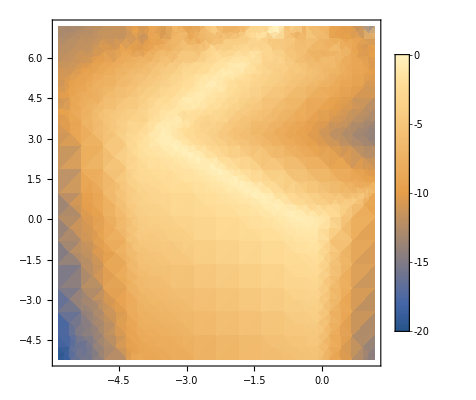

```mathematica
DensityPlot[ϵetesttemp["ϵf"][u,z],{z,Log10[ϵetesttemp["zrange"][[1]]],Log10[ϵetesttemp["zrange"][[2]]]},{u,Log10[ϵetesttemp["urange"][[1]]],Log10[ϵetesttemp["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ϵetest2=Interpolateϵeuztest[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,120,40,10^-3];
```

```mathematica
ϵetest2
```

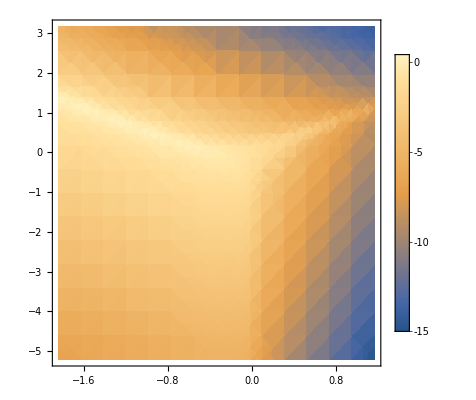

```mathematica
DensityPlot[ϵetest2["ϵf"][u,z],{z,Log10[ϵetest2["zrange"][[1]]],Log10[ϵetest2["zrange"][[2]]]},{u,Log10[ϵetest2["urange"][[1]]],Log10[ϵetest2["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ϵetest4=Interpolateϵeuztest[10 "m"/.SIConstRepl,FeTotalparams[[2]],False,120,40,10^-7];
```

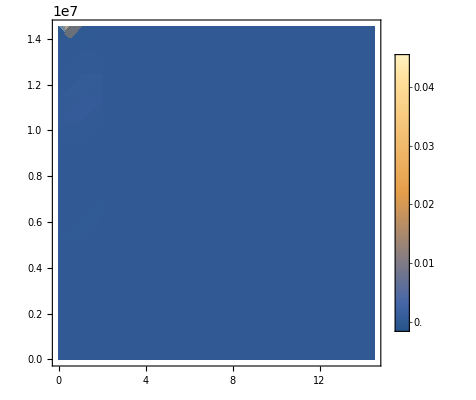

```mathematica
DensityPlot[ϵetest4["ϵf"][u,z],{z,ϵetest4["zrange"][[1]],ϵetest4["zrange"][[2]]},{u,ϵetest4["urange"][[1]],ϵetest4["urange"][[2]]},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Print["So we run into, what I hope, are numerical instabilities at low momentum transfers which cause Im[-1/ϵ] to become negative. at q ranging over 3 orders of magnitude, we seem to be safe from the instabilities. "]
Print["Wait, I remember something about Lindhard becoming negative in the Pines textbook. That might be worth a lookup."]
```

So we run into, what I hope, are numerical instabilities at low momentum transfers.

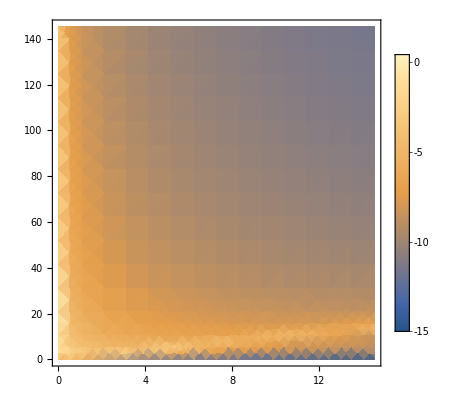

That my friends, is a plasmon line to the left and an onshell line to the right!

```mathematica
DensityPlot[ϵetest["ϵf"][Log10[u],Log10[z]],{z,ϵetest["zrange"][[1]] ,ϵetest["zrange"][[2]]},{u,ϵetest["urange"][[1]] ,(ϵetest["urange"][[2]])/10},PlotRange->All,PlotLegends->Automatic]
Print["That my friends, is a plasmon line to the left and an onshell line to the right!"]
```

```mathematica
DensityPlot[ϵetest["ϵf"][u,z],{z,Log10[ϵetest["zrange"][[1]]],Log10[ϵetest["zrange"][[2]]]},{u,Log10[ϵetest["urange"][[1]]],Log10[ϵetest["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
Print["On the log log plot we can see it even more clearly, for this range of masses, we have a sharp plasmon line branching off from the kinematic line moving off towards q=0, and a kinematic line along u=z "]
```

-Graphics-

On the log log plot we can see it even more clearly, for this range of masses, we have a sharp plasmon line branching off from the kinematic line moving off towards q=0, and a kinematic line along u=z

```mathematica
NMaximize[ϵetest["ϵf"][Log10[u],Log10[z]],{u,z}∈Rectangle[{ϵetest["urange"][[1]],ϵetest["zrange"][[1]]},{ϵetest["urange"][[2]],ϵetest["zrange"][[2]]}]]

{Log10[u],Log10[z]}/.%[[2]]
Print["So the 2D maximization works on our interpolation! This means we will be able to normalize our joint probability distribution for use in the Monte-Carlo. Next we have to include the proportionality factors between this and dσ/dE_R"]
```

{0.448415,{u→19.5772,z→0.016366}}

{1.29175,-1.78606}

So the 2D maximization works on our interpolation! This means we will be able to normalize our joint probability distribution for use in the Monte-Carlo. Next we have to include the proportionality factors between this and dσ/dE_R

```mathematica
1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]
%/.vχ->10^-3"c"/.ϵetest["params"]/.κ->1/.ω->cosθ^2 ω
mχ/(2 "ℏ")(10^-3"c")^2/.mχ->ϵetest["mχ"]/.ϵetest["params"]
NMaximize[%%,{ω,cosθ}∈Rectangle[{ϵetest["ωrange"][[1]],0},{%,1}]]
```

(8.73769×10^8 κ InterpolatingFunction[…][Log[(5.60763×10^-12 ω)/(vχ (cosθ+√(cosθ^2-(0.0000231614 ω)/vχ^2)))]/Log[10],Log[2.42111×10^-6 vχ (cosθ+√(cosθ^2-(0.0000231614 ω)/vχ^2))]/Log[10]])/((1-ⅇ^(-2.63427×10^-14 ω)) vχ^2 √(cosθ^2-(0.0000231614 ω)/vχ^2))

(0.00970855 InterpolatingFunction[…][Log[(1.86921×10^-17 cosθ^2 ω)/(cosθ+√(cosθ^2-2.57348×10^-16 cosθ^2 ω))]/Log[10],Log[0.726334 (cosθ+√(cosθ^2-2.57348×10^-16 cosθ^2 ω))]/Log[10]])/((1-ⅇ^(-2.63427×10^-14 cosθ^2 ω)) √(cosθ^2-2.57348×10^-16 cosθ^2 ω))

3.88578×10^15

InterpolatingFunction::dmval: Input value {-1.82346,15.5535} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.85194,15.5053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.47944,15.7412} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {6.5887×10^12-ω≤0,-1+cosθ≤0}.

{3.07311×10^-13,{ω→0.876688,cosθ→8.07915×10^13}}

```mathematica
DensityPlot[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1/.ω->cosθ^2 ω,{ω,6.588699526066351*^12,3.8857819905213265*^15},{cosθ,0,1}]
```

-Graphics-

```mathematica
DensityPlot[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))10^ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1/.ω->cosθ^2 ω,{ω,6.588699526066351*^12,3.8857819905213265*^15},{cosθ,10^-1,1}]
```

-Graphics-

```mathematica
Print["Why is there whitespace in this plot? Check what happens in that region by evaluating at that point"]
1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1/.ω->cosθ^2 ω/.{ω->3.2 10^15,cosθ->0.3}
```

Why is there whitespace in this plot? Check what happens in that region by evaluating at that point

0.0770725

```mathematica
DensityPlot[Log10[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1/.ω->cosθ^2 ωp],{ωp,6.588699526066351*^12,3.8857819905213265*^15},{cosθ,10^-1,1},PlotRange->All,PlotLegends->Automatic]
Print["So we get some numerical hair at the boundary of ω. We can remedy this by bringing in the interpolation boundary by a small amound. It is likely because ξ_± ->0 there."]
```

-Graphics-

```mathematica
DensityPlot[Log10[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1/.ω->cosθ^2 ωp],{ωp,6.588699526066351*^12,1/2 13.8857819905213265*^15},{cosθ,10^-1,1},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

I think we should change from ω to ξ_ω, a dimensionless variable.

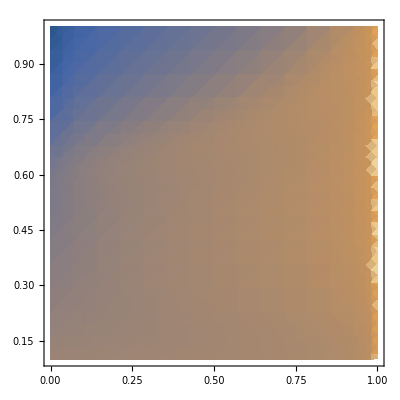

```mathematica
Print["I think we should change from ω to ξ_ω, a dimensionless variable."]
DensityPlot[Log10[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))10^ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.ω->ϵetest["ωrange"][[1]]+(cosθ^2 (mχ vχ^2)/(2 "ℏ")-ϵetest["ωrange"][[1]])ξω/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1],{ξω,0,1},{cosθ,10^-1,1},PlotRange->All]
```

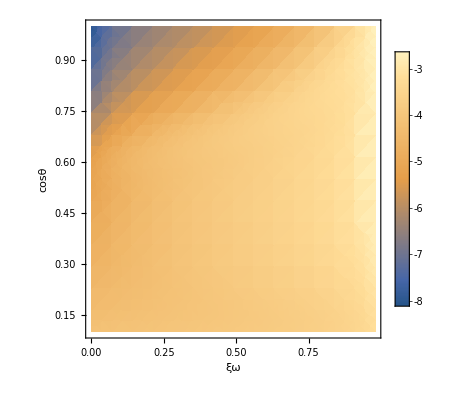

```mathematica
DensityPlot[Log10[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/(√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)))(κ ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))10^ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.ω->ϵetest["ωrange"][[1]]+(cosθ^2 (mχ vχ^2)/(2 "ℏ")-ϵetest["ωrange"][[1]])ξω/.mχ->ϵetest["mχ"]/.ϵetest["params"]/.vχ->(10^-3"c"/.ϵetest["params"])/.κ->1],{ξω,0,0.98},{cosθ,10^-1,1},PlotRange->All,PlotLegends->Automatic,AxesLabel->Automatic]
```

```mathematica
Rectangle[{ϵetest["ωrange"][[1]],-1},{(mχ/(2 "ℏ")(10^-3"c")^2/.mχ->ϵetest["mχ"]/.ϵetest["params"]),1}]
DensityPlot[Log[0.726333799083625 (cosθ+√(cosθ^2-2.5734845712891817*^-16 cosθ^2 ω))]/Log[10],{ω,6.588699526066351*^12,3.8857819905213265*^15},{cosθ,0,1},PlotLegends->Automatic]
DensityPlot[Log[(1.8692088255475654*^-17 cosθ^2 ω)/(cosθ+√(cosθ^2-2.5734845712891817*^-16 cosθ^2 ω))]/Log[10],{ω,6.588699526066351*^12,3.8857819905213265*^15},{cosθ,0,1},PlotLegends->Automatic]
```

Rectangle[{6.5887×10^12,-1},{3.88578×10^15,1}]

-Graphics-

-Graphics-

```mathematica
ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.ωqp->vχ cosθ - (q"ℏ")/mχ/.q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))/.mχ->ϵetest["mχ"]/.ϵetest["params"]
%/.vχ->10^-3"c"/.ϵetest["params"]/.κ->1/.ω->cosθ^2 ω
mχ/(2 "ℏ")(10^-3"c")^2/.mχ->ϵetest["mχ"]/.ϵetest["params"]
DensityPlot[%%,{ω,6.588699526066351*^12,3.8857819905213265*^15},{cosθ, 10^-1,1},PlotLegends->Automatic]
```

InterpolatingFunction[…][Log[(5.60763×10^-12 ω)/(vχ (cosθ+√(cosθ^2-(0.0000231614 ω)/vχ^2)))]/Log[10],Log[2.42111×10^-6 vχ (cosθ+√(cosθ^2-(0.0000231614 ω)/vχ^2))]/Log[10]]

InterpolatingFunction[…][Log[(1.86921×10^-17 cosθ^2 ω)/(cosθ+√(cosθ^2-2.57348×10^-16 cosθ^2 ω))]/Log[10],Log[0.726334 (cosθ+√(cosθ^2-2.57348×10^-16 cosθ^2 ω))]/Log[10]]

3.88578×10^15

-Graphics-

```mathematica
Print["See if we can determine what is special about the point ω/ω_R=cos^2θ."]
Solve[cosθ^2 mχ vχ^2/(2 ℏ) ==cosθ q vχ - (ℏ  q^2)/(2 mχ)/.q->(mχ vχ)/ℏ(cosθ+√(cosθ^2-(2ω  ℏ)/(mχ vχ^2))),cosθ]//Simplify//PowerExpand//Simplify
Print["This gives no additional information. "]
Solve[cosθ^2 mχ vχ^2/(2 ℏ) ==cosθ q vχ - (ℏ  q^2)/(2 mχ),q]//Simplify//PowerExpand//Simplify
Print["Right, by definition this is the point where q has a repeated root in the equation ω = q vχ cosθ - q^2 ℏ/(2 mχ)."]
ω-cosθ q vχ + (ℏ  q^2)/(2 mχ)/.%%%%[[2]]//FullSimplify
(√ω-√((ℏ  q^2)/(2 mχ)))^2//Expand//PowerExpand

(*ω==cosθ q vχ - (ℏ  q^2)/(2 mχ)/.%%%%[[2]]/.ω->ω^2//PowerExpand//Simplify
Solve[%,ω]/.ω->√ω
(√ω/.%//PowerExpand)^2*)
Print["So this is the point where ω is q^2ℏ/(2 mχ). This implies"]
Solve[(ℏ  q^2)/(2 mχ) == cosθ q vχ - (ℏ  q^2)/(2 mχ),q]
Print["we get the same condition again. So what is the physical significance of this solution?"]
```

See if we can determine what is special about the point ω/ω_R=cos^2θ.

{{cosθ→-(√2 √ω √ℏ)/(√mχ vχ)},{cosθ→(√2 √ω √ℏ)/(√mχ vχ)}}

This gives no additional information.

{{q→(cosθ mχ vχ)/ℏ},{q→(cosθ mχ vχ)/ℏ}}

Right, by definition this is the point where q has a repeated root in the equation ω = q vχ cosθ - q^2 ℏ/(2 mχ).

ω-(√2 q √ω √ℏ)/(√mχ)+(q^2 ℏ)/(2 mχ)

ω-(√2 q √ω √ℏ)/(√mχ)+(q^2 ℏ)/(2 mχ)

So this is the point where ω is q^2ℏ/(2 mχ). This implies

{{q→0},{q→(cosθ mχ vχ)/ℏ}}

we get the same condition again. So what is the physical significance of this solution?

#### Interpolate ϵ(q,ω) and dσ/(dE_R dΩ)

```mathematica
Clear[Interpolateϵeuztest]
Interpolateϵeuztest[mχ_,params_,uselog_:True,m_:40,n_:40,ϵ_:10^-4]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,umin,umax,zmin,zmax,InterPu,InterPz,InterϵTable,Interϵf},
(*Interpolate over ϵ for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*Find the q,ω range over which we are interpolating*)
vχmax=2 10^-2"c"/.params; (*nonrelativistic limit*)
ωmin= "ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=ϵ qmax;

(*Now convert to u and z variables*)
umin = ωmin/(qmax"vF")/.params;
umax = ωmax/(qmin "vF")/.params;
zmin = qmin/(2 "qF")/.params;
zmax = qmax/(2 "qF")/.params;

(*Log Subdivide the intervals*)
     InterPu= If[uselog,10^Subdivide[Log10[umin],Log10[umax],m],Subdivide[umin,umax,m]];
InterPz= If[uselog,10^Subdivide[Log10[zmin],Log10[zmax],n],Subdivide[zmin,zmax,n]];

InterϵTable=Table[{{InterPu[[i]],InterPz[[j]]},Abs[Im[-1/ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]])]]/.params]},{i,m+1},{j,n+1}];
Interϵf=If[uselog,Interpolation[Flatten[Log10[InterϵTable],1],InterpolationOrder->4],Interpolation[Flatten[InterϵTable,1],InterpolationOrder->4]];

<|"ϵf"->Interϵf,"ϵTable"->InterϵTable,"mχ"->mχ,"us"->InterPu,"zs"->InterPz,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax},"urange"->{umin,umax},"zrange"->{zmin,zmax},"params"->params,"Npoints"->{m,n}|>
]
```

```mathematica
Print["Let's leave this alone for now. Build up a pipeline for sampling the distribution and we can use this for a speed up if necessary"]
```

#### Define dσ/(dE_R dΩ) using interpolated ϵ

```mathematica
dσdERdΩeofvχandϵ[ξω_,cosθ_,vχ_,κ_,ϵDict_]:=Module[{mχ,ωmax,ω,qpm,ξθ,dσdERdΩ},
(*   ξω ∈ (0,1) - []
  cosθ ϵ (0,1) - [] negative disallowed since gas is assumed degenerate: hence no energy can be removed from the Fermi sphere.*)
mχ=ϵDict["mχ"];
ωmax = (mχ vχ^2)/(2 "ℏ")/.ϵDict["params"];
ω=cosθ^2 (ϵetest["ωrange"][[1]]+(ωmax-ϵetest["ωrange"][[1]])ξω); (*define ω in terms of ξω*)
qpm={q->(mχ vχ)/("ℏ")(cosθ-√(cosθ^2-(2ω "ℏ")/(mχ vχ^2))),q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))}/.ϵDict["params"];(*solutions for q to ω-ω(q,cosθ)=0 in the delta function that arises in the q integral. These must be summed over*)
ξθ=√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2))/.ϵDict["params"];(*the absolute value of the jacobian of the delta function, evaluated on the solution of q, for each of the above solutions*)
dσdERdΩ = Table[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/ξθ(κ^2 ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))10^ϵetest["ϵf"][Log10[ω/("vF"q)/.FeTotalparams[[2]]],Log10[q/(2"qF")/.FeTotalparams[[2]]]]/.qpm[[i]]/.ϵDict["params"],{i,2}];
<|"dσdERdΩ"->dσdERdΩ,"ϵDict"->ϵDict,"ω"->ω,"ωmax"->ωmax,"cosθ"->cosθ,"ξpm"->ξpm,"qpm"->qpm|>
]
```

```mathematica
dσdERdΩeofvχandϵ[0.7,0.7,10^-3"c",1,ϵetest]
```

```mathematica
Print["why are we getting imaginary numbers here? We have desinged this function to ensure that we do not"]
```

```mathematica
ϵetest["ωrange"]
```

{6.5887×10^12,1.55431×10^18}

```mathematica
Table[Total[dσdERdΩeofvχandϵ[i,j,10^-3"c",1,ϵetest][["dσdERdΩ"]]],{i,0.05,0.95,0.05},{j,0.05,0.95,0.05}]
Length[Flatten@%]
```

InterpolatingFunction::dmval: Input value {-2.14458,-3.02247} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.84355,-2.72144} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.66746,-2.54535} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.000245643,0.000125636,0.0000882321,0.0000690942,0.0000570591,0.0000487555,0.0000428007,0.0000384687,0.000035372,0.0000326915,0.0000324598,0.0000323883,0.0000283433,0.000024996,0.0000243734,0.0000249262,0.000025919,0.0000271161,0.0000284259},{0.000243006,0.000130325,0.0000951912,0.0000780226,0.0000679432,0.0000615849,0.0000575587,0.0000551389,0.0000539338,0.000052808,0.0000544312,0.0000580165,0.0000540708,0.0000482997,0.0000476027,0.0000492764,0.0000517963,0.0000546392,0.0000576273},{0.000248665,0.000136985,0.000103323,0.0000882046,0.0000805075,0.0000767114,0.0000753146,0.0000754919,0.0000767276,0.0000775011,0.0000807003,0.0000885988,0.0000854004,0.000076313,0.0000744705,0.0000768221,0.0000807516,0.0000852677,0.000090053},{0.000256706,0.00014449,0.000112301,0.0000995814,0.0000948187,0.0000942403,0.0000961075,0.0000993764,0.000103302,0.00010609,0.000111006,0.000122606,0.000121419,0.000109055,0.000104955,0.000107617,0.00011302,0.000119426,0.000126297},{0.000266156,0.000152746,0.00012218,0.000112282,0.000111048,0.000114331,0.000120002,0.00012669,0.000133427,0.000138422,0.000144708,0.000159552,0.000162424,0.00014771,0.000139983,0.000142421,0.000149314,0.000157839,0.000167107},{0.000276836,0.000161821,0.000133086,0.000126483,0.000129406,0.00013718,0.000147127,0.000157486,0.000167185,0.00017483,0.000182206,0.000199399,0.000208742,0.000193933,0.000180826,0.000182187,0.000190386,0.0002012,0.000213143},{0.000288806,0.000171843,0.000145186,0.000142401,0.000150153,0.000163049,0.000177724,0.000192041,0.000204953,0.000216006,0.000224235,0.000242321,0.000260598,0.00024971,0.000229129,0.000227998,0.000237032,0.000250172,0.000264978},{0.000302251,0.00018299,0.000158694,0.000160316,0.000173624,0.000192298,0.000212185,0.000230849,0.000247375,0.000262272,0.000271806,0.000288705,0.000318068,0.000312946,0.000287073,0.000281276,0.000290162,0.000305436,0.000323137},{0.000317455,0.000195497,0.000173887,0.000180587,0.000200259,0.000225435,0.000251113,0.000274655,0.000295359,0.000313881,0.000326244,0.000344721,0.000381129,0.000385862,0.000357589,0.000343981,0.000351046,0.000367762,0.000388151},{0.000334823,0.000209683,0.000191136,0.000203693,0.000230654,0.000263171,0.000295372,0.000324507,0.000350134,0.000372911,0.000389308,0.000409567,0.00044981,0.00046926,0.000444577,0.000418987,0.000421402,0.000438149,0.000460656},{0.000354925,0.000225982,0.000210945,0.000230289,0.000265632,0.000306515,0.000346193,0.000381861,0.000413363,0.000441167,0.000463364,0.000484733,0.000524484,0.000563214,0.000549961,0.000510648,0.000503859,0.000518074,0.000541551},{0.000378576,0.000245012,0.000234031,0.000261302,0.000306372,0.000356921,0.000405334,0.000448772,0.0004872,0.000521158,0.000551671,0.000573322,0.000606894,0.000667459,0.000670154,0.000625652,0.000602816,0.000610295,0.000632315},{0.000406993,0.000267689,0.000261446,0.000298096,0.000354618,0.000416554,0.000475393,0.000528242,0.000575076,0.000616513,0.000654272,0.000679978,0.000715591,0.000781888,0.000810225,0.000774014,0.000725917,0.00071935,0.000735585},{0.000442069,0.000295432,0.000294823,0.000342786,0.000413083,0.000488773,0.000560381,0.000624854,0.00068209,0.000732783,0.00077818,0.000811955,0.000847366,0.000907782,0.000970449,0.000954899,0.000886672,0.00085408,0.000856933},{0.000486973,0.000330604,0.000336868,0.000398872,0.000486261,0.000579134,0.00066689,0.000746152,0.0008166,0.00087902,0.00093373,0.000981172,0.00101341,0.00106126,0.001151,0.00117104,0.0011088,0.00103236,0.00100782},{0.000547491,0.000377515,0.000392494,0.000472699,0.000582301,0.000697687,0.00080681,0.0009057,0.00099362,0.001071,0.00113811,0.00119713,0.00123463,0.00127897,0.00135616,0.00143081,0.00140072,0.00129187,0.00121435},{0.000635707,0.000445126,0.000471888,0.000577397,0.000718035,0.000865148,0.00100459,0.00113137,0.00124398,0.00134226,0.00142671,0.00149797,0.00155472,0.00158707,0.00163756,0.0017426,0.00177956,0.00169817,0.00154267},{0.0007829,0.000556568,0.000601242,0.000746646,0.000936575,0.00113446,0.00132265,0.00149422,0.00164625,0.00177768,0.00188876,0.00197942,0.0020527,0.00209363,0.00212336,0.00216982,0.00229095,0.0022964,0.00216076},{0.00111332,0.0008034,0.000883826,0.00111287,0.00140714,0.00171315,0.00200529,0.00227221,0.00250786,0.00270927,0.00287558,0.00300796,0.00310645,0.0031771,0.00319909,0.00319744,0.0032191,0.00333531,0.00336352}}

361

```mathematica
dσdERdΩeofvχandϵ[0.5,0.6579,10^-4"c",1,ϵetest]
```

```mathematica
dσdERdΩeofvχandϵ[0.000005,0.5,10^-4"c",1,ϵetest]
dσdERdΩeofvχandϵ[0.000005,0.0005,10^-4"c",1,ϵetest]
```

InterpolatingFunction::dmval: Input value {-2.15857,-2.49189} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.15857,-5.49189} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.49189,-4.15857} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Print["This tells us that we need to go to much smaller q to be able to account for small angle scattering"]
```

This tells us that we need to go to much smaller q to be able to account for small angle scattering

```mathematica
Print["Try now to redefine by shifting up the by the smallest value"]
```

```mathematica
Clear[Interpolateϵeuztestpositive]
Interpolateϵeuztestpositive[mχ_,params_,uselog_:True,m_:40,n_:40,δ_:10^-5]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,umin,umax,zmin,zmax,InterPu,InterPz,uzTable, InterϵTableneg,minϵ,shift,InterϵTable,Interϵf},
(*Interpolate over ϵ for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*Find the range over which we are interpolating*)
vχmax=2 10^-2"c"/.params; (*nonrelativistic limit*)
ωmin= "ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=δ qmax;(*δ = Subscript[q, max]/Subscript[q, min] - necessary since the ϵ has a removable singularity at q=0*)

(*Now convert to u and z variables*)
umin = ωmin/(qmax"vF")/.params;
umax = ωmax/(qmin "vF")/.params;
zmin = qmin/(2 "qF")/.params;
zmax = qmax/(2 "qF")/.params;

(*Log Subdivide the intervals*)
     InterPu= If[uselog,10^Subdivide[Log10[umin],Log10[umax],m],Subdivide[umin,umax,m]];
InterPz= If[uselog,10^Subdivide[Log10[zmin],Log10[zmax],n],Subdivide[zmin,zmax,n]];

(*InterϵTableneg=Table[{{InterPu[[i]],InterPz[[j]]},Im[-1/(Dielectrics`ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]])])]/.params},{i,m+1},{j,n+1}];
*)
uzTable=Table[{InterPu[[i]],InterPz[[j]]},{i,m+1},{j,n+1}];
InterϵTableneg=Table[Im[-1/(Dielectrics`ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]])])]/.params,{i,m+1},{j,n+1}];

(*Print[Min[Flatten[InterϵTable,1][[;;,2]]]];*)
minϵ=Min[Flatten[InterϵTableneg,1]];
shift = If[minϵ>0,0,minϵ];

InterϵTable = Table[{uzTable[[i,j]],InterϵTableneg[[i,j]] +Abs[shift]},{i,m+1},{j,n+1}];

Interϵf=If[uselog,Interpolation[Flatten[Log10[InterϵTable],1],InterpolationOrder->4],Interpolation[Flatten[InterϵTable,1],InterpolationOrder->4]];

<|"ϵf"->Interϵf,"ϵTable"->InterϵTable,"mχ"->mχ,"us"->InterPu,"zs"->InterPz,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax},"urange"->{umin,umax},"zrange"->{zmin,zmax},"params"->params,"Npoints"->{m,n},"δ"->δ|>
]
```

```mathematica
ϵetest3=Interpolateϵeuztestpositive[ 10"m"/.SIConstRepl,FeTotalparams[[2]],True,20,20,10^-7];
```

```mathematica
Print["WTF? all of a sudden it's positive? What is the plot?"]
```

```mathematica
ϵetest3[["ϵTable"]];
Print["This the minimum value is far too large. I think we need to truncate ω where it turns negative and take the absolute value. "]
```

{{{{6.15783×10^-6,1.45267×10^-6},0.218543},{{6.15783×10^-6,3.25212×10^-6},0.218543},{{6.15783×10^-6,7.28058×10^-6},0.218543},{{6.15783×10^-6,0.0000162992},0.218543},{{6.15783×10^-6,0.0000364894},0.218543},{{6.15783×10^-6,0.0000816895},0.218543},{{6.15783×10^-6,0.00018288},0.218543},{{6.15783×10^-6,0.000409417},0.218543},{{6.15783×10^-6,0.000916571},0.218543},{{6.15783×10^-6,0.00205195},0.218543},{{6.15783×10^-6,0.00459374},0.218543},{{6.15783×10^-6,0.0102841},0.218543},{{6.15783×10^-6,0.0230232},0.218543},{{6.15783×10^-6,0.0515426},0.218543},{{6.15783×10^-6,0.115389},0.218544},{{6.15783×10^-6,0.258325},0.218545},{{6.15783×10^-6,0.578317},0.218546},{{6.15783×10^-6,1.29469},0.218543},{{6.15783×10^-6,2.89845},0.218543},{{6.15783×10^-6,6.48883},0.218543},{{6.15783×10^-6,14.5267},0.218543}},{{{0.0000255897,1.45267×10^-6},0.218543},{{0.0000255897,3.25212×10^-6},0.218543},{{0.0000255897,7.28058×10^-6},0.218543},{{0.0000255897,0.0000162992},0.218543},{{0.0000255897,0.0000364894},0.218543},{{0.0000255897,0.0000816895},0.218543},{{0.0000255897,0.00018288},0.218543},{{0.0000255897,0.000409417},0.218543},{{0.0000255897,0.000916571},0.218543},{{0.0000255897,0.00205195},0.218543},{{0.0000255897,0.00459374},0.218543},{{0.0000255897,0.0102841},0.218543},{{0.0000255897,0.0230232},0.218543},{{0.0000255897,0.0515426},0.218544},{{0.0000255897,0.115389},0.218546},{{0.0000255897,0.258325},0.218552},{{0.0000255897,0.578317},0.218557},{{0.0000255897,1.29469},0.218543},{{0.0000255897,2.89845},0.218543},{{0.0000255897,6.48883},0.218543},{{0.0000255897,14.5267},0.218543}},{{{0.000106341,1.45267×10^-6},0.218543},{{0.000106341,3.25212×10^-6},0.218543},{{0.000106341,7.28058×10^-6},0.218543},{{0.000106341,0.0000162992},0.218543},{{0.000106341,0.0000364894},0.218543},{{0.000106341,0.0000816895},0.218543},{{0.000106341,0.00018288},0.218543},{{0.000106341,0.000409417},0.218543},{{0.000106341,0.000916571},0.218543},{{0.000106341,0.00205195},0.218543},{{0.000106341,0.00459374},0.218543},{{0.000106341,0.0102841},0.218544},{{0.000106341,0.0230232},0.218545},{{0.000106341,0.0515426},0.218549},{{0.000106341,0.115389},0.218558},{{0.000106341,0.258325},0.21858},{{0.000106341,0.578317},0.2186},{{0.000106341,1.29469},0.218543},{{0.000106341,2.89845},0.218543},{{0.000106341,6.48883},0.218543},{{0.000106341,14.5267},0.218543}},{{{0.000441915,1.45267×10^-6},0.218543},{{0.000441915,3.25212×10^-6},0.218543},{{0.000441915,7.28058×10^-6},0.218543},{{0.000441915,0.0000162992},0.218543},{{0.000441915,0.0000364894},0.218543},{{0.000441915,0.0000816895},0.218543},{{0.000441915,0.00018288},0.218543},{{0.000441915,0.000409417},0.218543},{{0.000441915,0.000916571},0.218543},{{0.000441915,0.00205195},0.218544},{{0.000441915,0.00459374},0.218545},{{0.000441915,0.0102841},0.218548},{{0.000441915,0.0230232},0.218554},{{0.000441915,0.0515426},0.218568},{{0.000441915,0.115389},0.218605},{{0.000441915,0.258325},0.218695},{{0.000441915,0.578317},0.21878},{{0.000441915,1.29469},0.218545},{{0.000441915,2.89845},0.218543},{{0.000441915,6.48883},0.218543},{{0.000441915,14.5267},0.218543}},{{{0.00183643,1.45267×10^-6},0.218543},{{0.00183643,3.25212×10^-6},0.218543},{{0.00183643,7.28058×10^-6},0.218543},{{0.00183643,0.0000162992},0.218543},{{0.00183643,0.0000364894},0.218543},{{0.00183643,0.0000816895},0.218543},{{0.00183643,0.00018288},0.218543},{{0.00183643,0.000409417},0.218544},{{0.00183643,0.000916571},0.218545},{{0.00183643,0.00205195},0.218547},{{0.00183643,0.00459374},0.218552},{{0.00183643,0.0102841},0.218563},{{0.00183643,0.0230232},0.218589},{{0.00183643,0.0515426},0.218649},{{0.00183643,0.115389},0.218799},{{0.00183643,0.258325},0.219177},{{0.00183643,0.578317},0.219527},{{0.00183643,1.29469},0.218554},{{0.00183643,2.89845},0.218543},{{0.00183643,6.48883},0.218543},{{0.00183643,14.5267},0.218543}},{{{0.00763154,1.45267×10^-6},0.218543},{{0.00763154,3.25212×10^-6},0.218543},{{0.00763154,7.28058×10^-6},0.218543},{{0.00763154,0.0000162992},0.218543},{{0.00763154,0.0000364894},0.218543},{{0.00763154,0.0000816895},0.218543},{{0.00763154,0.00018288},0.218544},{{0.00763154,0.000409417},0.218546},{{0.00763154,0.000916571},0.21855},{{0.00763154,0.00205195},0.21856},{{0.00763154,0.00459374},0.218581},{{0.00763154,0.0102841},0.218628},{{0.00763154,0.0230232},0.218735},{{0.00763154,0.0515426},0.218983},{{0.00763154,0.115389},0.21961},{{0.00763154,0.258325},0.221177},{{0.00763154,0.578317},0.222633},{{0.00763154,1.29469},0.218588},{{0.00763154,2.89845},0.218543},{{0.00763154,6.48883},0.218543},{{0.00763154,14.5267},0.218543}},{{{0.0317139,1.45267×10^-6},0.218543},{{0.0317139,3.25212×10^-6},0.218543},{{0.0317139,7.28058×10^-6},0.218543},{{0.0317139,0.0000162992},0.218543},{{0.0317139,0.0000364894},0.218543},{{0.0317139,0.0000816895},0.218545},{{0.0317139,0.00018288},0.218549},{{0.0317139,0.000409417},0.218557},{{0.0317139,0.000916571},0.218574},{{0.0317139,0.00205195},0.218613},{{0.0317139,0.00459374},0.218701},{{0.0317139,0.0102841},0.218897},{{0.0317139,0.0230232},0.219341},{{0.0317139,0.0515426},0.220371},{{0.0317139,0.115389},0.222976},{{0.0317139,0.258325},0.229492},{{0.0317139,0.578317},0.23555},{{0.0317139,1.29469},0.21873},{{0.0317139,2.89845},0.218543},{{0.0317139,6.48883},0.218543},{{0.0317139,14.5267},0.218543}},{{{0.131791,1.45267×10^-6},0.218543},{{0.131791,3.25212×10^-6},0.218543},{{0.131791,7.28058×10^-6},0.218543},{{0.131791,0.0000162992},0.218543},{{0.131791,0.0000364894},0.218543},{{0.131791,0.0000816895},0.218565},{{0.131791,0.00018288},0.218569},{{0.131791,0.000409417},0.218601},{{0.131791,0.000916571},0.218674},{{0.131791,0.00205195},0.218837},{{0.131791,0.00459374},0.2192},{{0.131791,0.0102841},0.220017},{{0.131791,0.0230232},0.221859},{{0.131791,0.0515426},0.226143},{{0.131791,0.115389},0.236999},{{0.131791,0.258325},0.264293},{{0.131791,0.578317},0.289806},{{0.131791,1.29469},0.219424},{{0.131791,2.89845},0.218544},{{0.131791,6.48883},0.218543},{{0.131791,14.5267},0.218543}},{{{0.547675,1.45267×10^-6},0.218543},{{0.547675,3.25212×10^-6},0.218543},{{0.547675,7.28058×10^-6},0.218543},{{0.547675,0.0000162992},0.218543},{{0.547675,0.0000364894},0.218543},{{0.547675,0.0000816895},0.218472},{{0.547675,0.00018288},0.218652},{{0.547675,0.000409417},0.218787},{{0.547675,0.000916571},0.219088},{{0.547675,0.00205195},0.219763},{{0.547675,0.00459374},0.221276},{{0.547675,0.0102841},0.224671},{{0.547675,0.0230232},0.232357},{{0.547675,0.0515426},0.250445},{{0.547675,0.115389},0.297817},{{0.547675,0.258325},0.430316},{{0.547675,0.578317},0.534158},{{0.547675,1.29469},0.240264},{{0.547675,2.89845},0.218548},{{0.547675,6.48883},0.218543},{{0.547675,14.5267},0.218543}},{{{2.27594,1.45267×10^-6},0.218543},{{2.27594,3.25212×10^-6},0.218543},{{2.27594,7.28058×10^-6},0.218543},{{2.27594,0.0000162992},0.218543},{{2.27594,0.0000364894},0.218544},{{2.27594,0.0000816895},0.218831},{{2.27594,0.00018288},0.219008},{{2.27594,0.000409417},0.219555},{{2.27594,0.000916571},0.220809},{{2.27594,0.00205195},0.223617},{{2.27594,0.00459374},0.229921},{{2.27594,0.0102841},0.244225},{{2.27594,0.0230232},0.278388},{{2.27594,0.0515426},0.380518},{{2.27594,0.115389},1.23075},{{2.27594,0.258325},0.428428},{{2.27594,0.578317},0.231091},{{2.27594,1.29469},0.225745},{{2.27594,2.89845},0.221703},{{2.27594,6.48883},0.218543},{{2.27594,14.5267},0.218543}},{{{9.45795,1.45267×10^-6},0.218543},{{9.45795,3.25212×10^-6},0.218543},{{9.45795,7.28058×10^-6},0.218543},{{9.45795,0.0000162992},0.218543},{{9.45795,0.0000364894},0.218531},{{9.45795,0.0000816895},0.218704},{{9.45795,0.00018288},0.220388},{{9.45795,0.000409417},0.222747},{{9.45795,0.000916571},0.227969},{{9.45795,0.00205195},0.239753},{{9.45795,0.00459374},0.26725},{{9.45795,0.0102841},0.342843},{{9.45795,0.0230232},0.820399},{{9.45795,0.0515426},0.575259},{{9.45795,0.115389},0.231475},{{9.45795,0.258325},0.219538},{{9.45795,0.578317},0.21863},{{9.45795,1.29469},0.218551},{{9.45795,2.89845},0.218544},{{9.45795,6.48883},0.218543},{{9.45795,14.5267},0.218543}},{{{39.3037,1.45267×10^-6},0.218543},{{39.3037,3.25212×10^-6},0.218543},{{39.3037,7.28058×10^-6},0.218543},{{39.3037,0.0000162992},0.218545},{{39.3037,0.0000364894},0.218605},{{39.3037,0.0000816895},0.219597},{{39.3037,0.00018288},0.226548},{{39.3037,0.000409417},0.236093},{{39.3037,0.000916571},0.258523},{{39.3037,0.00205195},0.316366},{{39.3037,0.00459374},0.579668},{{39.3037,0.0102841},1.32514},{{39.3037,0.0230232},0.242905},{{39.3037,0.0515426},0.220286},{{39.3037,0.115389},0.218692},{{39.3037,0.258325},0.218556},{{39.3037,0.578317},0.218544},{{39.3037,1.29469},0.218543},{{39.3037,2.89845},0.218543},{{39.3037,6.48883},0.218543},{{39.3037,14.5267},0.218543}},{{{163.332,1.45267×10^-6},0.218543},{{163.332,3.25212×10^-6},0.218543},{{163.332,7.28058×10^-6},0.218543},{{163.332,0.0000162992},0.218541},{{163.332,0.0000364894},0.218802},{{163.332,0.0000816895},0.222869},{{163.332,0.00018288},0.251754},{{163.332,0.000409417},0.296927},{{163.332,0.000916571},0.46204},{{163.332,0.00205195},2.96576},{{163.332,0.00459374},0.267356},{{163.332,0.0102841},0.221672},{{163.332,0.0230232},0.218805},{{163.332,0.0515426},0.218566},{{163.332,0.115389},0.218545},{{163.332,0.258325},0.218543},{{163.332,0.578317},0.218543},{{163.332,1.29469},0.218543},{{163.332,2.89845},0.218543},{{163.332,6.48883},0.218543},{{163.332,14.5267},0.218543}},{{{678.747,1.45267×10^-6},0.218543},{{678.747,3.25212×10^-6},0.218543},{{678.747,7.28058×10^-6},0.218543},{{678.747,0.0000162992},0.218548},{{678.747,0.0000364894},0.21872},{{678.747,0.0000816895},0.222063},{{678.747,0.00018288},0.363064},{{678.747,0.000409417},1.74086},{{678.747,0.000916571},0.33445},{{678.747,0.00205195},0.223955},{{678.747,0.00459374},0.219024},{{678.747,0.0102841},0.218585},{{678.747,0.0230232},0.218546},{{678.747,0.0515426},0.218543},{{678.747,0.115389},0.218543},{{678.747,0.258325},0.218543},{{678.747,0.578317},0.218543},{{678.747,1.29469},0.218543},{{678.747,2.89845},0.218543},{{678.747,6.48883},0.218543},{{678.747,14.5267},0.218543}},{{{2820.62,1.45267×10^-6},0.218543},{{2820.62,3.25212×10^-6},0.218543},{{2820.62,7.28058×10^-6},0.218542},{{2820.62,0.0000162992},0.218542},{{2820.62,0.0000364894},0.218497},{{2820.62,0.0000816895},0.203652},{{2820.62,0.00018288},0.323171},{{2820.62,0.000409417},0.827071},{{2820.62,0.000916571},0.242021},{{2820.62,0.00205195},0.209301},{{2820.62,0.00459374},0.21838},{{2820.62,0.0102841},0.218524},{{2820.62,0.0230232},0.218538},{{2820.62,0.0515426},0.218543},{{2820.62,0.115389},0.218543},{{2820.62,0.258325},0.218543},{{2820.62,0.578317},0.218543},{{2820.62,1.29469},0.218543},{{2820.62,2.89845},0.218543},{{2820.62,6.48883},0.218543},{{2820.62,14.5267},0.218543}},{{{11721.5,1.45267×10^-6},0.218543},{{11721.5,3.25212×10^-6},0.218543},{{11721.5,7.28058×10^-6},0.218543},{{11721.5,0.0000162992},0.21855},{{11721.5,0.0000364894},0.218578},{{11721.5,0.0000816895},0.218449},{{11721.5,0.00018288},0.215708},{{11721.5,0.000409417},0.194582},{{11721.5,0.000916571},0.0772584},{{11721.5,0.00205195},0.1373},{{11721.5,0.00459374},0.211882},{{11721.5,0.0102841},0.219176},{{11721.5,0.0230232},0.2186},{{11721.5,0.0515426},0.218548},{{11721.5,0.115389},0.218542},{{11721.5,0.258325},0.218543},{{11721.5,0.578317},0.218543},{{11721.5,1.29469},0.218543},{{11721.5,2.89845},0.218543},{{11721.5,6.48883},0.218543},{{11721.5,14.5267},0.218543}},{{{48710.,1.45267×10^-6},0.218543},{{48710.,3.25212×10^-6},0.218543},{{48710.,7.28058×10^-6},0.218543},{{48710.,0.0000162992},0.218543},{{48710.,0.0000364894},0.218536},{{48710.,0.0000816895},0.218985},{{48710.,0.00018288},0.218683},{{48710.,0.000409417},0.23234},{{48710.,0.000916571},0.180854},{{48710.,0.00205195},0.567907},{{48710.,0.00459374},0.246443},{{48710.,0.0102841},0.220422},{{48710.,0.0230232},0.218707},{{48710.,0.0515426},0.218557},{{48710.,0.115389},0.218559},{{48710.,0.258325},0.218543},{{48710.,0.578317},0.218543},{{48710.,1.29469},0.218543},{{48710.,2.89845},0.218543},{{48710.,6.48883},0.218543},{{48710.,14.5267},0.218543}},{{{202421.,1.45267×10^-6},0.218543},{{202421.,3.25212×10^-6},0.218543},{{202421.,7.28058×10^-6},0.218543},{{202421.,0.0000162992},0.218543},{{202421.,0.0000364894},0.218543},{{202421.,0.0000816895},0.218544},{{202421.,0.00018288},0.218562},{{202421.,0.000409417},0.218365},{{202421.,0.000916571},0.214278},{{202421.,0.00205195},0.17436},{{202421.,0.00459374},0.},{{202421.,0.0102841},0.0560125},{{202421.,0.0230232},0.235133},{{202421.,0.0515426},0.217229},{{202421.,0.115389},0.218675},{{202421.,0.258325},0.218555},{{202421.,0.578317},0.218542},{{202421.,1.29469},0.218543},{{202421.,2.89845},0.218543},{{202421.,6.48883},0.218543},{{202421.,14.5267},0.218543}},{{{841187.,1.45267×10^-6},0.218543},{{841187.,3.25212×10^-6},0.218543},{{841187.,7.28058×10^-6},0.218543},{{841187.,0.0000162992},0.218543},{{841187.,0.0000364894},0.218543},{{841187.,0.0000816895},0.218543},{{841187.,0.00018288},0.218543},{{841187.,0.000409417},0.218543},{{841187.,0.000916571},0.218647},{{841187.,0.00205195},0.218685},{{841187.,0.00459374},0.233002},{{841187.,0.0102841},0.0572312},{{841187.,0.0230232},0.535705},{{841187.,0.0515426},0.218908},{{841187.,0.115389},0.218575},{{841187.,0.258325},0.218546},{{841187.,0.578317},0.218509},{{841187.,1.29469},0.218543},{{841187.,2.89845},0.218543},{{841187.,6.48883},0.218543},{{841187.,14.5267},0.218543}},{{{3.49566×10^6,1.45267×10^-6},0.218543},{{3.49566×10^6,3.25212×10^-6},0.218543},{{3.49566×10^6,7.28058×10^-6},0.218543},{{3.49566×10^6,0.0000162992},0.218543},{{3.49566×10^6,0.0000364894},0.218543},{{3.49566×10^6,0.0000816895},0.218543},{{3.49566×10^6,0.00018288},0.218543},{{3.49566×10^6,0.000409417},0.218543},{{3.49566×10^6,0.000916571},0.218543},{{3.49566×10^6,0.00205195},0.218555},{{3.49566×10^6,0.00459374},0.218544},{{3.49566×10^6,0.0102841},0.218551},{{3.49566×10^6,0.0230232},0.218946},{{3.49566×10^6,0.0515426},0.218585},{{3.49566×10^6,0.115389},0.21855},{{3.49566×10^6,0.258325},0.218543},{{3.49566×10^6,0.578317},0.218543},{{3.49566×10^6,1.29469},0.218596},{{3.49566×10^6,2.89845},0.218543},{{3.49566×10^6,6.48883},0.218543},{{3.49566×10^6,14.5267},0.218543}},{{{1.45267×10^7,1.45267×10^-6},0.218543},{{1.45267×10^7,3.25212×10^-6},0.218543},{{1.45267×10^7,7.28058×10^-6},0.218543},{{1.45267×10^7,0.0000162992},0.218543},{{1.45267×10^7,0.0000364894},0.218543},{{1.45267×10^7,0.0000816895},0.218543},{{1.45267×10^7,0.00018288},0.218543},{{1.45267×10^7,0.000409417},0.218543},{{1.45267×10^7,0.000916571},0.218543},{{1.45267×10^7,0.00205195},0.218543},{{1.45267×10^7,0.00459374},0.218494},{{1.45267×10^7,0.0102841},0.218543},{{1.45267×10^7,0.0230232},0.218543},{{1.45267×10^7,0.0515426},0.218546},{{1.45267×10^7,0.115389},0.875973},{{1.45267×10^7,0.258325},0.333084},{{1.45267×10^7,0.578317},0.218543},{{1.45267×10^7,1.29469},0.218543},{{1.45267×10^7,2.89845},0.218543},{{1.45267×10^7,6.48883},0.218543},{{1.45267×10^7,14.5267},0.218543}}}

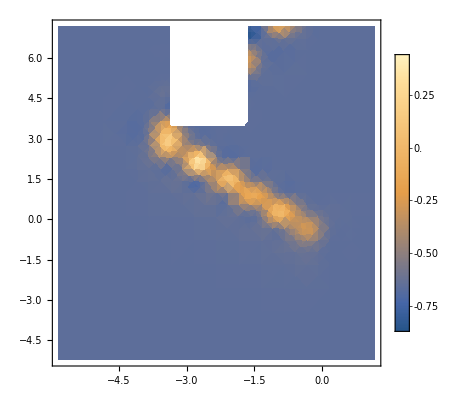

```mathematica
DensityPlot[ϵetest3["ϵf"][u,z],{z,Log10[ϵetest3["zrange"][[1]]],Log10[ϵetest3["zrange"][[2]]]},{u,Log10[ϵetest3["urange"][[1]]],Log10[ϵetest3["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
```

#### Truncate u

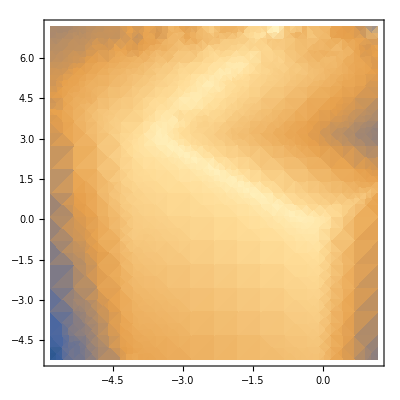

```mathematica
Print["smallest value when we remove the runcation is too large, it washes out all info about the dielectric. So instead we need to truncate u where ϵ becomes negative. We can do this by setting u < 10^3 above"]
```

```mathematica
Clear[Interpolateϵeuztest]
Interpolateϵeuztesttrunced[mχ_,params_,uselog_:True,m_:40,n_:40,δ_:10^-5]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,umin,umax,zmin,zmax,InterPu,InterPz,InterϵTable,Interϵf},
(*Interpolate over ϵ for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*Find the range over which we are interpolating*)
vχmax=2 10^-2"c"/.params; (*nonrelativistic limit*)
ωmin= δ"ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=δ qmax;(*δ = Subscript[q, max]/Subscript[q, min] - necessary since the ϵ has a removable singularity at q=0*)

(*Now convert to u and z variables*)
umin = ωmin/(qmax"vF")/.params;
umax = Min[ωmax/(qmin "vF")/.params,10^3];(*Truncate u at a large value of ω (where we get numerical instabilities)*)
zmin = qmin/(2 "qF")/.params;
zmax = qmax/(2 "qF")/.params;

(*Log Subdivide the intervals*)
     InterPu= If[uselog,10^Subdivide[Log10[umin],Log10[umax],m],Subdivide[umin,umax,m]];
InterPz= If[uselog,10^Subdivide[Log10[zmin],Log10[zmax],n],Subdivide[zmin,zmax,n]];

InterϵTable=Table[{{InterPu[[i]],InterPz[[j]]},Abs[Im[-1/(Dielectrics`ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]])])]/.params]},{i,m+1},{j,n+1}];
Interϵf=If[uselog,Interpolation[Flatten[Log10[InterϵTable],1],InterpolationOrder->4],Interpolation[Flatten[InterϵTable,1],InterpolationOrder->4]];

<|"ϵf"->Interϵf,"ϵTable"->InterϵTable,"mχ"->mχ,"us"->InterPu,"zs"->InterPz,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax},"urange"->{umin,umax},"zrange"->{zmin,zmax},"params"->params,"Npoints"->{m,n},"δ"->δ|>
]
```

```mathematica
ϵetest3=Interpolateϵeuztesttrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
```

```mathematica
ϵetest3[["urange"]]
```

{6.15783×10^-6,1000}

```mathematica
ϵetest3["ϵf"]
```

```mathematica
ϵetest3=Interpolateϵeuztesttrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
```

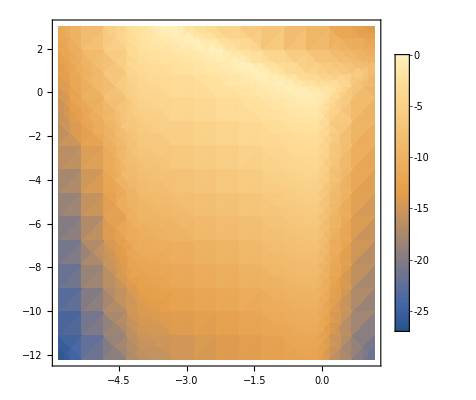

```mathematica
DensityPlot[ϵetest3["ϵf"][u,z],{z,Log10[ϵetest3["zrange"][[1]]],Log10[ϵetest3["zrange"][[2]]]},{u,Log10[ϵetest3["urange"][[1]]],Log10[ϵetest3["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
```

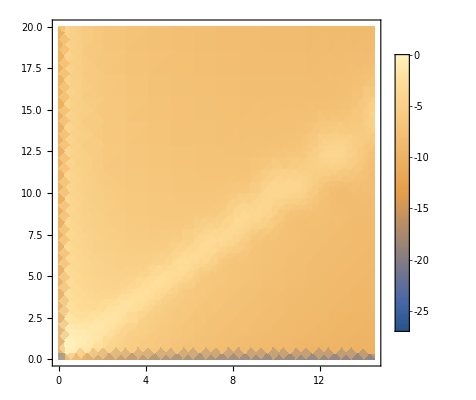

```mathematica
DensityPlot[ϵetest3["ϵf"][Log10[u],Log10[z]],{z,ϵetest3["zrange"][[1]],ϵetest3["zrange"][[2]]},{u,ϵetest3["urange"][[1]],(ϵetest3["urange"][[2]])/50},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Clear[dσdERdΩeofvχandϵ]
```

```mathematica
(*dσdERdΩeofvχandϵ[ξω_,cosθ_,vχ_,κ_,ϵDict_]:=Module[{mχ,ωmax,ω,qpm,ξθ,prefactor,dσdERdΩ,loguzs},
(*   ξω ∈ (0,1) - []
  cosθ ϵ (0,1) - [] negative disallowed since gas is assumed degenerate: hence no energy can be removed from the Fermi sphere.*)
mχ=ϵDict["mχ"];
ωmax =(mχ vχ^2)/(2 "ℏ")/.ϵDict["params"];
ω= cosθ^2(ϵetest["ωrange"][[1]]+(ωmax-ϵetest["ωrange"][[1]])ξω); (*define ω in terms of ξω*)
qpm={q->(mχ vχ)/("ℏ")(cosθ-√(cosθ^2-(2ω "ℏ")/(mχ vχ^2))),q->(mχ vχ)/("ℏ")(cosθ+√(cosθ^2-(2ω "ℏ")/(mχ vχ^2)))}/.ϵDict["params"];(*solutions for q to ω-ω(q,cosθ)=0 in the delta function that arises in the q integral. These must be summed over*)
ξθ=√(cosθ^2-(2 "ℏ" ω)/(mχ vχ^2))/.ϵDict["params"];(*the absolute value of the jacobian of the delta function, evaluated on the solution of q, for each of the above solutions*)
(*dσdERdΩ = Table[1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/ξθ(κ^2 ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω))10^ϵetest["ϵf"][Log10[ω/("vF"q)/.ϵDict["params"]],Log10[q/(2"qF")/.ϵDict["params"]]]/.qpm[[i]]/.ϵDict["params"],{i,2}];*)

loguzs=Table[{Log10[ω/("vF"q)/.ϵDict["params"]],Log10[q/(2"qF")/.ϵDict["params"]]}/.qpm[[i]]/.ϵDict["params"],{i,2}];
prefactor=( 1/(vχ^2 "ne")1/(("ℏ")^2(2 π)^3)1/ξθ(κ^2 ("e")^2)/(4 π "ϵ0")2/(1-E^(-"β" "ℏ" ω)))/.ϵDict["params"];
dσdERdΩ =prefactor Table[10^ϵDict["ϵf"][loguzs[[i,1]],loguzs[[i,2]]],{i,2}];
(*dσdERdΩ =prefactor{10^ϵDict["ϵf"][loguzs[[1,1]],loguzs[[1,2]]],10^ϵDict["ϵf"][loguzs[[2,1]],loguzs[[2,2]] ]};*)
<|"dσdERdΩ"->dσdERdΩ,"ω"->ω,"ωmax"->ωmax,"cosθ"->cosθ,"ξpm"->ξθ,"qpm"->qpm,"loguzs"->loguzs,"prefactor"->prefactor|>
]*)
```

```mathematica
σdict=dσdERdΩeofvχandϵ[0.001,0.001,10^-3"c",1,ϵetest3]
```

InterpolatingFunction::dmval: Input value {-3.83813,-6.00922} lies outside the range of data in the interpolating function. Extrapolation will be used.

<|dσdERdΩ→{1.44194365202018×10^1466,0.00544165},ω→1.04679×10^7,ωmax→3.88578×10^15,cosθ→0.001,ξpm→0.000998652,qpm→{q→34916.5,q→5.17755×10^7},loguzs→{{-3.83813,-6.00922},{-7.00922,-2.83813}},prefactor→3.5255×10^7|>

```mathematica
σdict["prefactor"] 10^ϵetest3["ϵf"][σdict["loguzs"][[1,1]],σdict["loguzs"][[1,2]]]
σdict["prefactor"]10^ϵetest3["ϵf"][σdict["loguzs"][[2,1]],σdict["loguzs"][[2,2]]]
```

1.56867×10^-9

0.00546633

```mathematica
Min[Table[Random[],{i,1000}]]
```

0.00154505

```mathematica
Print["We want larger range of ω and θ, so decrease δ"]
```

```mathematica
ϵetest3=Interpolateϵeuztesttrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-9];
```

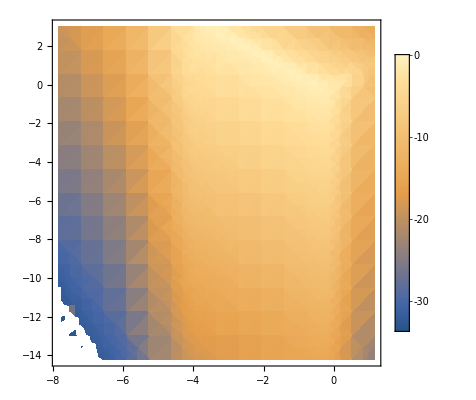

```mathematica
DensityPlot[ϵetest3["ϵf"][u,z],{z,Log10[ϵetest3["zrange"][[1]]],Log10[ϵetest3["zrange"][[2]]]},{u,Log10[ϵetest3["urange"][[1]]],Log10[ϵetest3["urange"][[2]]]},PlotRange->All,PlotLegends->Automatic]
```

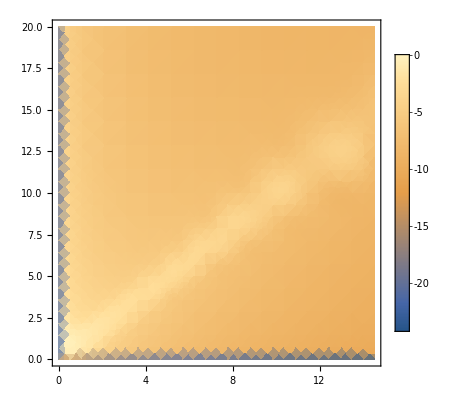

```mathematica
DensityPlot[ϵetest3["ϵf"][Log10[u],Log10[z]],{z,ϵetest3["zrange"][[1]],ϵetest3["zrange"][[2]]},{u,ϵetest3["urange"][[1]],(ϵetest3["urange"][[2]])/50},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
σdict=dσdERdΩeofvχandϵ[0.9,0.9,10^-3"c",1,ϵetest3]
```

<|dσdERdΩ→{0.00151678,0.000652583},ω→2.83327×10^15,ωmax→3.88578×10^15,cosθ→0.9,ξpm→0.284364,qpm→{q→1.59482×10^10,q→3.06812×10^10},loguzs→{{-1.06538,-0.349539},{-1.34954,-0.0653787}},prefactor→0.0341413|>

```mathematica
Min[Table[Random[],{i,10000}]]
```

0.000100586

```mathematica
MaxdσdERdΩ=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,10^-3"c",1,ϵetest3][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵetest3["δ"]^(1/4),ϵetest3["δ"]^(1/4)},{1-ϵetest3["δ"]^(1/4),1-ϵetest3["δ"]^(1/4)}]]
```

{0.0100665,{ξω→0.994377,cosθ→0.773161}}

```mathematica
Table[ξs={Random[],Random[],Random[]};
ξs[[3]]MaxdσdERdΩ[[1]]<= Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],10^-3"c",1,ϵetest3][["dσdERdΩ"]]],{i,100}]
```

{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

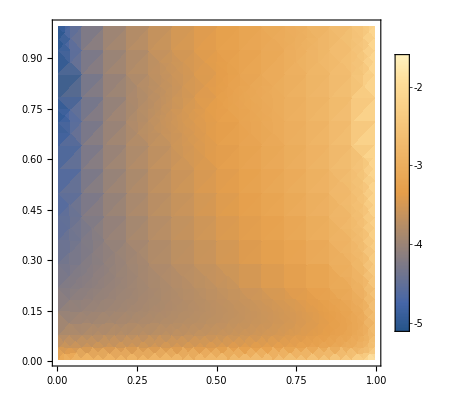

```mathematica
DensityPlot[ Log10[Total[dσdERdΩeofvχandϵ[ξω,cosθ,10^-3"c",1,ϵetest3][["dσdERdΩ"]]]],{ξω,ϵetest3["δ"]^(1/4),1-ϵetest3["δ"]^(1/4)},{cosθ,1-ϵetest3["δ"]^(1/4),ϵetest3["δ"]^(1/4)},PlotLegends->Automatic]
```

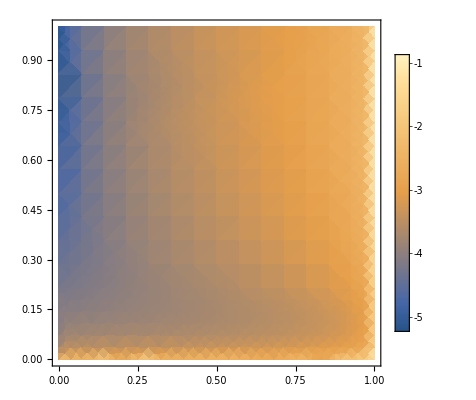

```mathematica
DensityPlot[ Log10[Total[dσdERdΩeofvχandϵ[ξω,cosθ,10^-3"c",1,ϵetest3][["dσdERdΩ"]]]],{ξω,ϵetest3["δ"]^(1/2),1-ϵetest3["δ"]^(1/2)},{cosθ,1-ϵetest3["δ"]^(1/2),ϵetest3["δ"]^(1/2)},PlotLegends->Automatic]
```

```mathematica
Block[{n=20,Max,ξs,Ms,σs,Booles,Error},
Max=MaxdσdERdΩ[[1]] ;
ξs=Table[{Random[],Random[]},{i,n}];
Ms=Max Table[Random[],{i,n}];
σs=Table[Total[dσdERdΩeofvχandϵ[ξs[[i,1]],ξs[[i,2]],10^-3"c",1,ϵetest3][["dσdERdΩ"]]],{i,n}];
Booles=Table[Ms[[i]]<= σs[[i]],{i,n}];
Error=Table[σs[[i]]-Max> 0,{i,n}];
<|"ξs"->ξs,"Ms"->Ms,"σs"->σs,"Booles"->Booles,"Max"->Max,"Error"->Error|>
]
Count[%["Booles"],True]
Count[%["Error"],True]
```

Part::pkspec1: The expression Capture`Private`i cannot be used as a part specification.

Total::level: Level specification {Capture`Private`i,2} is not of the form n, {n}, or {m, n}.

Part::pkspec1: The expression Capture`Private`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Total::level: Level specification {Capture`Private`i,2} is not of the form n, {n}, or {m, n}.

General::stop: Further output of Total::level will be suppressed during this calculation.

0

0

```mathematica
ϵInterpFeOsc2=Interpolateϵeuztrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
```

```mathematica
ϵInterpFeOsc2
```

```mathematica
ϵInterpFeOsc2=Interpolateϵeuztrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
```

```mathematica
MaxdσdERdΩ=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,10^-3"c",1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]]
```

{0.0055934,{ξω→0.982217,cosθ→0.784569}}

```mathematica
Block[{n=20,Max,ξs,Ms,σs,Booles,Error},
Max=MaxdσdERdΩ[[1]] ;
ξs=Table[{Random[],Random[]},{i,n}];
Ms=Max Table[Random[],{i,n}];
σs=Table[Total[dσdERdΩeofvχandϵ[ξs[[i,1]],ξs[[i,2]],10^-3"c",1,ϵInterpFeOsc2][["dσdERdΩ"]]],{i,n}];
Booles=Table[Ms[[i]]<= σs[[i]],{i,n}];
Error=Table[σs[[i]]-Max> 0,{i,n}];
<|"ξs"->ξs,"Ms"->Ms,"σs"->σs,"Booles"->Booles,"Max"->Max,"Error"->Error|>
]
Count[%["Booles"],True]
Count[%["Error"],True]
```

<|ξs→{{0.453512,0.245323},{0.333715,0.885747},{0.864976,0.00270548},{0.0198488,0.0469694},{0.103314,0.667639},{0.279626,0.161304},{0.670494,0.963401},{0.112148,0.296455},{0.0328369,0.391314},{0.467601,0.556531},{0.946839,0.899816},{0.211531,0.511917},{0.493327,0.654493},{0.877816,0.626169},{0.628351,0.651788},{0.857967,0.5792},{0.525037,0.984149},{0.578342,0.417895},{0.854543,0.0207472},{0.466194,0.12144}},Ms→{0.00459613,0.00352067,0.00558553,0.00315976,0.00489348,0.00408104,0.00440236,0.00029641,0.00213411,0.000420195,0.00508578,0.00238739,0.00421289,0.00236789,0.000286824,0.0047411,0.00127615,0.00245655,0.00264533,0.00240364},σs→{0.000199529,0.000228601,0.0109365,0.000240106,0.0000546818,0.000125215,0.000786791,0.000064937,0.0000339031,0.000353018,0.00309708,0.000114914,0.000419451,0.00176779,0.000667878,0.00152824,0.000516038,0.000430582,0.00140384,0.000185273},Booles→{False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False},Max→0.0055934,Error→{False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}|>

2

0

```mathematica
x=0
Do[
x+= i,
{i,10}]
```

0

```mathematica
NMax=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,10^-3"c",1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]][[1]]
```

Set::wrsym: Symbol Max is Protected.

0.0055934

```mathematica
Block[{n=20,vχ=10^-3"c",NMax,nits,ξs,Ms,σs,Bool,Error},
NMax=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]][[1]] ;
Print[NMax];
nits=0;
Do[
nits+=1;
ξs={Random[],Random[]};
Ms=NMax Random[];
σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵInterpFeOsc2][["dσdERdΩ"]]];
Bool=Ms<= σs;
Error=σs-NMax> 0;
If [Bool,Break[]],
{i,n}
];
<|"ξs"->ξs,"Ms"->Ms,"σs"->σs,"Booles"->Bool,"Max"->NMax,"Error"->Error,"nits"->nits|>
]
Count[%["Booles"],True]
Count[%["Error"],True]
```

0.0055934

<|ξs→{0.789864,0.966717},Ms→0.000392995,σs→0.00116977,Booles→True,Max→0.0055934,Error→False,nits→8|>

0

0

```mathematica
GetNMaxofdσdERdΩ[ϵDict_,vχ_,buffer_:1.1 ]:=buffer NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵDict][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵDict["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵDict["δ"]^(1/4),1-ϵDict["δ"]^(1/4)}]][[1]]
```

```mathematica
Block[{n=20,vχ=10^-3"c",ϵDict=ϵInterpFeOsc2,NMax,nits,ξs,Mξ,σs,Accepted,Errors=0},
(*NMax=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]][[1]] ;*)
NMax=GetNMaxofdσdERdΩ[ϵDict,vχ];
nits=0;
Accepted=False;
While[!Accepted,
nits+=1;
ξs={Random[],Random[]};
Mξ=NMax Random[];
σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];
Accepted=Mξ<= σs;
Errors+=Boole[σs-NMax> 0];
];
<|"ξω"->ξs[[1]],"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->σs,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
{"ξω","cosθ"}/.%
```

<|ξω→0.754651,cosθ→0.442654,Mξ→0.000792298,σs→0.000819689,Max→0.00615274,Errors→0,nits→2|>

{0.754651,0.442654}

```mathematica
Block[{vχ=10^-3"c",ϵDict=ϵInterpFeOsc2,NMax=GetNMaxofdσdERdΩ[ϵInterpFeOsc2,10^-3"c"/.SIConstRepl],nits=0,ξs,Mξ,σs,Accepted=False,Errors=0},
(*NMax=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]][[1]] ;*)
While[!Accepted,
nits+=1;
ξs={Random[],Random[]};
Mξ=NMax Random[];
σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];
Accepted=Mξ<= σs;
Errors=If[σs-NMax> 0,Break[];<|"ξω"->ξs[[1]],"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->σs|>,0];
];
<|"ξω"->ξs[[1]],"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->σs,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
```

<|ξω→0.693598,cosθ→0.656384,Mξ→0.000737322,σs→0.000839922,Max→0.00615274,Errors→0,nits→6|>

```mathematica
Getξωandcosθ[vχ_,ϵDict_,NMax_]:=Module[{nits=0,ξs,Mξ,σs,ω,Accepted=False,Errors=0},
(*NMax=NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵInterpFeOsc2][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵInterpFeOsc2["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵInterpFeOsc2["δ"]^(1/4),1-ϵInterpFeOsc2["δ"]^(1/4)}]][[1]] ;*)
While[!Accepted,
nits+=1;
ξs={Random[],Random[]};
Mξ=NMax Random[];
(*σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];*)
{σs,ω}={"dσdERdΩ","ω"}/.dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict];
σs=Total[σs];
Accepted=Mξ<= σs;
Errors=If[σs-NMax> 0,Break[];<|"ξω"->ξs[[1]],"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->σs|>,0];
];
<|"ξω"->ξs[[1]],"ω"->ω,"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->σs,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
```

```mathematica
Clear[x]
{x,y}= {b,c}
```

{b,c}

```mathematica
Clear[Getξωandcosθ]
```

```mathematica
("ℏ""ω")/("JpereV")/.Getξωandcosθ[10^-3"c",ϵInterpFeOsc2,NmaxFeOsc2]/.SIConstRepl
((10^-3"c")^2"mχ")/(2 "JpereV")/.ϵInterpFeOsc2/.ϵInterpFeOsc2[["params"]]
```

1.49791

2.55899

```mathematica
NmaxFeOsc2=GetNMaxofdσdERdΩ[ϵInterpFeOsc2,10^-3"c"/.SIConstRepl]
```

0.00615274

```mathematica
Table[{"ξω","cosθ"}/.Getξωandcosθ[10^-3"c",ϵInterpFeOsc2,NmaxFeOsc2],{i,1000}]
```

{{0.683885,0.33557},{0.503074,0.281114},{0.963072,0.381301},{0.853476,0.679876},{0.548698,0.604672},{0.97356,0.658989},{0.993615,0.446789},{0.928572,0.963544},{0.471352,0.855394},{0.792862,0.501494},{0.64409,0.983561},{0.414643,0.950829},{0.868902,0.16784},{0.961138,0.610101},{0.992235,0.751461},{0.841837,0.738644},{0.984962,0.78192},{0.763333,0.526273},{0.968454,0.47468},{0.997461,0.467297},{0.77783,0.903111},{0.7616,0.000298363},{0.726621,0.88363},{0.765379,0.265991},{0.949352,0.0160132},{0.724974,0.237245},{0.680016,0.00164627},{0.470387,0.995417},{0.593587,0.676886},{0.985803,0.717573},{0.269117,0.37604},{0.715852,0.79168},{0.992159,0.953921},{0.944988,0.22786},{0.800543,0.404442},{0.980138,0.833501},{0.389391,0.474365},{0.936738,0.754745},{0.714162,0.321053},{0.200376,0.00306455},{0.87294,0.931744},{0.469075,0.602152},{0.997489,0.438664},{0.374925,0.940103},{0.942807,0.984427},{0.992045,0.839053},{0.68151,0.697702},{0.573393,0.39705},{0.828108,0.891094},{0.983703,0.434946},{0.96127,0.885641},{0.998929,0.719772},{0.885413,0.494408},{0.865984,0.389447},{0.933163,0.0635568},{0.737034,0.244912},{0.592614,0.793708},{0.843014,0.224138},{0.668459,0.777641},{0.942244,0.485957},{0.854968,0.905092},{0.672233,0.206011},{0.898877,0.913665},{0.836555,0.671434},{0.871102,0.863465},{0.803285,0.610927},{0.715658,0.992916},{0.870923,0.525428},{0.801828,0.741917},{0.973163,0.660612},{0.743397,0.512846},{0.71723,0.116793},{0.970523,0.795724},{0.533541,0.759939},{0.95355,0.87459},{0.393398,0.546728},{0.718587,0.616841},{0.565524,0.00176889},{0.335242,0.280876},{0.797098,0.546968},{0.808442,0.384151},{0.738206,0.0494595},{0.987628,0.410737},{0.895272,0.203017},{0.508253,0.122271},{0.744301,0.8285},{0.997569,0.356127},{0.95989,0.449251},{0.995934,0.936185},{0.807166,0.566539},{0.945596,0.330752},{0.999794,0.129138},{0.949697,0.794176},{0.626792,0.901777},{0.999219,0.886514},{0.908926,0.559408},{0.794691,0.728496},{0.879409,0.506369},{0.881851,0.999805},{0.96116,0.603924},{0.226161,0.501138},{0.997826,0.879401},{0.696038,0.445045},{0.859622,0.918983},{0.507161,0.0316225},{0.951473,0.321602},{0.909243,0.268112},{0.997732,0.169146},{0.897186,0.531712},{0.89183,0.703456},{0.95454,0.0199271},{0.910979,0.741331},{0.981937,0.213726},{0.948033,0.768632},{0.856033,0.871911},{0.987757,0.671791},{0.938766,0.909683},{0.466303,0.394495},{0.951285,0.903085},{0.397384,0.00215521},{0.935546,0.708475},{0.955098,0.988721},{0.409275,0.242075},{0.532504,0.702661},{0.794579,0.971731},{0.849131,0.937099},{0.845291,0.919078},{0.746127,0.643381},{0.90463,0.194221},{0.739172,0.633285},{0.892084,0.751143},{0.983204,0.960916},{0.697074,0.46149},{0.892996,0.755391},{0.974204,0.972957},{0.124272,0.871123},{0.989894,0.767909},{0.683752,0.187827},{0.895685,0.361937},{0.740283,0.493736},{0.761219,0.0204247},{0.96842,0.635701},{0.630058,0.686978},{0.383754,0.236508},{0.907918,0.711942},{0.921951,0.707044},{0.981921,0.985792},{0.914949,0.821156},{0.255928,0.0443238},{0.651225,0.609301},{0.987803,0.997494},{0.532228,0.839556},{0.964023,0.0805133},{0.44282,0.000814404},{0.956599,0.920242},{0.989406,0.847981},{0.648393,0.820604},{0.95664,0.610917},{0.82248,0.341901},{0.943411,0.950361},{0.718515,0.76593},{0.877822,0.45492},{0.865745,0.722218},{0.709738,0.221718},{0.96912,0.900677},{0.89605,0.772175},{0.937302,0.563791},{0.947,0.751718},{0.997676,0.644814},{0.749445,0.0361927},{0.776016,0.970525},{0.703058,0.818285},{0.819518,0.00370309},{0.895891,0.0819963},{0.968265,0.903982},{0.964751,0.610615},{0.299182,0.458863},{0.833555,0.0162689},{0.90311,0.483016},{0.932638,0.510431},{0.402622,0.390674},{0.994608,0.768868},{0.97128,0.0574951},{0.223826,0.00253687},{0.758211,0.958731},{0.919405,0.832818},{0.943892,0.917594},{0.768463,0.894275},{0.351418,0.0009771},{0.937433,0.663904},{0.517257,0.961448},{0.999609,0.263755},{0.108473,0.000400636},{0.951816,0.617342},{0.656554,0.485406},{0.996159,0.712911},{0.470649,0.762111},{0.992575,0.604129},{0.934953,0.922946},{0.924316,0.538867},{0.86831,0.551556},{0.980346,0.703864},{0.907488,0.00809589},{0.967382,0.0144266},{0.686783,0.518663},{0.219546,0.00425485},{0.97281,0.850972},{0.874856,0.496812},{0.971159,0.00374407},{0.999543,0.656411},{0.903182,0.829556},{0.978087,0.399696},{0.145016,0.918689},{0.902116,0.699809},{0.815641,0.810697},{0.990627,0.355389},{0.638105,0.405865},{0.453443,0.832325},{0.953058,0.254828},{0.646214,0.393077},{0.799832,0.710081},{0.999742,0.140981},{0.994245,0.827955},{0.891328,0.866394},{0.807687,0.025367},{0.0514523,0.00239373},{0.342659,0.973731},{0.814279,0.826386},{0.650484,0.721485},{0.0987556,0.473642},{0.417365,0.00494689},{0.991326,0.460129},{0.976015,0.206817},{0.230191,0.97153},{0.976644,0.841092},{0.800579,0.701151},{0.948671,0.232663},{0.850575,0.778569},{0.922012,0.0338845},{0.971019,0.309587},{0.986138,0.554243},{0.9648,0.605999},{0.98563,0.412211},{0.733905,0.266664},{0.449677,0.308149},{0.567989,0.0125794},{0.910966,0.671046},{0.962847,0.720141},{0.204017,0.0018771},{0.713647,0.549283},{0.547351,0.0194134},{0.923585,0.666256},{0.98536,0.741879},{0.999528,0.33234},{0.249573,0.00801354},{0.996615,0.589636},{0.913875,0.664275},{0.928879,0.0734838},{0.938098,0.264604},{0.956961,0.389882},{0.727373,0.000729084},{0.966357,0.100631},{0.981436,0.683467},{0.922582,0.477232},{0.898698,0.852787},{0.834829,0.431477},{0.602448,0.908823},{0.926667,0.869944},{0.694447,0.728942},{0.685974,0.861819},{0.935383,0.80024},{0.946647,0.208078},{0.599783,0.737631},{0.662633,0.737249},{0.972154,0.273971},{0.961103,0.3382},{0.978195,0.411737},{0.93265,0.586567},{0.624324,0.00127425},{0.487388,0.560787},{0.977207,0.598871},{0.96119,0.436236},{0.963459,0.74095},{0.475704,0.745324},{0.968792,0.0163876},{0.49097,0.262117},{0.589271,0.857104},{0.870578,0.976523},{0.530857,0.0085728},{0.963833,0.293595},{0.330366,0.814988},{0.963433,0.245854},{0.612849,0.724528},{0.828205,0.845239},{0.992674,0.847593},{0.987286,0.87206},{0.784227,0.46623},{0.962298,0.527449},{0.913532,0.976322},{0.600589,0.871773},{0.992241,0.594124},{0.930325,0.738592},{0.955228,0.834936},{0.754423,0.951219},{0.936544,0.344149},{0.772764,0.367852},{0.994339,0.526751},{0.762372,0.735091},{0.647594,0.00839349},{0.755711,0.354748},{0.857803,0.825806},{0.912813,0.990924},{0.99052,0.999229},{0.717545,0.791262},{0.415287,0.675951},{0.958973,0.891895},{0.942587,0.921293},{0.842666,0.208518},{0.921714,0.865639},{0.762656,0.880484},{0.342727,0.00165328},{0.925376,0.657072},{0.425958,0.734984},{0.991138,0.117911},{0.745679,0.866274},{0.859758,0.839851},{0.528344,0.342206},{0.476877,0.52931},{0.927161,0.784433},{0.981842,0.326688},{0.850931,0.902061},{0.924597,0.760345},{0.499777,0.344426},{0.628254,0.739432},{0.800293,0.605718},{0.979502,0.680295},{0.738091,0.187748},{0.838024,0.150138},{0.966924,0.291108},{0.751002,0.271669},{0.741481,0.459894},{0.467731,0.707114},{0.897229,0.284416},{0.685356,0.845536},{0.989398,0.953395},{0.847621,0.568204},{0.96872,0.700954},{0.60981,0.871666},{0.40612,0.00171007},{0.848418,0.653085},{0.560176,0.567039},{0.982274,0.738595},{0.911733,0.22104},{0.955998,0.65032},{0.983372,0.651472},{0.82611,0.991844},{0.491901,0.415132},{0.985805,0.658938},{0.538862,0.728523},{0.818797,0.646453},{0.968053,0.580466},{0.625899,0.877779},{0.946858,0.348848},{0.654523,0.383721},{0.505039,0.0355969},{0.904042,0.515218},{0.989014,0.557576},{0.984693,0.953417},{0.610572,0.693312},{0.574095,0.90016},{0.963968,0.840234},{0.646148,0.00273813},{0.886354,0.503479},{0.921785,0.925313},{0.855122,0.0209786},{0.299355,0.916333},{0.969034,0.797727},{0.434937,0.110396},{0.920027,0.984536},{0.865138,0.788809},{0.985658,0.813528},{0.978597,0.076742},{0.961765,0.378659},{0.998913,0.504892},{0.83337,0.981697},{0.755953,0.983494},{0.836613,0.638569},{0.729699,0.673132},{0.99157,0.364397},{0.722126,0.0121451},{0.759032,0.948011},{0.819786,0.513605},{0.777012,0.00634597},{0.942,0.858337},{0.990477,0.447952},{0.796112,0.526036},{0.864345,0.74698},{0.915864,0.719554},{0.206175,0.538462},{0.890226,0.910398},{0.995234,0.437231},{0.928817,0.0214703},{0.888846,0.759474},{0.992447,0.908119},{0.823473,0.567873},{0.372813,0.740645},{0.927186,0.68834},{0.994872,0.571039},{0.951017,0.726071},{0.859566,0.876509},{0.793745,0.248841},{0.485049,0.591482},{0.72228,0.620849},{0.911168,0.945556},{0.616644,0.541758},{0.944981,0.481847},{0.385885,0.34634},{0.0161119,0.0174942},{0.968172,0.291379},{0.810812,0.877864},{0.273397,0.533352},{0.913917,0.334096},{0.378104,0.0190928},{0.783857,0.526152},{0.0951109,0.060323},{0.96311,0.877524},{0.273916,0.295255},{0.596641,0.475422},{0.929032,0.707081},{0.335041,0.165574},{0.691585,0.827334},{0.998767,0.397486},{0.996214,0.735554},{0.774142,0.0131804},{0.274443,0.0923034},{0.880509,0.728734},{0.907843,0.00742186},{0.658432,0.481283},{0.49764,0.50582},{0.607407,0.225507},{0.982224,0.234907},{0.985736,0.00999767},{0.85906,0.800382},{0.800588,0.931029},{0.950369,0.660987},{0.669722,0.00384459},{0.779588,0.942681},{0.978498,0.854747},{0.700423,0.28328},{0.95766,0.0662205},{0.728156,0.721182},{0.973632,0.68645},{0.417914,0.818909},{0.901319,0.46102},{0.620855,0.857249},{0.800034,0.00459578},{0.696897,0.909708},{0.807216,0.861541},{0.888403,0.987992},{0.801734,0.856521},{0.991147,0.677092},{0.942011,0.13372},{0.855259,0.993518},{0.795395,0.219161},{0.794509,0.277074},{0.921842,0.654879},{0.994238,0.0301248},{0.363387,0.716108},{0.699691,0.610711},{0.378196,0.262403},{0.133907,0.0240756},{0.983476,0.662202},{0.876023,0.0896283},{0.910422,0.81609},{0.907105,0.972698},{0.98502,0.621234},{0.249841,0.551268},{0.97478,0.542417},{0.815965,0.785426},{0.891192,0.736466},{0.993728,0.379289},{0.859386,0.576167},{0.865526,0.744927},{0.810745,0.0949203},{0.541965,0.470427},{0.754539,0.644576},{0.837646,0.184927},{0.374767,0.538041},{0.818676,0.720233},{0.461761,0.358413},{0.86563,0.52297},{0.962895,0.920493},{0.398378,0.00084965},{0.969514,0.761849},{0.358432,0.419604},{0.964312,0.528651},{0.558762,0.250474},{0.820925,0.409927},{0.973776,0.666029},{0.989199,0.650781},{0.355058,0.000633964},{0.998268,0.29603},{0.216232,0.127381},{0.313818,0.584312},{0.378123,0.293384},{0.201361,0.00186548},{0.993297,0.896287},{0.882613,0.831847},{0.959657,0.513313},{0.654075,0.999951},{0.155996,0.0128449},{0.936073,0.789853},{0.99986,0.501397},{0.551901,0.714589},{0.56667,0.0192018},{0.583919,0.153979},{0.835669,0.679346},{0.914349,0.577029},{0.942843,0.778779},{0.871296,0.778358},{0.808548,0.551194},{0.787055,0.00380779},{0.970593,0.652179},{0.445461,0.00938269},{0.617768,0.286471},{0.915799,0.615227},{0.781808,0.026268},{0.986679,0.00153607},{0.870121,0.517642},{0.785766,0.629301},{0.760504,0.470919},{0.713608,0.659769},{0.942397,0.543929},{0.894831,0.423483},{0.981209,0.512849},{0.991487,0.40201},{0.811223,0.360904},{0.971894,0.500129},{0.50655,0.770044},{0.992742,0.246367},{0.782677,0.892899},{0.411007,0.467106},{0.494885,0.000339166},{0.957141,0.440699},{0.957176,0.724225},{0.528325,0.567166},{0.736524,0.793793},{0.686259,0.783413},{0.989397,0.793425},{0.951328,0.266631},{0.984233,0.532552},{0.747029,0.989524},{0.97508,0.589402},{0.838622,0.191303},{0.797652,0.585004},{0.904054,0.0209825},{0.686124,0.907062},{0.873235,0.38879},{0.902585,0.686411},{0.309448,0.351889},{0.522725,0.796827},{0.403061,0.0476361},{0.923475,0.443033},{0.620972,0.520538},{0.0450755,0.033211},{0.983062,0.137929},{0.968467,0.849912},{0.85575,0.858085},{0.680008,0.395655},{0.668113,0.00262268},{0.959301,0.628624},{0.488186,0.000919884},{0.674514,0.0896687},{0.592304,0.331536},{0.884885,0.645261},{0.79902,0.855409},{0.461649,0.831857},{0.960892,0.543464},{0.877767,0.686877},{0.879663,0.000456888},{0.369883,0.671603},{0.500556,0.811778},{0.992695,0.250856},{0.947729,0.931501},{0.920284,0.999684},{0.700148,0.254679},{0.937357,0.017192},{0.996475,0.0265105},{0.918484,0.922571},{0.852401,0.890788},{0.974384,0.259638},{0.991616,0.41122},{0.975579,0.506833},{0.951929,0.589934},{0.676545,0.708986},{0.95479,0.336516},{0.84856,0.591444},{0.770578,0.617794},{0.988305,0.824364},{0.833554,0.573295},{0.178858,0.95857},{0.597938,0.439433},{0.622819,0.809103},{0.956324,0.772363},{0.372831,0.365976},{0.471535,0.89872},{0.932666,0.71084},{0.727254,0.898047},{0.670163,0.95428},{0.82756,0.469202},{0.252611,0.00168528},{0.898802,0.55162},{0.940561,0.476936},{0.969102,0.942951},{0.794987,0.969073},{0.682717,0.886824},{0.504861,0.440654},{0.81275,0.616317},{0.182714,0.245739},{0.707004,0.831637},{0.960122,0.00896108},{0.590842,0.714383},{0.991827,0.967985},{0.627461,0.323713},{0.840044,0.183885},{0.888239,0.393903},{0.703287,0.171243},{0.979904,0.783884},{0.799431,0.00152663},{0.796345,0.580973},{0.569821,0.283705},{0.991296,0.58773},{0.720672,0.528892},{0.993085,0.687859},{0.809225,0.915777},{0.996029,0.490185},{0.652676,0.814226},{0.93637,0.418763},{0.924693,0.642675},{0.42985,0.428218},{0.871086,0.904264},{0.660893,0.0416459},{0.978756,0.583797},{0.999597,0.185458},{0.986617,0.795436},{0.973521,0.721343},{0.333409,0.191531},{0.963598,0.854077},{0.547307,0.865321},{0.792956,0.964285},{0.227679,0.23546},{0.87307,0.803325},{0.957614,0.322552},{0.920483,0.393813},{0.900652,0.213044},{0.954199,0.751813},{0.635696,0.363707},{0.674296,0.0293575},{0.913182,0.684914},{0.7925,0.724803},{0.897814,0.958892},{0.992455,0.745508},{0.815498,0.521115},{0.744657,0.783577},{0.447027,0.620886},{0.986446,0.0528125},{0.750251,0.136496},{0.71209,0.661203},{0.971551,0.677211},{0.946637,0.402987},{0.976106,0.475609},{0.401449,0.333348},{0.910361,0.675878},{0.381583,0.0892826},{0.825038,0.734143},{0.744847,0.601727},{0.400756,0.730471},{0.882485,0.528147},{0.64019,0.00207903},{0.776524,0.447354},{0.764865,0.427887},{0.94276,0.686413},{0.716429,0.447605},{0.865346,0.601973},{0.0250964,0.166914},{0.757451,0.698451},{0.563375,0.273836},{0.998037,0.737155},{0.562646,0.839305},{0.893273,0.789983},{0.912607,0.0120709},{0.985628,0.299431},{0.599812,0.620363},{0.98334,0.395359},{0.996291,0.284924},{0.148328,0.815226},{0.272684,0.944677},{0.863718,0.111026},{0.984078,0.569449},{0.535921,0.66157},{0.726009,0.685042},{0.162964,0.0101478},{0.942867,0.872181},{0.225717,0.0382078},{0.916603,0.689673},{0.813183,0.466698},{0.823901,0.977397},{0.972927,0.715043},{0.839657,0.0460154},{0.872577,0.630426},{0.888829,0.0864894},{0.897867,0.842814},{0.0179901,0.0356061},{0.898514,0.935547},{0.168796,0.96173},{0.105589,0.119267},{0.969582,0.48699},{0.90174,0.725892},{0.636114,0.625986},{0.964249,0.723496},{0.517069,0.433304},{0.964525,0.864523},{0.809549,0.740745},{0.996226,0.603972},{0.833687,0.2988},{0.901849,0.848661},{0.940913,0.276857},{0.718235,0.696367},{0.597792,0.839536},{0.87966,0.523939},{0.861028,0.834235},{0.802146,0.736318},{0.997912,0.122176},{0.73582,0.920218},{0.915994,0.694072},{0.992189,0.628504},{0.990112,0.260903},{0.132265,0.549898},{0.762824,0.397486},{0.735721,0.694294},{0.956567,0.690185},{0.687991,0.890306},{0.726204,0.997325},{0.999491,0.265506},{0.953392,0.652887},{0.284342,0.00197082},{0.603022,0.490367},{0.797119,0.000907906},{0.673346,0.379033},{0.814658,0.374301},{0.181472,0.00174759},{0.83579,0.571435},{0.973705,0.632734},{0.352332,0.527127},{0.354927,0.725514},{0.892273,0.748878},{0.72837,0.142264},{0.672134,0.713813},{0.993894,0.995586},{0.844587,0.617456},{0.654626,0.92237},{0.109457,0.0826444},{0.597681,0.00871896},{0.0724632,0.932341},{0.724295,0.0978589},{0.987177,0.242519},{0.975108,0.872524},{0.655637,0.366921},{0.844269,0.693127},{0.960206,0.198711},{0.976539,0.233018},{0.671308,0.777828},{0.489047,0.870878},{0.95932,0.359816},{0.991857,0.969156},{0.932567,0.278173},{0.993338,0.667892},{0.914883,0.983234},{0.868279,0.339005},{0.519648,0.704734},{0.738998,0.0775675},{0.997464,0.0144825},{0.717034,0.298919},{0.544087,0.34126},{0.202604,0.00471943},{0.507332,0.356515},{0.970257,0.828694},{0.848954,0.402101},{0.941616,0.886009},{0.751037,0.886028},{0.997572,0.771722},{0.998701,0.295586},{0.86541,0.887227},{0.990557,0.613607},{0.518018,0.833438},{0.988029,0.809361},{0.426732,0.220614},{0.945482,0.433918},{0.395849,0.239901},{0.933741,0.16923},{0.778442,0.745219},{0.956891,0.0263188},{0.954057,0.219421},{0.970967,0.400333},{0.965922,0.024929},{0.546296,0.00158057},{0.672399,0.00349208},{0.967136,0.820425},{0.230743,0.737853},{0.610672,0.53142},{0.97149,0.952353},{0.956079,0.339259},{0.601308,0.0030858},{0.531367,0.573042},{0.625706,0.0574494},{0.755205,0.579004},{0.669325,0.44566},{0.721072,0.788254},{0.814017,0.00382934},{0.956131,0.672139},{0.934615,0.923697},{0.904177,0.658728},{0.860571,0.471504},{0.845454,0.709382},{0.90361,0.930721},{0.907752,0.584315},{0.998395,0.393032},{0.930363,0.270906},{0.497749,0.760329},{0.798608,0.729769},{0.830975,0.233779},{0.780498,0.901764},{0.504852,0.945475},{0.188072,0.268315},{0.992096,0.648784},{0.869479,0.450125},{0.777414,0.691432},{0.311419,0.888429},{0.705194,0.745801},{0.840012,0.368332},{0.340686,0.29516},{0.790218,0.969826},{0.873634,0.632182},{0.771951,0.311833},{0.899345,0.0523227},{0.816618,0.287639},{0.976433,0.710709},{0.844129,0.70042},{0.273445,0.197395},{0.680794,0.378163},{0.616967,0.819646},{0.952696,0.878881},{0.959922,0.218406},{0.886969,0.64045},{0.889711,0.690565},{0.850124,0.822388},{0.86167,0.775029},{0.547369,0.26702},{0.713794,0.853003},{0.826596,0.861305},{0.999543,0.612457},{0.925231,0.577009},{0.103559,0.771486},{0.951974,0.787451},{0.973945,0.667065},{0.997298,0.794844},{0.941573,0.69253},{0.979739,0.624616},{0.554064,0.840436},{0.956897,0.920828},{0.654306,0.903526},{0.926737,0.996218},{0.828856,0.47926},{0.973694,0.0131632},{0.917112,0.876632},{0.964469,0.729715},{0.816023,0.00997283},{0.563756,0.286766},{0.975122,0.244982},{0.993785,0.579009},{0.95809,0.780356},{0.908145,0.970308},{0.534482,0.968304},{0.966288,0.134139},{0.591359,0.997984},{0.984846,0.401622},{0.963561,0.837448},{0.881015,0.625173},{0.639297,0.00741128},{0.665256,0.98459},{0.826884,0.641152},{0.943492,0.591266},{0.982459,0.641856},{0.314187,0.0173569},{0.896397,0.663372},{0.835689,0.0250516},{0.98691,0.734523},{0.718012,0.607839},{0.337614,0.96138},{0.972232,0.654228},{0.87057,0.860637},{0.368483,0.00135073},{0.45758,0.0284191},{0.714831,0.819138},{0.992578,0.762553},{0.45926,0.672486},{0.87434,0.404843},{0.935013,0.298042},{0.998282,0.031814},{0.763363,0.00605667},{0.86128,0.388245},{0.868353,0.0196704},{0.926238,0.877257},{0.822157,0.0386928},{0.953701,0.00936174},{0.972532,0.624839},{0.173001,0.0936221},{0.393201,0.575836},{0.820467,0.407897},{0.999866,0.0877774},{0.907747,0.841552},{0.870701,0.524964},{0.707926,0.104077},{0.969,0.221967},{0.948993,0.965964},{0.91539,0.66613},{0.816943,0.825214},{0.815019,0.586695},{0.379536,0.00523956},{0.34121,0.55751},{0.615053,0.506788},{0.976597,0.808441},{0.713955,0.72025},{0.782562,0.902467},{0.555872,0.763661},{0.795872,0.909158},{0.727873,0.354594},{0.927926,0.702027},{0.695406,0.00921222},{0.850084,0.924352},{0.921505,0.423767},{0.99793,0.798746},{0.437167,0.368821},{0.251787,0.63842},{0.872349,0.776844},{0.988559,0.757973},{0.796711,0.309115},{0.572795,0.0268703},{0.83635,0.468465},{0.99159,0.564295},{0.594507,0.809381},{0.974724,0.344234},{0.675762,0.035014},{0.824536,0.652764},{0.843596,0.422526},{0.439127,0.332636},{0.847416,0.690727},{0.930918,0.79458},{0.957265,0.519935},{0.897843,0.937855},{0.631573,0.529911},{0.6081,0.87317},{0.998346,0.236327},{0.927158,0.533573},{0.955942,0.440729},{0.954254,0.211373},{0.903665,0.522989},{0.571863,0.704618},{0.979098,0.569376},{0.981939,0.921071},{0.772848,0.379707},{0.772481,0.365249},{0.0267432,0.0189678},{0.82499,0.489406},{0.972182,0.806022},{0.647413,0.816582},{0.615993,0.00314588},{0.95666,0.825546},{0.995967,0.469445},{0.996458,0.992821},{0.970976,0.693861},{0.85648,0.522772},{0.498167,0.376559},{0.0314625,0.00227876},{0.813586,0.625299},{0.974162,0.370258},{0.995088,0.397112},{0.933961,0.905385},{0.616786,0.498949},{0.976336,0.816238},{0.124618,0.514151},{0.339997,0.00870911},{0.916996,0.0215245},{0.80028,0.158337},{0.938698,0.877607},{0.456493,0.716902},{0.919761,0.773157},{0.328045,0.389305},{0.935532,0.764878},{0.00827575,0.443657}}

## Assemble

Parameters

```mathematica
FeλeDictOscillators;
SiO2λeDictOscillators;
MgOλeDictOscillators;
```

Get ϵs

```mathematica
ϵInterpFeOsc2=Interpolateϵeuztrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
```

Get Nmaxes

```mathematica
NmaxFeOsc2=GetNMaxofdσdERdΩ[ϵInterpFeOsc2]
```

0.00615274

```mathematica
Getξωandcosθ[10^-3"c",ϵInterpFeOsc2,NmaxFeOsc2]
```

<|ξω→0.846348,ω→1.58581×10^14,cosθ→0.219589,Mξ→0.0000697679,dσdERdΩ→0.000619262,Max→0.00615274,Errors→0,nits→3|>

So we can use NIntegrate to get the xsections if need be

```mathematica
NIntegrate[Total@dσdERdΩeofvχandϵ[ξω,cosθ,10^5,1,ϵInterpFeOsc2]["dσdERdΩ"],{ξω,ϵInterpFeOsc2["δ"]^(1/4),1},{cosθ,ϵInterpFeOsc2["δ"]^(1/4),1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00145362

```mathematica
ϵInterpFeOsc2["δ"]^(1/4)
```

1/(10 10^(3/4))

Get λs

```mathematica
FeλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["FeλeDictSIOscillator_``",i]]],{i,6}];
SiO2λeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["SiO2λeDictSIOscillator_``",i]]],{i,2}];
MgOλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["MgOλeDictSIOscillator_``",i]]],{i,4}];
```

Assemble material data into a dictionary, We need the following information to be filled

```mathematica
ϵInterpFeOsc2=Interpolateϵeuztrunced[10 "m"/.SIConstRepl,FeTotalparams[[2]],True,200,200,10^-7];
ϵs={ϵInterpFeOsc2};
dσdERdΩsMaxes = {GetNMaxofdσdERdΩ[ϵs[[1]],Abs[vχ]]};
dσdERdΩsample = {(Getξωandcosθ[#,ϵInterpFeOsc2,dσdERdΩsMaxes[[1]]])&};
λs = {FeλeDictOscillators[[2]]};
σs={1/("ne"/.λs[[1]])10^("f"/.λs[[1]])[Log10[mχ],Log10[#]]&};
```

```mathematica
Clear[ProcessDataAssembler]
ProcessDataAssembler[mχ_,params_,dσdERdΩsampler_,λDict_,ProcNum_:1,uselog_:True,m_:200,n_:200,δ_:10^-7]:= Module[{ϵDict,dσdERdΩsMax,dσdERdΩsample,σ},
ϵDict= Interpolateϵeuztrunced[mχ,params,uselog,m,n,δ];
dσdERdΩsMax = GetNMaxofdσdERdΩ[ϵDict,#]&;
dσdERdΩsample = Getξωandcosθ[#,ϵDict,dσdERdΩsMax]&;
σ=1/("ne"/.λDict["fitparams"][[1]])10^("f"/.λDict)[Log10[mχ],Log10[#]]&;
<|"ProcNum"->ProcNum,"ϵDict"->ϵDict,"dσdERdΩsMax"->dσdERdΩsMax,"dσdERdΩsample"->dσdERdΩsample,"σ"->σ,"λ"->λDict["f"]|>
]
```

```mathematica
FeOsc2Test=ProcessDataAssembler[10 "m"/.SIConstRepl,FeTotalparams[[2]],Getξωandcosθ,FeλeDictOscillators[[2]]]
```

```mathematica
"σ"[10^5]/.FeOsc2Test
```

5.11314×10^-22

```mathematica
FeDatae=Table[ProcessDataAssembler[10 "m"/.SIConstRepl,FeTotalparams[[i]],Getξωandcosθ,FeλeDictOscillators[[i]],i],{i,Length[FeTotalparams]}]
```

```mathematica
SaveIt[NotebookDirectory[]<>"FeMCDatae",FeDatae]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeMCDatae.dat

```mathematica
"dσdERdΩsMax"/.FeOsc2Test
%[10^5]
```

GetNMaxofdσdERdΩ[ϵDict$2236527,#1]&

559.34

```mathematica
"dσdERdΩsMax"/.FeDatae
%[[1]][3 10^5]
```

{GetNMaxofdσdERdΩ[ϵDict$2440487,#1]&,GetNMaxofdσdERdΩ[ϵDict$2642505,#1]&,GetNMaxofdσdERdΩ[ϵDict$2844512,#1]&,GetNMaxofdσdERdΩ[ϵDict$3046519,#1]&,GetNMaxofdσdERdΩ[ϵDict$3248526,#1]&,GetNMaxofdσdERdΩ[ϵDict$3450533,#1]&}

5208.38

Run MC

```mathematica
Block[{mχ,κ,vχ,r,λs,σs,ϵs,dσdERdΩsMaxes,dσdERdΩsample,V,nits,ncaptured,nescaped,ProcNum,l,reached,ER,cosθ,ϕ,q},
(*
Psuedo Code
initialize cross-sections, interaction lengths, and cross-sections for each process
Get initial conditions: vχ (with perp and radial components) at earth's radius
While in the Earth
	Get interaction length in the Earth
	Update radius according to interaction length and velocity
	Update velocity according to potential change 
	select process - omit for now
	sample to find ω and cosθ 
	update velocity
*)
(*Initial Conditions*)
mχ=10 "m"/.SIConstRepl;
κ=10^-6.5;
{vχ,r} = {{-10^-3"c"/.SIConstRepl,0,0},"rE"/.EarthRepl};

(*Initialize physics processes*)
λs = {FeλeDictOscillators[[2]]};(*Should this be "f"?*)
σs={1/("ne"/.λs[[1]]["fitparams"][[1]])10^("f"/.λs[[1]])[Log10[mχ],Log10[#]]&};
(*Print[σs[[1]][√(vχ.vχ)]];*)
(*Print[Length[σs]];
Print[Table[σs[[i]][√(vχ.vχ)],{i,Length[σs]}]];*)
ϵs={ϵInterpFeOsc2};
dσdERdΩsMaxes = {GetNMaxofdσdERdΩ[ϵs[[1]],Abs[vχ]]};
dσdERdΩsample = {(Getξωandcosθ[#,ϵInterpFeOsc2,dσdERdΩsMaxes[[1]]])&};
V=Vgrav;

(*Propagate*)
(*Print[vχ];*)
nits=0;
ncaptured=0;
nescaped=0;
While[nits<30,
nits++;
Print["N iterations: ",nits];
ProcNum=σselector[Table[σs[[i]][√(vχ.vχ)],{i,Length[σs]}]];
Print["Process number: ",ProcNum];
l = Getl[mχ,√(vχ.vχ),κ,λs[[ProcNum]]["f"]];
Print["l is ",l];
{vχ,r,reached}={"vχ","r","reached?"}/.Updatev[vχ,mχ,r,l,V];
Print["vχ is ",vχ];
Print["r is ",r];
Print[reached];
If[r>"rE"/.Constants`EarthRepl  ,nescaped++;Break[]];
{ER,cosθ}={"ℏ""ω"/.Constants`SIConstRepl,"cosθ"}/.dσdERdΩsample[[ProcNum]][√(vχ.vχ)];
ϕ=2 π Random[];
q=(√(2 mχ ER))/("ℏ")/.Constants`SIConstRepl;
vχ = Rotatevχ[vχ,cosθ,mχ,ϕ,q];
If[√(vχ.vχ)<"vesc"/.Constants`EarthRepl,ncaptured++;Print["Captured with: v_χ=",√(vχ.vχ)];Break[]];
(*Print["vχ after scatter is ",vχ];*)
];
<|"ER"->ER,"vχ"->vχ,"|vχ|"->√(vχ.vχ),"ϕ"->ϕ,"l"->l,"cosθ"->cosθ,"q"->q,"r"->r,"reached?"->reached,"κ"->N@κ,"nits"->nits,"ncaptured"->ncaptured,"nescaped"->nescaped,"dσdERdΩsMaxes"->dσdERdΩsMaxes|>
]
```

N iterations: 1

Process number: 1

l is 173010.

vχ is {-300214.,0,0}

r is 6.19799×10^6

True

N iterations: 2

Process number: 1

l is 76382.4

vχ is {-256377.,-12178.4,96934.7}

r is 6.12662×10^6

True

N iterations: 3

Process number: 1

l is 148852.

vχ is {-256064.,-11402.7,56075.5}

r is 5.98136×10^6

True

N iterations: 4

Process number: 1

l is 87802.3

vχ is {-181517.,26501.8,100522.}

r is 5.90521×10^6

True

N iterations: 5

Process number: 1

l is 42832.

vχ is {-191701.,22967.4,67860.9}

r is 5.8651×10^6

True

N iterations: 6

Process number: 1

l is 72304.3

vχ is {-193249.,34530.3,55368.7}

r is 5.7966×10^6

True

N iterations: 7

Process number: 1

l is 22000.5

vχ is {-193050.,34816.5,57050.8}

r is 5.77582×10^6

True

N iterations: 8

Process number: 1

l is 132656.

vχ is {-158274.,67095.7,87620.4}

r is 5.6671×10^6

True

N iterations: 9

Process number: 1

l is 77570.

vχ is {-25608.1,82273.5,22720.8}

r is 5.64713×10^6

True

N iterations: 10

Process number: 1

l is 92380.6

vχ is {-20566.1,84136.4,21291.7}

r is 5.62951×10^6

True

N iterations: 11

Process number: 1

l is 297047.

vχ is {-27529.7,82728.2,19671.9}

r is 5.54617×10^6

True

N iterations: 12

Process number: 1

l is 68356.

vχ is {-34951.8,72929.8,33917.6}

r is 5.52031×10^6

True

N iterations: 13

InterpolatingFunction::dmval: Input value {-29.0405,4.57618} lies outside the range of data in the interpolating function. Extrapolation will be used.

Process number: 1

InterpolatingFunction::dmval: Input value {-29.0405,4.57618} lies outside the range of data in the interpolating function. Extrapolation will be used.

l is 32653.9

vχ is {-11889.9,37603.7,-2331.14}

r is 5.51954×10^6

True

N iterations: 14

InterpolatingFunction::dmval: Input value {-29.0405,4.5952} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Process number: 1

l is 51884.8

vχ is {-16103.4,37785.,-2021.52}

r is 5.5052×10^6

True

N iterations: 15

Process number: 1

l is 9988.94

vχ is {-20749.8,37279.6,732.747}

r is 5.50105×10^6

True

N iterations: 16

Process number: 1

l is 13701.8

vχ is {-11874.,30007.8,-5258.68}

r is 5.50119×10^6

True

N iterations: 17

Process number: 1

l is 197738.

vχ is {-18765.4,27340.,-257.242}

r is 5.40864×10^6

True

N iterations: 18

Process number: 1

l is 9487.57

vχ is {-22285.6,1950.57,-1038.76}

r is 5.39922×10^6

True

N iterations: 19

Process number: 1

l is 17345.6

vχ is {-17206.6,10208.4,-5234.78}

r is 5.38649×10^6

True

N iterations: 20

Process number: 1

l is 11378.1

vχ is {-16411.,12985.1,-2389.4}

r is 5.37912×10^6

True

N iterations: 21

Process number: 1

l is 23661.9

vχ is {-12544.5,8621.83,-6878.21}

r is 5.37145×10^6

True

N iterations: 22

Process number: 1

l is 5526.48

vχ is {-14389.4,10770.1,1499.18}

r is 5.36817×10^6

True

N iterations: 23

Process number: 1

l is 63398.

vχ is {-16685.7,8080.7,7344.53}

r is 5.32201×10^6

True

N iterations: 24

Process number: 1

l is 73.3632

vχ is {-20903.9,2380.07,6762.86}

r is 5.32195×10^6

True

N iterations: 25

Process number: 1

l is 78392.7

vχ is {-17002.2,-2268.83,-1731.02}

r is 5.24568×10^6

True

N iterations: 26

Process number: 1

l is 28901.6

vχ is {-20847.8,-2290.34,-1712.58}

r is 5.21718×10^6

True

N iterations: 27

Process number: 1

l is 17362.9

vχ is {-22669.4,-5195.92,-2145.58}

r is 5.20052×10^6

True

N iterations: 28

Process number: 1

l is 14738.3

vχ is {-22490.8,-10495.5,-3575.12}

r is 5.18779×10^6

True

N iterations: 29

Process number: 1

l is 31396.2

vχ is {-13449.7,-13270.1,-858.608}

r is 5.17509×10^6

True

N iterations: 30

Process number: 1

l is 690.722

vχ is {-13376.7,-7498.5,8282.88}

r is 5.17477×10^6

True

<|ER→1.4939×10^-22,vχ→{-13475.4,-2385.61,5704.98},|vχ|→14826.5,ϕ→2.07486,l→690.722,cosθ→0.584801,q→4.94518×10^8,r→5.17477×10^6,reached?→True,κ→3.16228×10^-7,nits→30,ncaptured→0,nescaped→0,dσdERdΩsMaxes→{{1678.02,0.,0.}}|>

#### Debug and sanity check of potential and vupdate

```mathematica
Clear[Updatev]
```

```mathematica
Updatev[{-50954.58712980515,-3107.8972344737203,-51252.74687355745},10"m"/.SIConstRepl,5.497149438202962*^6,116594,Vgrav]
```

<|vχ→{50968.1,-3107.9,-51252.7},r→5.41502×10^6,vr→50968.1,reached?→True,E→2.31936×10^-20,vp→51346.9,Δr→-82127.6,V[r]→-7.04867×10^7,V[|r+Δr|]→-7.11767×10^7,l→116594,vr0→-50954.6,mχ→9.11×10^-30|>

```mathematica
"vr"/.Updatev["c" 10^-4{1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,10^6,10^4,Vgrav]
```

26722.

```mathematica
Integrate[-r^2(("ME" "G")/(2("rE")^3))( -r^-1),{r,0,rp}]
%/.r->"rE"
```

(G ME rp^2)/(4 rE^3)

(G ME rp^2)/(4 rE^3)

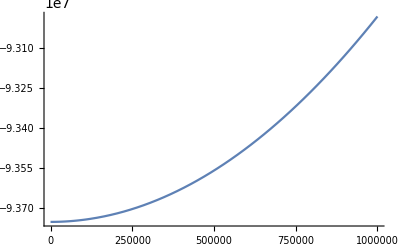

```mathematica
Plot[Vgrav[r],{r,1,10^6},PlotRange->All]
```

```mathematica
-"V[|r+Δr|]"/.Updatev["c" 10^-4{0.1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,10^5,10^4,Vgrav]
```

9.37434×10^7

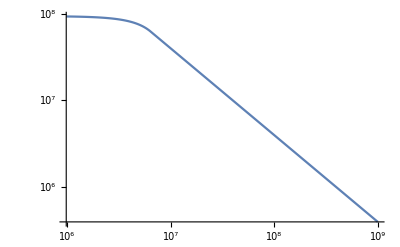

```mathematica
LogLogPlot[-"V[|r+Δr|]"/.Updatev["c" 10^-4{0.1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,r,10^4,Vgrav],{r,0,10^9},PlotRange->All]
```

```mathematica
Table["vr"/.Updatev["c" 10^-4{0.1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,frac"rE"/.EarthRepl,10^4,Vgrav],{frac,0,10,0.05}]
```

{14018.,14012.1,13995.,13966.7,13927.2,13876.2,13813.8,13739.7,13653.8,13555.8,13445.5,13322.6,13186.6,13037.3,12874.1,12696.5,12503.9,12295.6,12070.7,11828.4,11567.5,11308.1,11067.,10842.1,10631.7,10434.4,10248.9,10074.1,9909.,9752.75,9604.61,9463.93,9330.1,9202.6,9080.95,8964.74,8853.58,8747.13,8645.06,8547.1,8452.98,8362.46,8275.33,8191.39,8110.44,8032.34,7956.9,7884.,7813.5,7745.27,7679.2,7615.17,7553.1,7492.88,7434.43,7377.66,7322.51,7268.89,7216.74,7166.,7116.61,7068.5,7021.63,6975.95,6931.41,6887.97,6845.57,6804.19,6763.79,6724.32,6685.75,6648.06,6611.21,6575.17,6539.91,6505.41,6471.64,6438.57,6406.19,6374.47,6343.39,6312.93,6283.07,6253.8,6225.08,6196.91,6169.28,6142.16,6115.54,6089.4,6063.74,6038.53,6013.77,5989.44,5965.54,5942.04,5918.94,5896.24,5873.91,5851.94,5830.34,5809.09,5788.18,5767.59,5747.34,5727.4,5707.77,5688.44,5669.4,5650.65,5632.18,5613.98,5596.05,5578.39,5560.97,5543.81,5526.89,5510.21,5493.76,5477.54,5461.55,5445.77,5430.2,5414.85,5399.7,5384.75,5370.,5355.44,5341.07,5326.88,5312.88,5299.05,5285.4,5271.92,5258.6,5245.45,5232.46,5219.63,5206.95,5194.43,5182.05,5169.82,5157.74,5145.79,5133.99,5122.32,5110.78,5099.38,5088.1,5076.96,5065.93,5055.03,5044.25,5033.59,5023.04,5012.61,5002.29,4992.08,4981.98,4971.98,4962.09,4952.31,4942.63,4933.04,4923.56,4914.17,4904.88,4895.68,4886.57,4877.56,4868.63,4859.8,4851.05,4842.38,4833.8,4825.3,4816.89,4808.55,4800.3,4792.12,4784.02,4776.,4768.05,4760.17,4752.37,4744.64,4736.98,4729.39,4721.87,4714.41,4707.03,4699.71,4692.45,4685.26,4678.13,4671.06,4664.06,4657.11,4650.23,4643.4,4636.64}

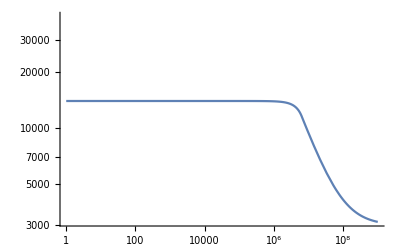

```mathematica
LogLogPlot["vr"/.Updatev["c" 10^-4{0.1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,r,10^4,Vgrav],{r,1,10^9},PlotRange->{{1,10^9},{0,4 10^4}}]
```

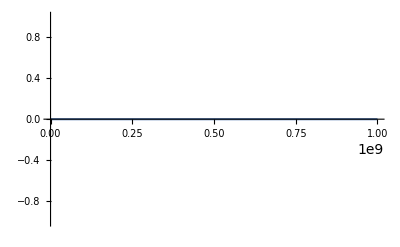

```mathematica
Plot[Boole["reached?"]/.Updatev["c" 10^-4{1,0,0}/.SIConstRepl,10"m"/.SIConstRepl,r,10^3,Vgrav],{r,0,10^9}]
```

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
(*Block[{vχ={3,0,0},vχhat, w,Rϕ,Δvχ,vχp,ϕ=2 π Random[],cosθ=Random[]},
vχhat=vχ/(√(vχ.vχ));
(*Rotate by θ about an arbitrary axis orthogonal to vχ*)
(*w={a,b,0};
w=w/.Solve[vχ.w==0,b][[1]];
w=w/(√(w.w))//PowerExpand;*)
w=Cross[vχhat,{0,1,0}];
w=w/(√(w.w));
Δvχ=("ℏ" q)/mχ(w √(1-cosθ^2) + vχ cosθ);

(*Rotate about vχ by ϕ*)
vχp = vχ + RotateuAboutvbyϕ[Δvχ,vχhat,ϕ]

]*)
```

{{1/(√14),√(2/7),3/(√14)},{-1/(√35),√(5/7),-3/(√35)}}

## Scrap

#### Computed Cross-Sections

```mathematica
(*Clear[FenesOscillator,FeσsOscillator]
FenesOscillator= Table[("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{i,Length[FeλeDictOscillators]}]
FeσsOscillator=Table[(10^(FeλeDictOscillators[[i]][["f"]][#1,#2])/FenesOscillator[[i]]),{i,Length[FeλeDictOscillators]}]*)
```

```mathematica
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron"]
```

-Graphics-

From this plot we see that as expected, the outer electron shells dominate the cross-section for Iron

Show the same plots as above, but with only one oscillator each to show the profile

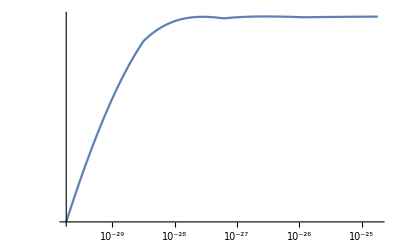

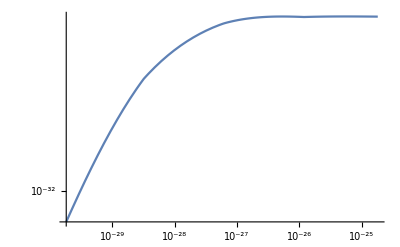

```mathematica
Print["Show the same plots as above, but with only one oscillator each to show the profile"]
LogLogPlot[(FeλeDictOscillators[[1]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
LogLogPlot[(FeλeDictOscillators[[5]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[5]][["fitparams"]][[1]]),{mχ,2"m"/.SIConstRepl,2 10^5"m"/.SIConstRepl}]
```

```mathematica
Print["Extend the range of masses"]
Show[Table[LogLogPlot[(FeλeDictOscillators[[i]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[i]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotRange->{10^-42,10^-27},PlotLabels->ToString[StringForm["``",i]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}],{i,Length[FeλeDictOscillators]}]]
Print["Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at"]
"ωedgei"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
Print["And also the number densities"]
"ne"/.Table[FeλeDictOscillators[[i]][["fitparams"]][[1]],{i,Length[FeλeDictOscillators]}]
```

Extend the range of masses

-Graphics-

Why are some of the oscillators being truncated at the same value of the mass? I would have guessed it would be the energy truncation we did, but because oscillator 4 is untruncated, this seems unlikely. So lets look at the values ω_(edge, i) where they were truncated at

{6.04519×10^14,6.5887×10^12,3.02977×10^14,1.51848×10^14,1.09042×10^18,1.09893×10^19}

And also the number densities

{1.038×10^29,1.91532×10^29,4.34359×10^29,3.17873×10^30,4.14995×10^32,4.0004×10^34}

```mathematica
LogLogPlot[(FeλeDictOscillators[[3]][["f"]][Log10[mχ],Log10[10^5]])/("ne"/.FeλeDictOscillators[[3]][["fitparams"]][[1]]),{mχ,10^-32.3, 10^-23.4},PlotLabels->ToString[StringForm["``",3]],PlotLabel->"Fe σ Per Oscillator - vχ = 10^-3 c",AxesLabel->{"mχ [kg]","[m^2]"}]
```

-Graphics-

#### Recoil Energy Sampling

```mathematica
FeλeDictOscillators[[1]][["fitparams"]][[1]]
```

{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→2.49694×10^20,βcore→1.32379×10^19,SiO2Frac→0.447,MgOFrac→0.387|>

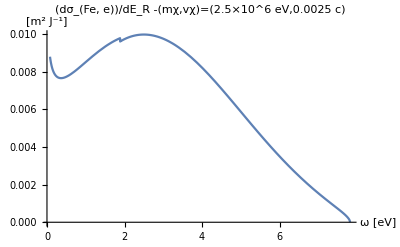

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore],{ω,10^-2 ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

Now include the truncation due to the cutoff of available data

1.18632×10^16

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000310856}. NIntegrate obtained 0.0000421186 and 6.94605×10^-7 for the integral and error estimates.

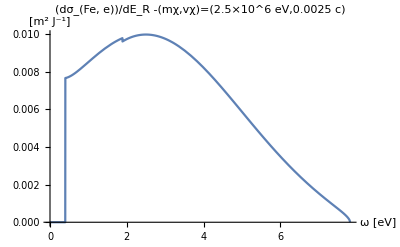

Notice that this is a cutoff sub eV

```mathematica
Print["Now include the truncation due to the cutoff of available data"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[1]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[1]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice that this is a cutoff sub eV"]
```

Lets look at the outermost shell

1.18632×10^16

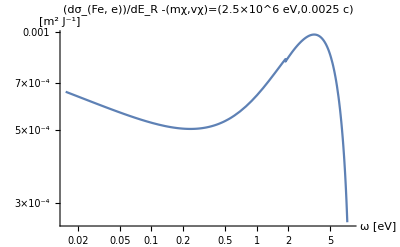

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00010936}. NIntegrate obtained 4.91141×10^-6 and 1.73417×10^-7 for the integral and error estimates.

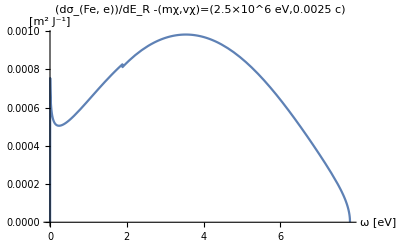

Notice this has a much lower cutoff

```mathematica
Print["Lets look at the outermost shell"]
Block[{mχtemp,vχtemp,ERmaxtemp},
mχtemp = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχtemp = 2.5 10^-3 "c"/.SIConstRepl;
ERmaxtemp = 1/(2"ℏ")mχtemp vχtemp^2/.SIConstRepl;
Print[ERmaxtemp];
Print[LogLogPlot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Print[Plot[dσdERe[ω(("JpereV")/("ℏ"))/.SIConstRepl,mχtemp,vχtemp,FeλeDictOscillators[[2]][["fitparams"]],βcore]HeavisideTheta[(("JpereV")/("ℏ"))ω-"ωedgei"/.FeλeDictOscillators[[2]][["fitparams"]][[1]]],{ω,0ERmaxtemp (("JpereV")/("ℏ"))^-1/.SIConstRepl,ERmaxtemp(("JpereV")/("ℏ"))^-1/.SIConstRepl},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]]
]
Print["Notice this has a much lower cutoff"]
```

```mathematica
Testdσfunc[["dσTable"]][[;;,1]](("JpereV")/("ℏ"))^-1/.SIConstRepl
```

{0.004339,0.00620024,0.00885988,0.0126604,0.0180911,0.0258515,0.0369406,0.0527865,0.0754297,0.107786,0.154021,0.22009,0.314498,0.449405,0.64218,0.917647,1.31128,1.87376,2.67752,3.82606}

To interpolate, we need to determine the range over which to interpolate, and then evaluate the function at the points in a list, then interpolate

For the range: we want to evaluate from ω_(edge,i), then have some set number of evaluations, then we can do the interpolation

we also want to do this for each oscillator.

```mathematica
Testdσfunc=Block[{mχ,vχ,params,ERmin,ERmax,InterPω,n=20,InterdσTable,Interdσf},
(*Input parameters*)
mχ = 2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl;
vχ = 2.5 10^-3 "c"/.SIConstRepl;
params = FeλeDictOscillators[[2]][["fitparams"]][[1]];

(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];

Print[dσdERe[ERmax,mχ,vχ,{params},"β"/.params]];
Print[ERmax];
Print[InterPω[[n+1]]];
Print[ERmax==InterPω[[n+1]]];
Print[dσdERe[N[InterPω[[n+1]](1-10^-3)],mχ,vχ,{params},"β"/.params]];

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-10^-3),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]
```

0.

1.18632×10^16

1.18632×10^16

True

0.0000287166

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003463745696036182202849629252483509844751097261905670166015625}. NIntegrate obtained 0.000113854 and 6.1034×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000763026},{9.58451×10^12,0.000730472},{1.39425×10^13,0.000698427},{2.0282×10^13,0.000667086},{2.95039×10^13,0.000636717},{4.2919×10^13,0.000607674},{6.24338×10^13,0.000580439},{9.08217×10^13,0.00055567},{1.32117×10^14,0.000534269},{1.9219×10^14,0.000517488},{2.79576×10^14,0.000507088},{4.06696×10^14,0.000505583},{5.91616×10^14,0.000516596},{8.60617×10^14,0.000545281},{1.25193×10^15,0.000598449},{1.82117×10^15,0.000683001},{2.64923×10^15,0.00079926},{3.85381×10^15,0.000919998},{5.60609×10^15,0.000980598},{8.15511×10^15,0.000787263},{1.18632×10^16,0.0000287166}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
(*InterpolatedσdERe[mχ_,vχ_,params_]:=Module[{ERmin,ERmax,InterPω,ϵ,n=20,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)
(*local parameters*)
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];
ϵ=10^-10;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)

InterdσTable=Table[{InterPω[[i]],dσdERe[InterPω[[i]](1-ϵ),mχ,vχ,{params},"β"/.params]HeavisideTheta[InterPω[[i]]-ERmin]},{i,n+1}];
Interdσf=Interpolation[InterdσTable];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->InterPω|>
]*)
```

```mathematica
InterpolatedσdERe2 =InterpolatedσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl, FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002782473013753506880271597345721801275431062094867229461669921875}. NIntegrate obtained 0.000113954 and 6.13129×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000602666718839405825790256354679286232567392289638519287109375}. NIntegrate obtained 0.000158367 and 1.4707×10^-9 for the integral and error estimates.

<|dσf→InterpolatingFunction[…],dσTable→{{6.5887×10^12,0.000762938},{9.58451×10^12,0.000730402},{1.39425×10^13,0.000698342},{2.0282×10^13,0.000667004},{2.95039×10^13,0.000636637},{4.2919×10^13,0.000607598},{6.24338×10^13,0.000580369},{9.08217×10^13,0.000555607},{1.32117×10^14,0.000534217},{1.9219×10^14,0.000517451},{2.79576×10^14,0.000507071},{4.06696×10^14,0.000505594},{5.91616×10^14,0.000516646},{8.60617×10^14,0.000545387},{1.25193×10^15,0.00059863},{1.82117×10^15,0.000683272},{2.64923×10^15,0.000799601},{3.85381×10^15,0.000920314},{5.60609×10^15,0.000980529},{8.15511×10^15,0.000786165},{1.18632×10^16,9.05968×10^-9}},Interpoints→{6.5887×10^12,9.58451×10^12,1.39425×10^13,2.0282×10^13,2.95039×10^13,4.2919×10^13,6.24338×10^13,9.08217×10^13,1.32117×10^14,1.9219×10^14,2.79576×10^14,4.06696×10^14,5.91616×10^14,8.60617×10^14,1.25193×10^15,1.82117×10^15,2.64923×10^15,3.85381×10^15,5.60609×10^15,8.15511×10^15,1.18632×10^16}|>

```mathematica
Print["Show the Block which we've tested, and the module we have written give the same expression"]
Plot[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
Plot[InterpolatedσdERe2 [["dσf"]][ω],{ω,InterpolatedσdERe2 [["Interpoints"]][[1]],InterpolatedσdERe2 [["Interpoints"]][[-1]]}]
```

Show the Block which we've tested, and the module we have written give the same expression

-Graphics-

-Graphics-

```mathematica
NIntegrate[Testdσfunc[["dσf"]][ω],{ω,Testdσfunc[["Interpoints"]][[1]],Testdσfunc[["Interpoints"]][[-1]]}]
```

8.37856×10^12

#### Interpolate over vχ as well as ω

```mathematica
GetvχandωList[mχ_,vχ_,params_,n_:20]:=Module[{ERmin,ERmax,ϵ,Interpointsω},
ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;

Interpointsω=10^Subdivide[Log10[ERmin],Log10[ERmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
GetvχandωList[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,2.5 10^-3 "c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]]]
```

{{750000.,6.5887×10^12},{750000.,9.58451×10^12},{750000.,1.39425×10^13},{750000.,2.0282×10^13},{750000.,2.95039×10^13},{750000.,4.2919×10^13},{750000.,6.24338×10^13},{750000.,9.08217×10^13},{750000.,1.32117×10^14},{750000.,1.9219×10^14},{750000.,2.79576×10^14},{750000.,4.06696×10^14},{750000.,5.91616×10^14},{750000.,8.60617×10^14},{750000.,1.25193×10^15},{750000.,1.82117×10^15},{750000.,2.64923×10^15},{750000.,3.85381×10^15},{750000.,5.60609×10^15},{750000.,8.15511×10^15}}

```mathematica
InterpolatvχandωσdERe[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandω=SortBy[Table[GetvχandωList[mχ,Interpointsvχ[[i]],params,n],{i,m+1}],Last];
ϵ=10^-4;(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolate=InterpolatvχandωσdERe[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000125028}. NIntegrate obtained 0.000128098 and 1.87966×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00023053}. NIntegrate obtained 0.000210627 and 6.68139×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00019964873741304990040971827081062173192549380473792552947998046875}. NIntegrate obtained 0.000331927 and 4.00527×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,6.94665×10^12},0.125043},{{30000,7.32406×10^12},0.121248},{{30000,7.72196×10^12},0.117387},{{30000,8.14149×10^12},0.113453},{{30000,8.5838×10^12},0.109437},{{30000,9.05015×10^12},0.10533},{{30000,9.54183×10^12},0.101119},{{30000,1.00602×10^13},0.0967902},{{30000,1.06068×10^13},0.0923255},{{30000,1.1183×10^13},0.0877034},{{30000,1.17906×10^13},0.0828965},{{30000,1.24312×10^13},0.0778694},{{30000,1.31065×10^13},0.0725748},{{30000,1.38186×10^13},0.066948},{{30000,1.45693×10^13},0.060895},{{30000,1.53609×10^13},0.0542717},{{30000,1.61954×10^13},0.0468342},{{30000,1.70753×10^13},0.0381056},{{30000,1.8003×10^13},0.0268509},{{30000,1.8981×10^13},1.16337×10^-6}},{{{300000,6.5887×10^12},0.00414931},{{300000,8.74532×10^12},0.00399408},{{300000,1.16078×10^13},0.00384017},{{300000,1.54073×10^13},0.00368792},{{300000,2.04505×10^13},0.00353772},{{300000,2.71444×10^13},0.00339007},{{300000,3.60293×10^13},0.00324558},{{300000,4.78225×10^13},0.00310498},{{300000,6.34758×10^13},0.00296914},{{300000,8.42527×10^13},0.00283909},{{300000,1.1183×10^14},0.00271602},{{300000,1.48435×10^14},0.00260126},{{300000,1.97021×10^14},0.00249623},{{300000,2.6151×10^14},0.00240224},{{300000,3.47107×10^14},0.00232005},{{300000,4.60723×10^14},0.00224882},{{300000,6.11528×10^14},0.00218355},{{300000,8.11693×10^14},0.00210868},{{300000,1.07738×10^15},0.00198043},{{300000,1.43003×10^15},0.00166523},{{300000,1.8981×10^15},3.83751×10^-8}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000529074},{{3000000,1.83972×10^13},0.0000501535},{{3000000,3.07417×10^13},0.0000476051},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},2.65079×10^-14}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,7.79427×10^12},0.0269579},{{30000 √10,9.22044×10^12},0.0260032},{{30000 √10,1.09076×10^13},0.0250463},{{30000 √10,1.29034×10^13},0.0240866},{{30000 √10,1.52644×10^13},0.0231232},{{30000 √10,1.80574×10^13},0.0221549},{{30000 √10,2.13615×10^13},0.0211802},{{30000 √10,2.52702×10^13},0.0201969},{{30000 √10,2.9894×10^13},0.0192024},{{30000 √10,3.53639×10^13},0.018193},{{30000 √10,4.18346×10^13},0.0171637},{{30000 √10,4.94894×10^13},0.0161076},{{30000 √10,5.85447×10^13},0.0150151},{{30000 √10,6.9257×10^13},0.0138721},{{30000 √10,8.19294×10^13},0.0126577},{{30000 √10,9.69206×10^13},0.0113384},{{30000 √10,1.14655×10^14},0.00985722},{{30000 √10,1.35634×10^14},0.00810197},{{30000 √10,1.60452×10^14},0.00578626},{{30000 √10,1.8981×10^14},1.43132×10^-7}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,9.81241×10^12},0.000468611},{{300000 √10,1.46134×10^13},0.000447422},{{300000 √10,2.17635×10^13},0.000426766},{{300000 √10,3.24118×10^13},0.000406875},{{300000 √10,4.82703×10^13},0.00038805},{{300000 √10,7.18879×10^13},0.000370713},{{300000 √10,1.07061×10^14},0.00035546},{{300000 √10,1.59444×10^14},0.000343132},{{300000 √10,2.37456×10^14},0.000334941},{{300000 √10,3.53639×10^14},0.000332674},{{300000 √10,5.26667×10^14},0.000339008},{{300000 √10,7.84354×10^14},0.000358055},{{300000 √10,1.16812×10^15},0.000395656},{{300000 √10,1.73966×10^15},0.000459763},{{300000 √10,2.59084×10^15},0.000556967},{{300000 √10,3.85848×10^15},0.000680416},{{300000 √10,5.74635×10^15},0.00080825},{{300000 √10,8.55792×10^15},0.000829791},{{300000 √10,1.27451×10^16},0.000502176},{{300000 √10,1.8981×10^16},2.26382×10^-9}}},Interpoints→{{{30000,6.5887×10^12},{30000,6.94665×10^12},{30000,7.32406×10^12},{30000,7.72196×10^12},{30000,8.14149×10^12},{30000,8.5838×10^12},{30000,9.05015×10^12},{30000,9.54183×10^12},{30000,1.00602×10^13},{30000,1.06068×10^13},{30000,1.1183×10^13},{30000,1.17906×10^13},{30000,1.24312×10^13},{30000,1.31065×10^13},{30000,1.38186×10^13},{30000,1.45693×10^13},{30000,1.53609×10^13},{30000,1.61954×10^13},{30000,1.70753×10^13},{30000,1.8003×10^13},{30000,1.8981×10^13}},{{300000,6.5887×10^12},{300000,8.74532×10^12},{300000,1.16078×10^13},{300000,1.54073×10^13},{300000,2.04505×10^13},{300000,2.71444×10^13},{300000,3.60293×10^13},{300000,4.78225×10^13},{300000,6.34758×10^13},{300000,8.42527×10^13},{300000,1.1183×10^14},{300000,1.48435×10^14},{300000,1.97021×10^14},{300000,2.6151×10^14},{300000,3.47107×10^14},{300000,4.60723×10^14},{300000,6.11528×10^14},{300000,8.11693×10^14},{300000,1.07738×10^15},{300000,1.43003×10^15},{300000,1.8981×10^15}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,7.79427×10^12},{30000 √10,9.22044×10^12},{30000 √10,1.09076×10^13},{30000 √10,1.29034×10^13},{30000 √10,1.52644×10^13},{30000 √10,1.80574×10^13},{30000 √10,2.13615×10^13},{30000 √10,2.52702×10^13},{30000 √10,2.9894×10^13},{30000 √10,3.53639×10^13},{30000 √10,4.18346×10^13},{30000 √10,4.94894×10^13},{30000 √10,5.85447×10^13},{30000 √10,6.9257×10^13},{30000 √10,8.19294×10^13},{30000 √10,9.69206×10^13},{30000 √10,1.14655×10^14},{30000 √10,1.35634×10^14},{30000 √10,1.60452×10^14},{30000 √10,1.8981×10^14}},{{300000 √10,6.5887×10^12},{300000 √10,9.81241×10^12},{300000 √10,1.46134×10^13},{300000 √10,2.17635×10^13},{300000 √10,3.24118×10^13},{300000 √10,4.82703×10^13},{300000 √10,7.18879×10^13},{300000 √10,1.07061×10^14},{300000 √10,1.59444×10^14},{300000 √10,2.37456×10^14},{300000 √10,3.53639×10^14},{300000 √10,5.26667×10^14},{300000 √10,7.84354×10^14},{300000 √10,1.16812×10^15},{300000 √10,1.73966×10^15},{300000 √10,2.59084×10^15},{300000 √10,3.85848×10^15},{300000 √10,5.74635×10^15},{300000 √10,8.55792×10^15},{300000 √10,1.27451×10^16},{300000 √10,1.8981×10^16}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

```mathematica
testkinσinterpolate[["dσf"]][5,13]
```

Missing[KeyAbsent,5]

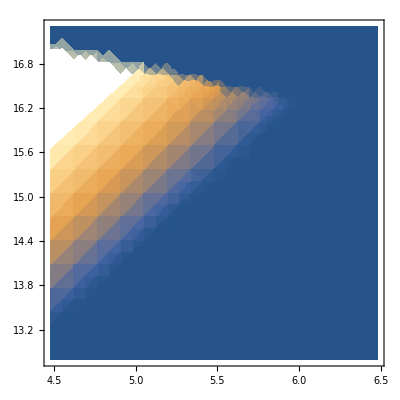

```mathematica
DensityPlot[testkinσinterpolate[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

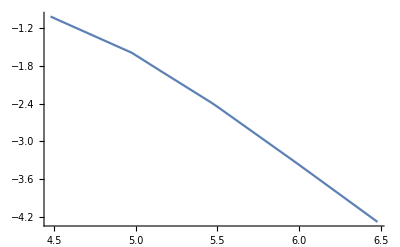

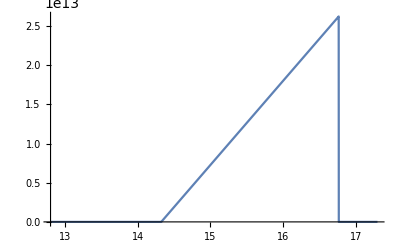

Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside

```mathematica
Plot[testkinσinterpolate[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolate[["dσf"]][5,ω],{ω,12.8,17.3}]
Print["Because the grid of ω and vχ is unstructured, we get a simple linear fit. Try taking the max ωmax in the grid and just cutting off with a heaviside"]
```

#### Try interpolating over vχ and ω, but with a square grid

```mathematica
GetvχandωListSquare[mχ_,vχ_,ωmax_,params_,n_:20]:=Module[{ωmin,ϵ,Interpointsω},
ωmin= "ωedgei"/.params;
(*ERmax = ωmax;*)

Interpointsω=10^Subdivide[Log10[ωmin],Log10[ωmax],n];
Table[{vχ,Interpointsω[[i]]},{i,n+1}]
]
```

```mathematica
InterpolatvχandωσdEReSquare[mχ_,vχ_:{10^-5,10^-2}"c"/.SIConstRepl,params_,m_:4,n_:20]:=Module[{ωmin,ωmax,Interpointsvχ,Interpointsvχandω,ϵ,InterdσTable,Interdσf},
(*Interpolate over dσdER for electronic contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

(*local parameters*)
(*ERmin= "ωedgei"/.params;
ERmax = 1/(2"ℏ")mχ vχ^2/.params;
InterPω=  10^Subdivide[Log10[ERmin],Log10[ERmax],n];*)
ωmin= "ωedgei"/.params;
ωmax =  1/(2"ℏ")mχ vχ[[2]]^2/.params;
Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Print[GetvχandωListSquare[mχ,Interpointsvχ[[1]],ωmax,params,n]];
Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];
(*Interpointsvχandω=Table[GetvχandωListSquare[mχ,Interpointsvχ[[i]],ωmax,params,n],{i,m+1}];*)
(*Subdivide takes us slightly over ERmax, which throws errors. So subtract off a small fraction ϵ of ER max*)
(*Print[Interpointsvχandω[[1,1]][[1]]];
Print[Interpointsvχandω[[1,1]][[2]]];*)
(*Print[dσdERe[6.588699526066354*^12(1+ϵ),mχ,3000(1+ϵ),{params},"β"/.params]];
Print[dσdERe[Interpointsvχandω[[1,1]][[2]](1+ϵ),mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]];*)
Print[dσdERe[Interpointsvχandω[[1,1]][[2]],mχ,Interpointsvχandω[[1,1]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[1,1]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[1,1]][[1]])^2/.params)-Interpointsvχandω[[1,1]][[2]]]];
InterdσTable=Table[{Interpointsvχandω[[i,j]],dσdERe[Interpointsvχandω[[i,j]][[2]],mχ,Interpointsvχandω[[i,j]][[1]],{params},"β"/.params]HeavisideTheta[Interpointsvχandω[[i,j]][[2]]-ωmin]HeavisideTheta[( mχ/(2"ℏ")(Interpointsvχandω[[i,j]][[1]])^2/.params)-Interpointsvχandω[[i,j]][[2]]]},{i,m+1},{j,n+1}];
Print[Flatten[InterdσTable,1]];
Interdσf=Interpolation[Flatten[InterdσTable,1]];
<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandω,"Interpointsvχ"->Interpointsvχ|>
]
```

```mathematica
testkinσinterpolateSquare=InterpolatvχandωσdEReSquare[2.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],4,20]
```

{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}}

0.128779

NIntegrate::inumr: The integrand -(0.0699144 Im[1/ϵMNum[0.000834741/(EnergyLoss`Private`z),EnergyLoss`Private`z,(«20»)/(«20»),{«1»}]])/(EnergyLoss`Private`z) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0354795-0.0279276 ⅈ,0.0354795+0. ⅈ}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.00032159492022796235086330718377922721629147417843341827392578125}. NIntegrate obtained 0.000117156 and 2.2645×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003657868553803155195242209629657992309148539789021015167236328125}. NIntegrate obtained 0.000184102 and 1.80922×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1.12196132850382213064222014509141445159912109375-0.54156685354676916268642291229238270738745584159086009742098706683 ⅈ}. NIntegrate obtained -0.000636687+0.00105807 ⅈ and 1.24195×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.},{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.},{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.},{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ},{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}

<|dσf→InterpolatingFunction[…],dσTable→{{{{30000,6.5887×10^12},0.128779},{{30000,1.10097×10^13},0.0890861},{{30000,1.83972×10^13},0.0206049},{{30000,3.07417×10^13},0.},{{30000,5.13693×10^13},0.},{{30000,8.5838×10^13},0.},{{30000,1.43435×10^14},0.},{{30000,2.3968×10^14},0.},{{30000,4.00505×10^14},0.},{{30000,6.69243×10^14},0.},{{30000,1.1183×10^15},0.},{{30000,1.86868×10^15},0.},{{30000,3.12257×10^15},0.},{{30000,5.21781×10^15},0.},{{30000,8.71895×10^15},0.},{{30000,1.45693×10^16},0.},{{30000,2.43453×10^16},0.},{{30000,4.0681×10^16},0.},{{30000,6.79779×10^16},0.},{{30000,1.13591×10^17},0.},{{30000,1.8981×10^17},0.}},{{{30000 √10,6.5887×10^12},0.0279111},{{30000 √10,1.10097×10^13},0.0249931},{{30000 √10,1.83972×10^13},0.0220471},{{30000 √10,3.07417×10^13},0.0190356},{{30000 √10,5.13693×10^13},0.0158688},{{30000 √10,8.5838×10^13},0.0123041},{{30000 √10,1.43435×10^14},0.00741879},{{30000 √10,2.3968×10^14},0.},{{30000 √10,4.00505×10^14},0.},{{30000 √10,6.69243×10^14},0.},{{30000 √10,1.1183×10^15},0.},{{30000 √10,1.86868×10^15},0.},{{30000 √10,3.12257×10^15},0.},{{30000 √10,5.21781×10^15},0.},{{30000 √10,8.71895×10^15},0.},{{30000 √10,1.45693×10^16},0.},{{30000 √10,2.43453×10^16},0.},{{30000 √10,4.0681×10^16},0.},{{30000 √10,6.79779×10^16},0.},{{30000 √10,1.13591×10^17},0.},{{30000 √10,1.8981×10^17},0.}},{{{300000,6.5887×10^12},0.00414931},{{300000,1.10097×10^13},0.00386881},{{300000,1.83972×10^13},0.00359357},{{300000,3.07417×10^13},0.00332614},{{300000,5.13693×10^13},0.00307017},{{300000,8.5838×10^13},0.00283076},{{300000,1.43435×10^14},0.00261466},{{300000,2.3968×10^14},0.00242994},{{300000,4.00505×10^14},0.00228286},{{300000,6.69243×10^14},0.002162},{{300000,1.1183×10^15},0.00195456},{{300000,1.86868×10^15},0.000473946},{{300000,3.12257×10^15},0.},{{300000,5.21781×10^15},0.},{{300000,8.71895×10^15},0.},{{300000,1.45693×10^16},0.},{{300000,2.43453×10^16},0.},{{300000,4.0681×10^16},0.},{{300000,6.79779×10^16},0.},{{300000,1.13591×10^17},0.},{{300000,1.8981×10^17},0.}},{{{300000 √10,6.5887×10^12},0.000490234},{{300000 √10,1.10097×10^13},0.000462445},{{300000 √10,1.83972×10^13},0.000435401},{{300000 √10,3.07417×10^13},0.000409463},{{300000 √10,5.13693×10^13},0.00038523},{{300000 √10,8.5838×10^13},0.000363621},{{300000 √10,1.43435×10^14},0.000346061},{{300000 √10,2.3968×10^14},0.000334812},{{300000 √10,4.00505×10^14},0.000333572},{{300000 √10,6.69243×10^14},0.000348584},{{300000 √10,1.1183×10^15},0.000390397},{{300000 √10,1.86868×10^15},0.000474681},{{300000 √10,3.12257×10^15},0.000605796},{{300000 √10,5.21781×10^15},0.000781326},{{300000 √10,8.71895×10^15},0.000824436},{{300000 √10,1.45693×10^16},0.000319572},{{300000 √10,2.43453×10^16},0.+0. ⅈ},{{300000 √10,4.0681×10^16},0.+0. ⅈ},{{300000 √10,6.79779×10^16},0.+0. ⅈ},{{300000 √10,1.13591×10^17},0.+0. ⅈ},{{300000 √10,1.8981×10^17},0.+0. ⅈ}},{{{3000000,6.5887×10^12},0.0000536022},{{3000000,1.10097×10^13},0.0000530238},{{3000000,1.83972×10^13},0.0000501318},{{3000000,3.07417×10^13},0.0000476047},{{3000000,5.13693×10^13},0.0000452776},{{3000000,8.5838×10^13},0.0000432816},{{3000000,1.43435×10^14},0.0000418077},{{3000000,2.3968×10^14},0.0000411727},{{3000000,4.00505×10^14},0.00004192},{{3000000,6.69243×10^14},0.0000450281},{{3000000,1.1183×10^15},0.0000523279},{{3000000,1.86868×10^15},0.0000672103},{{3000000,3.12257×10^15},0.0000942808},{{3000000,5.21781×10^15},0.0001489},{{3000000,8.71895×10^15},0.000289498},{{3000000,1.45693×10^16},0.000555831},{{3000000,2.43453×10^16},0.000104805},{{3000000,4.0681×10^16},0.0000262153},{{3000000,6.79779×10^16},8.02963×10^-6},{{3000000,1.13591×10^17},2.59059×10^-6},{{3000000,1.8981×10^17},0.+0. ⅈ}}},Interpoints→{{{30000,6.5887×10^12},{30000,1.10097×10^13},{30000,1.83972×10^13},{30000,3.07417×10^13},{30000,5.13693×10^13},{30000,8.5838×10^13},{30000,1.43435×10^14},{30000,2.3968×10^14},{30000,4.00505×10^14},{30000,6.69243×10^14},{30000,1.1183×10^15},{30000,1.86868×10^15},{30000,3.12257×10^15},{30000,5.21781×10^15},{30000,8.71895×10^15},{30000,1.45693×10^16},{30000,2.43453×10^16},{30000,4.0681×10^16},{30000,6.79779×10^16},{30000,1.13591×10^17},{30000,1.8981×10^17}},{{30000 √10,6.5887×10^12},{30000 √10,1.10097×10^13},{30000 √10,1.83972×10^13},{30000 √10,3.07417×10^13},{30000 √10,5.13693×10^13},{30000 √10,8.5838×10^13},{30000 √10,1.43435×10^14},{30000 √10,2.3968×10^14},{30000 √10,4.00505×10^14},{30000 √10,6.69243×10^14},{30000 √10,1.1183×10^15},{30000 √10,1.86868×10^15},{30000 √10,3.12257×10^15},{30000 √10,5.21781×10^15},{30000 √10,8.71895×10^15},{30000 √10,1.45693×10^16},{30000 √10,2.43453×10^16},{30000 √10,4.0681×10^16},{30000 √10,6.79779×10^16},{30000 √10,1.13591×10^17},{30000 √10,1.8981×10^17}},{{300000,6.5887×10^12},{300000,1.10097×10^13},{300000,1.83972×10^13},{300000,3.07417×10^13},{300000,5.13693×10^13},{300000,8.5838×10^13},{300000,1.43435×10^14},{300000,2.3968×10^14},{300000,4.00505×10^14},{300000,6.69243×10^14},{300000,1.1183×10^15},{300000,1.86868×10^15},{300000,3.12257×10^15},{300000,5.21781×10^15},{300000,8.71895×10^15},{300000,1.45693×10^16},{300000,2.43453×10^16},{300000,4.0681×10^16},{300000,6.79779×10^16},{300000,1.13591×10^17},{300000,1.8981×10^17}},{{300000 √10,6.5887×10^12},{300000 √10,1.10097×10^13},{300000 √10,1.83972×10^13},{300000 √10,3.07417×10^13},{300000 √10,5.13693×10^13},{300000 √10,8.5838×10^13},{300000 √10,1.43435×10^14},{300000 √10,2.3968×10^14},{300000 √10,4.00505×10^14},{300000 √10,6.69243×10^14},{300000 √10,1.1183×10^15},{300000 √10,1.86868×10^15},{300000 √10,3.12257×10^15},{300000 √10,5.21781×10^15},{300000 √10,8.71895×10^15},{300000 √10,1.45693×10^16},{300000 √10,2.43453×10^16},{300000 √10,4.0681×10^16},{300000 √10,6.79779×10^16},{300000 √10,1.13591×10^17},{300000 √10,1.8981×10^17}},{{3000000,6.5887×10^12},{3000000,1.10097×10^13},{3000000,1.83972×10^13},{3000000,3.07417×10^13},{3000000,5.13693×10^13},{3000000,8.5838×10^13},{3000000,1.43435×10^14},{3000000,2.3968×10^14},{3000000,4.00505×10^14},{3000000,6.69243×10^14},{3000000,1.1183×10^15},{3000000,1.86868×10^15},{3000000,3.12257×10^15},{3000000,5.21781×10^15},{3000000,8.71895×10^15},{3000000,1.45693×10^16},{3000000,2.43453×10^16},{3000000,4.0681×10^16},{3000000,6.79779×10^16},{3000000,1.13591×10^17},{3000000,1.8981×10^17}}},Interpointsvχ→{30000,30000 √10,300000,300000 √10,3000000}|>

InterpolatingFunction::dmval: Input value {4.48014,12.8003} lies outside the range of data in the interpolating function. Extrapolation will be used.

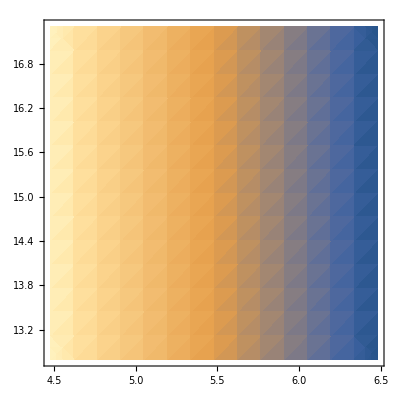

```mathematica
DensityPlot[testkinσinterpolateSquare[["dσf"]][vχ,ω],{vχ,4.48,6.48},{ω,12.8,17.3}]
```

InterpolatingFunction::dmval: Input value {4.48004,13} lies outside the range of data in the interpolating function. Extrapolation will be used.

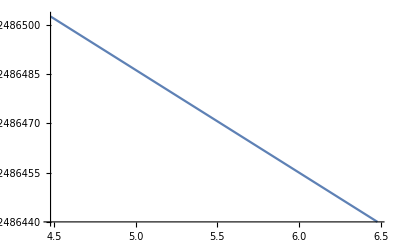

InterpolatingFunction::dmval: Input value {5,13.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

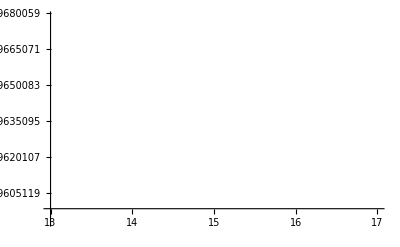

```mathematica
Plot[testkinσinterpolateSquare[["dσf"]][vχ,13],{vχ,4.48,6.48}]
Plot[testkinσinterpolateSquare[["dσf"]][5,ω],{ω,13,17}]
```

#### Interpolate with vχ and ξ

Psuedo-code:

We want to use ξ ∈ [0,1) with ω(ξ) = ω_min+ξ(ω_max-ω_min)
This should eleviate both issues we were having before, it interpolates only over the region of integration (so we get variation with ω and no issues with Heavisides) and also is a square grid (so no reduced order interpolations)

```mathematica
testkinσinterpolateξmeosc2higherres=InterpolatevχandωσdEReξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-4,10^-2}"c"/.SIConstRepl,FeλeDictOscillators[[2]][["fitparams"]][[1]],5,60,10^-4,4];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000122581875730450894405008932519507425240590237081050872802734375}. NIntegrate obtained 0.00020251 and 3.43551×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0002551760996913700316776445198296840999319101683795452117919921875}. NIntegrate obtained 0.00010951 and 2.80601×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0001781783644222577315413026666224283189876587130129337310791015625}. NIntegrate obtained 0.000139236 and 7.39518×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

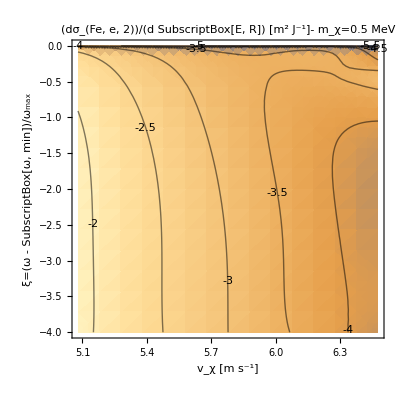

Compare to the above plot, checking the ω scale

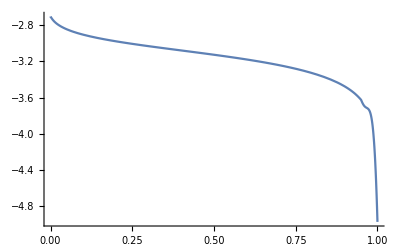

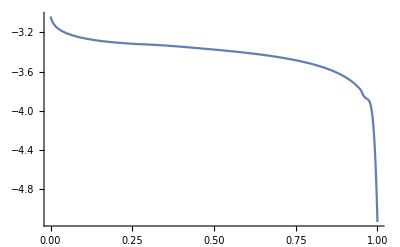

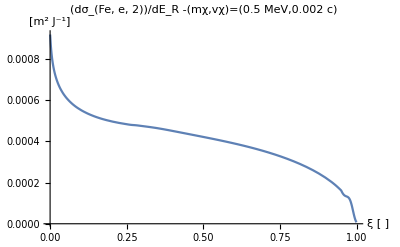

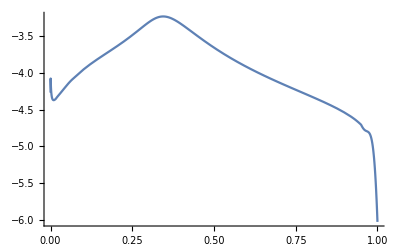

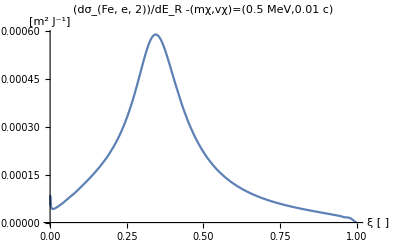

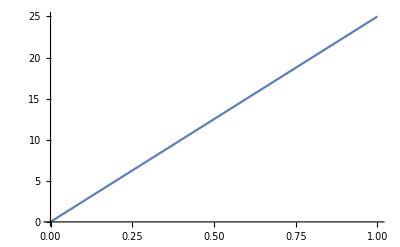

```mathematica
vχbounds=testkinσinterpolateξmeosc2higherres[["vχ"]];
ξbounds=testkinσinterpolateξmeosc2higherres[["ξ"]];
Show[{DensityPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
Print["Compare to the above plot, checking the ω scale"]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.6,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][5.8,Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.002 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All]
Plot[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχbounds[[2]],Log10[ξ]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotRange->All,PlotLabel->"(dσ_(Fe, e, 2))/dE_R -(mχ,vχ)=(0.5 MeV,0.01 c)",AxesLabel->{"ξ [ ]","[m^2 J^-1]"}]
Plot[(("ℏ")/("JpereV")/.SIConstRepl)ωofξandvχ[ξ,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
(*Plot[(("ℏ")/("JpereV")/.SIConstRepl)ξofωandvχ[ω,testkinσinterpolateξmeosc2higherres[["ωmin"]],10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]],{ω,10^ξbounds[[1]],10^ξbounds[[2]]}]*)
```

```mathematica
("JpereV"/.SIConstRepl)
```

1.602×10^-19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000141826}. NIntegrate obtained 0.000132359 and 2.63987×10^-6 for the integral and error estimates.

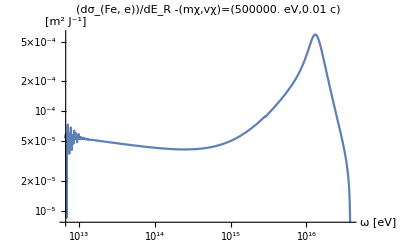

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000149062}. NIntegrate obtained 0.000143482 and 1.97166×10^-6 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^testkinσinterpolateξmeosc2higherres[["vχ"]][[2]];
ERmaxtemp = ωmaxofvχ[10^vχbounds[[2]],testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.000334144122406762993635932768032859030427061952650547027587890625}. NIntegrate obtained 0.000097441 and 1.80677×10^-9 for the integral and error estimates.

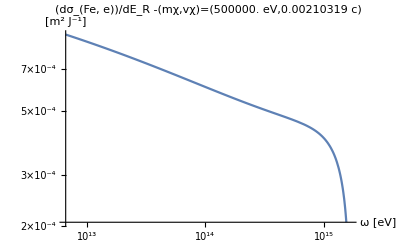

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.0003356319043151438107400706678529189730397774837911128997802734375}. NIntegrate obtained 0.0000978685 and 2.73029×10^-9 for the integral and error estimates.

-Graphics-

```mathematica
Block[{mχtemp,vχtemp,ERmaxtemp,ERmintemp},
mχtemp = testkinσinterpolateξmeosc2higherres[["mχ"]];
vχtemp = 10^(5.8);
ERmaxtemp = ωmaxofvχ[vχtemp,testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]];
ERmintemp = testkinσinterpolateξmeosc2higherres[["ωmin"]];
Print[LogLogPlot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]];
Plot[dσdERe[ω,mχtemp,vχtemp,{testkinσinterpolateξmeosc2higherres[["params"]]},"β"/.testkinσinterpolateξmeosc2higherres[["params"]]],{ω,ERmintemp ,ERmaxtemp},PlotLabel->StringForm["(dσ_(Fe, e))/dE_R -(mχ,vχ)=(`` eV,`` c)",mχtemp(("JpereV")/("c")^2)^-1/.SIConstRepl,N[vχtemp("c")^-1/.SIConstRepl]],AxesLabel->{"ω [eV]","[m^2 J^-1]"}]
]
```

#### Recoil Energy Probability

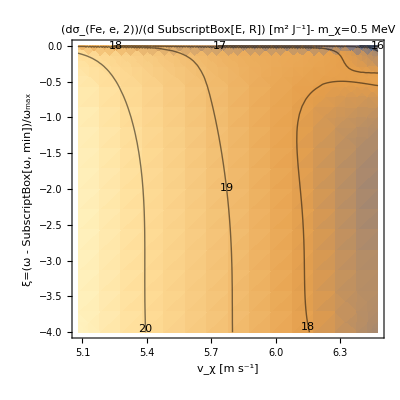

```mathematica
Show[{DensityPlot[Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},PlotLabel->"(dσ_(Fe, e, 2))/(d SubscriptBox[E, R]) [m^2 J^-1]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,ξbounds[[1]],ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

This looks like it is missing a factor of ℏ

```mathematica
(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])/.vχ->0.9vχbounds[[2]]
NIntegrate[%,{ξ,0,1}]
% "ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]
%(ωmaxofvχ[10^(0.9vχbounds[[2]]),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])
Print["This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ"]
```

1.91532×10^29 10^(-7.27767+InterpolatingFunction[…][5.82941,ξ])

5.93707×10^14

6.26361×10^-20

0.000120022

This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ

```mathematica
(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,ξ])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])/.vχ->vχbounds[[1]]
% "ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]
%(ωmaxofvχ[10^(vχbounds[[1]]),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])
NIntegrate[%,{ξ,0,1}]
Print["This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ"]
vχbounds[[1]]
```

1.91532×10^29 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

0.0000202066 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

1.0942×10^9 10^(-6.81987+InterpolatingFunction[…][Log[120000]/Log[10],ξ])

0.0000934931

This makes sense, the multiplication by ℏ (ω_max-ω_min) is from the change of variables in the integral from E_R->ω->ξ. This tells us that over the course of the mean interaction length, the probability that the particle loose all it's kinetic energy is about once in 10^4. Notice also that this is independent of κ

Log[120000]/Log[10]

2.2191×10^-18 10^(-7.7942+InterpolatingFunction[…][6.34898,Log[ξ]/Log[10]])

7.98093×10^-30

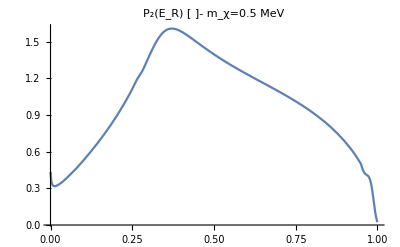

1.

```mathematica
10^Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])(ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->1.25 vχbounds[[1]]
NIntegrate[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
Plot[(%%)/%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(E_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[(%%%)/(%%),{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

4.27038×10^11 10^(-7.79507+InterpolatingFunction[…][6.35,Log[ξ]/Log[10]])

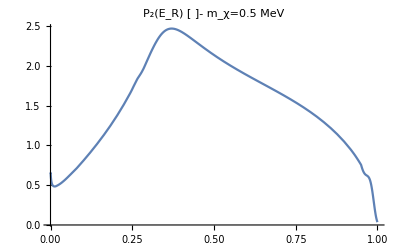

1.52955

```mathematica
10^Log10[(("ne"/.FeλeDictOscillators[[2]]["fitparams"][[1]])10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/(10^FeλeDictOscillators[[2]]["f"][Log10[testkinσinterpolateξmeosc2higherres[["mχ"]]],vχ])(ωmaxofvχ[10^(vχ),testkinσinterpolateξmeosc2higherres[["mχ"]],testkinσinterpolateξmeosc2higherres[["params"]]]-testkinσinterpolateξmeosc2higherres[["ωmin"]])"ℏ"/.testkinσinterpolateξmeosc2higherres[["params"]]]/.vχ->6.35
Plot[%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(E_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}]
NIntegrate[%%,{ξ,10^ξbounds[[1]],10^ξbounds[[2]]}]
```

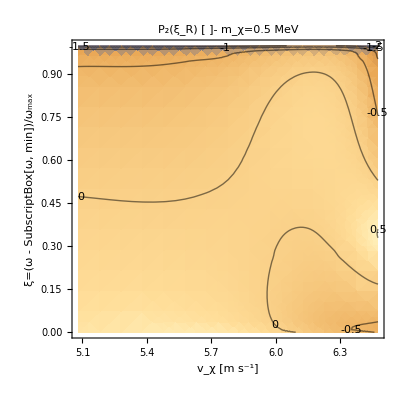

```mathematica
Show[{DensityPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},PlotLabel->"P_2(ξ_R) [ ]- m_χ=0.5 MeV",PlotRange->All,FrameLabel->{"v_χ [m s^-1]" ,"ξ=(ω - SubscriptBox[ω, min])/ω_max"}],ContourPlot[Log10[(10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξ]])/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][vχ,Log10[ξt]],{ξt,10^ξbounds[[1]],10^ξbounds[[2]]}]],{vχ,vχbounds[[1]],vχbounds[[2]]},{ξ,10^ξbounds[[1]],10^ξbounds[[2]]},ContourShading->False,ContourLabels->True,PlotRange->All]}]
```

```mathematica
Print["Peak v_χ~ 10^6.3 = ",N[10^6.3]," [ms^-1]"]
Print["vF = ","vF"/.testkinσinterpolateξmeosc2higherres[["params"]]," [ms^-1]"]
```

Peak v_χ~ 10^6.3 = 1.99526×10^6 [ms^-1]

vF = 2.06517×10^6 [ms^-1]

```mathematica
Ptest[vχ_,ξ_]:=(10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,#2]/NIntegrate[10^testkinσinterpolateξmeosc2higherres[["dσf"]][#1,ξt],{ξt,ξbounds[[1]],ξbounds[[2]]}])&[vχ,ξ]
```

```mathematica
Ptest[vχbounds[[2]]0.99,-3]
```

0.174541